## Part 1. Tensor Manipulation

```mathematica
Quit
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)
```

```mathematica
$CommuteCovDsOnScalars=True;
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]

DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];

DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";
```

```mathematica
DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]

(*DefScalarFunction[V]*)
DefConstantSymbol[ka, PrintAs ->"k"]
DefConstantSymbol[alpha, PrintAs ->"α"]
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[L1, PrintAs ->"λ_1"]
DefConstantSymbol[gamma, PrintAs ->"γ"]
```

((▽_a φ^*) (▽^a φ))

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],-1/2*Scalar[CD[a][Phi[]]CD[-a][Phi[]]]]
```

-1/2 ((▽_a φ) (▽^a φ))

```mathematica
-CD[-b][-1/2CD[a][Phi[]]CD[-a][Phi[]]]CD[b][-1/2CD[c][Phi[]]CD[-c][Phi[]]]//Simplification
```

-(▽^a φ) (▽^b φ) (▽_c▽_b φ) (▽^c▽_a φ)

```mathematica
(metric[a, g]*metric[b, f]*metric[c, e] - metric[a, f]*metric[b, g]*metric[c, e] - metric[a, g]*metric[b, e]*metric[c, f] + 
   metric[a, e]*metric[b, g]*metric[c, f] + metric[a, f]*metric[b, e]*metric[c, g] - metric[a, e]*metric[b, f]*metric[c, g])*CD[-a][Phi[]]*
  CD[-e][Phi[]]*CD[-f][CD[-b][Phi[]]]*CD[-g][CD[-c][Phi[]]]//ContractMetric//Simplification
```

(▽^a φ) (2 (▽^e φ) ((▽_e▽_a φ) (▽_f▽^f φ)-(▽_f▽_e φ) (▽^f▽_a φ))+(▽_a φ) (-(▽_e▽^e φ) (▽_f▽^f φ)+(▽_f▽_e φ) (▽^f▽^e φ)))

```mathematica
(epsilonmetric[a,b,c,d]*epsilonmetric[-e,-f,-g,-d]*CD[e][Phi[]]*CD[-a][Phi[]]*CD[f][CD[-b][Phi[]]]*CD[g][CD[-c][Phi[]]])//ContractMetric//Simplification//Expand
```

-(▽_b φ) (▽^b φ) (▽_c▽^c φ) (▽_e▽^e φ)+2 (▽^b φ) (▽_c▽_b φ) (▽^c φ) (▽_e▽^e φ)-2 (▽^b φ) (▽^c φ) (▽_e▽_c φ) (▽^e▽_b φ)+(▽_b φ) (▽^b φ) (▽_e▽_c φ) (▽^e▽^c φ)

```mathematica
(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][Phi[]]*CD[-e][Phi[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][Phi[]]])//ContractMetric//Simplification
```

(▽^a φ) (2 (▽^e φ) ((▽_e▽_a φ) (▽_f▽^f φ)-(▽_f▽_e φ) (▽^f▽_a φ))+(▽_a φ) (-(▽_e▽^e φ) (▽_f▽^f φ)+(▽_f▽_e φ) (▽^f▽^e φ)))

```mathematica
epsilon[metric][-a,-b,-c,-d]*epsilon[metric][a,b,c,d]
```

-24

```mathematica
epsilon[metric][a,b,c,-d]*epsilon[metric][e,f,g,d]*CD[-a][Phi[]]*CD[-e][Phi[]]*CD[-b][CD[-f][Phi[]]]*CD[-c][CD[-g][Phi[]]]//ContractMetric//Simplification
epsilon[metric][a,b,c,d]epsilon[metric][-f,-g,-h,-d]*CD[f][Phi[]]*CD[-a][Phi[]]*CD[g][CD[-b][Phi[]]]*CD[h][CD[-c][Phi[]]]//ContractMetric//Simplification
```

(▽^a φ) (2 (▽^e φ) ((▽_e▽_a φ) (▽_f▽^f φ)-(▽_f▽_e φ) (▽^f▽_a φ))+(▽_a φ) (-(▽_e▽^e φ) (▽_f▽^f φ)+(▽_f▽_e φ) (▽^f▽^e φ)))

(▽^b φ) (2 (▽^c φ) ((▽_c▽_b φ) (▽_f▽^f φ)-(▽_f▽_c φ) (▽^f▽_b φ))+(▽_b φ) (-(▽_c▽^c φ) (▽_f▽^f φ)+(▽_f▽_c φ) (▽^f▽^c φ)))

```mathematica
epsilon[metric][a,b,c,d]*epsilon[metric][-f,-j,-k,-l]
```

```mathematica
epsilon[metric][a,b,c,d]*epsilon[metric][-f,-b,-c,-d]
```

-6 δ | a |  
  | f

```mathematica
epsilon[metric][a,b,c,d]*epsilon[metric][-a,-b,-c,-d]
```

-24

La definición usada es, arXiv:1404.6495v3

L_2=G_2(ϕ,X)=-λ_1m ϕ^2-α X,
L_3=G_3(ϕ,X)\Box[ϕ]=0, 
G_3=G_5=L_5=0
G_4(ϕ,X) =(k-η/2 X)  
L_4=G_4(ϕ,X) R -2G_(4,X)(ϕ,X)[(\Box(ϕ))^2-ϕ^ab ϕ_ab]+F_4(ϕ,X)(e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c'),
L_4=(k-η/2 X)  R+ η [(\Box(ϕ))^2-ϕ^ab ϕ_ab]-η/X (e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c')
F_4(ϕ,X)=(2 G_(4,X))/X
\Box(ϕ)=∇_a ∇^a ϕ

```mathematica
L=Sqrt[-Detmetric[]]*(-mS^2*PhiC[]*Phi[]-alpha*X[]+(ka-eta/2*X[])*RicciScalarCD[]+eta*(CD[-a]@CD[a]@PhiC[]*CD[-b]@CD[b]@Phi[]-CD[a]@CD[b]@PhiC[]*CD[-a]@CD[-b]@Phi[])-eta/X[]*(epsilonmetric[a,b,c,-d]*epsilonmetric[e,f,g,d]*CD[-a][PhiC[]]*CD[-e][Phi[]]*CD[-b][CD[-f][PhiC[]]]*CD[-c][CD[-g][Phi[]]]))
```

√(-g^OverTilde[~]) (-m^2 φ φ^*-α ((▽_a φ^*) (▽^a φ))+R[▽] (k-1/2 η ((▽_a φ^*) (▽^a φ)))+η (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ))-(η (g | a | g
  |   g | b | f
  |   g | c | e
  |  -g | a | f
  |   g | b | g
  |   g | c | e
  |  -g | a | g
  |   g | b | e
  |   g | c | f
  |  +g | a | e
  |   g | b | g
  |   g | c | f
  |  +g | a | f
  |   g | b | e
  |   g | c | g
  |  -g | a | e
  |   g | b | f
  |   g | c | g
  |  ) (▽_a φ^*) (▽_e φ) (▽_f▽_b φ^*) (▽_g▽_c φ))/((▽_a φ^*) (▽^a φ)))

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation@L;
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//ContractMetric//ToCanonical//Simplification//Simplify;
```

```mathematica
Ecuϕ=ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplify (* //RicciToEinstein//Simplification *)
```

1/2 ((2 α+η R[▽]) (▽_a▽^a φ^*)+η (▽_a R[▽]) (▽^a φ^*)-2 (m^2 φ^*+η (▽^a φ^*) R[▽] |   | b |   
a |   | ;b+η R[▽] | a | b
  |   (▽_b▽_a φ^*)))-1/(g |   |  
a | b (▽^a φ) (▽^b φ^*))η (R[▽] |   | c
b |   (▽^a φ) (▽^b φ^*) (▽_c▽_a φ^*)+2 R[▽] |   | c
a |   (▽^a φ^*) (▽^b φ^*) (▽_c▽_b φ)+R[▽] |   | c
a |   (▽^a φ) (▽^b φ^*) (▽_c▽_b φ^*)+(▽_a φ^*) (▽^a φ) ((▽^b φ^*) R[▽] |   | c |   
b |   | ;c+R[▽] | b | c
  |   (▽_c▽_b φ^*))-2 R[▽] |   |  
a | b (▽^a φ^*) (▽^b φ^*) (▽_c▽^c φ)+2 (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)-3 R[▽] |   |  
a | b (▽^a φ) (▽^b φ^*) (▽_c▽^c φ^*)-4 (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)-(▽^a φ) (▽^b φ^*) R[▽] |   |   |   
a | b | ;c (▽^c φ^*)+4 (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)-2 (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)+2 R[▽] |   |   |   |  
a | c | b | d (▽^a φ^*) (▽^b φ^*) (▽^d▽^c φ)+2 R[▽] |   |   |   |  
a | c | b | d (▽^a φ) (▽^b φ^*) (▽^d▽^c φ^*))+1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^3)2 η (▽^a φ) ((▽^b φ^*) (▽^c φ^*) ((▽_a φ^*) (▽^d▽_b φ) ((▽_d▽_c φ) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^d φ^*) (-(▽_d▽_a φ^*) (▽_e▽_c φ) (▽^e▽_b φ)+(▽_b▽_a φ) (▽_e▽_d φ^*) (▽^e▽_c φ))+(▽_c▽_b φ) ((▽_d▽_a φ^*) (▽^d φ^*) (▽_e▽^e φ)-(▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_a φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ))))+(▽^b φ) ((▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽_b φ^*) (▽^d φ^*) (▽_e▽^e φ)+(▽^d φ^*) ((▽^c φ^*) (-(▽_c▽_b φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_d▽_c φ) (▽_e▽_b φ^*) (▽^e▽_a φ^*)+(▽_c▽_a φ) (▽_e▽_d φ^*) (▽^e▽_b φ^*)-2 (▽_d▽_a φ^*) (▽_e▽_b φ^*) (▽^e▽_c φ))+(▽_b▽_a φ^*) ((▽^c φ^*) (-(▽_d▽_c φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^c φ) (-(▽_d▽_c φ^*) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ^*))))+(▽_a φ^*) (2 (▽^c φ^*) (▽^d▽_c φ) ((▽_d▽_b φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_b φ^*))+(▽^c φ) (▽^d▽_b φ^*) ((▽_d▽_c φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ^*))+(▽_c▽_b φ^*) (▽^c φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ)))))+1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^2)η (2 R[▽] |   | d
c |   (▽_a φ^*) (▽^a φ) (▽^b φ) (▽^c φ^*) (▽_d▽_b φ^*)+2 R[▽] |   | d
b |   (▽_a φ^*) (▽^a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽_c φ)-R[▽] |   |  
b | c (▽_a φ^*) (▽^a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽^d φ)-(▽^a φ) (▽^b φ^*) (▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)-3 (▽^a φ^*) (▽^b φ^*) (▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ)+3 (▽^a φ^*) (▽_b▽_a φ) (▽^b φ^*) (▽_c▽^c φ) (▽_d▽^d φ^*)+2 (▽^a φ) (▽_b▽_a φ^*) (▽^b φ^*) (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽_a φ^*) (▽^a φ) (▽_b▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)+(▽^a φ) (▽_b▽_a φ^*) (▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)-R[▽] |   |  
b | c (▽_a φ^*) (▽^a φ) (▽^b φ) (▽^c φ^*) (▽_d▽^d φ^*)+(▽^a φ) (▽^b φ) (▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ^*)-3 (▽^a φ^*) (▽^b φ^*) (▽_c▽_b φ) (▽^c▽_a φ) (▽_d▽^d φ^*)+(▽^a φ) (▽^b φ^*) (▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ^*)-2 (▽^a φ) (▽^b φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*) (▽_d▽^d φ^*)-2 (▽^a φ) (▽^b φ^*) (▽_c▽_a φ^*) (▽^c▽_b φ) (▽_d▽^d φ^*)-3 (▽_a φ^*) (▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ) (▽_d▽^d φ^*)+(▽_a φ^*) (▽^a φ) (▽^b φ^*) (▽_c▽^c φ) (▽_d▽^d▽_b φ^*)-(▽_a φ^*) (▽^a φ) (▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d▽_b φ^*)+(▽^a φ) (▽^b φ) (▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽^d▽_b φ^*)-(▽^a φ) (▽_b▽_a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽^d▽_c φ^*)-R[▽] |   |  
c | d (▽^a φ) (▽_b▽_a φ^*) (▽^b φ) (▽^c φ^*) (▽^d φ^*)-R[▽] |   |  
a | b (▽^a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*)+(▽^a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ)-3 (▽^a φ) (▽^b φ^*) (▽_c▽^c φ) (▽_d▽_b φ^*) (▽^d▽_a φ^*)+3 (▽^a φ) (▽^b φ^*) (▽^c▽_b φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)-(▽^a φ) (▽^b φ) (▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ^*)+3 (▽^a φ^*) (▽^b φ^*) (▽^c▽_a φ) (▽_d▽_c φ^*) (▽^d▽_b φ)+(▽^a φ) (▽^b φ^*) (▽^c φ^*) (▽_d▽_c▽_a φ^*) (▽^d▽_b φ)+2 (▽^a φ) (▽^b φ) (▽^c▽_a φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+2 (▽_a φ^*) (▽^a φ) (▽^c▽^b φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+3 (▽^a φ^*) (▽^b φ^*) (▽^c▽_a φ) (▽_d▽_b φ^*) (▽^d▽_c φ)-(▽^a φ) (▽^b φ) (▽^c φ^*) (▽_d▽_b▽_a φ^*) (▽^d▽_c φ^*)+(▽^a φ) (▽^b φ^*) (▽_c▽_a φ^*) (▽_d▽_b φ^*) (▽^d▽^c φ)-3 (▽^a φ^*) (▽_b▽_a φ) (▽^b φ^*) (▽_d▽_c φ^*) (▽^d▽^c φ)-(▽^a φ) (▽_b▽_a φ^*) (▽^b φ^*) (▽_d▽_c φ^*) (▽^d▽^c φ)-(▽_a φ^*) (▽^a φ) (▽^b φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽^c φ)-(▽^a φ) (▽_b▽_a φ^*) (▽^b φ) (▽_d▽_c φ^*) (▽^d▽^c φ^*)-(▽^a φ) (▽_b▽_a φ) (▽^b φ^*) (▽_d▽_c φ^*) (▽^d▽^c φ^*)+(▽_a φ^*) (▽^a φ) (▽^b φ) (▽_d▽_c▽_b φ^*) (▽^d▽^c φ^*)-2 R[▽] |   |   |   |  
b | c | d | e (▽^a φ) (▽^b φ) (▽^c φ^*) (▽^d φ^*) (▽^e▽_a φ^*)+R[▽] |   |   |   |  
b | d | c | e (▽_a φ^*) (▽^a φ) (▽^b φ^*) (▽^c φ^*) (▽^e▽^d φ)+R[▽] |   |   |   |  
b | d | c | e (▽_a φ^*) (▽^a φ) (▽^b φ) (▽^c φ^*) (▽^e▽^d φ^*))

```mathematica
Ecu2ϕ=Collect[Ecuϕ, {alpha, eta}, Simplify]
```

-m^2 φ^*+α (▽_a▽^a φ^*)+1/2 η (R[▽] (▽_a▽^a φ^*)+(▽_a R[▽]) (▽^a φ^*)-2 (▽^a φ^*) (▽_b R[▽] |   | b
a |  )-2 R[▽] |   |  
a | b (▽^b▽^a φ^*)-1/(g |   |  
a | b (▽^a φ) (▽^b φ^*))2 (2 (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)-4 (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)-R[▽] |   |  
a | b (▽^b φ^*) (2 (▽^a φ^*) (▽_c▽^c φ)+3 (▽^a φ) (▽_c▽^c φ^*))-(▽^a φ) (▽^b φ^*) (▽_c R[▽] |   |  
a | b) (▽^c φ^*)+2 R[▽] |   |  
b | c (▽^a φ^*) (▽^b φ^*) (▽^c▽_a φ)+R[▽] |   |  
b | c (▽^a φ) (▽^b φ^*) (▽^c▽_a φ^*)+4 (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)+R[▽] |   |  
a | c (▽^a φ) (▽^b φ^*) (▽^c▽_b φ^*)-2 (▽_a▽^a φ) (▽_c▽_b φ^*) (▽^c▽^b φ^*)+(▽_a φ^*) (▽^a φ) ((▽^b φ^*) (▽_c R[▽] |   | c
b |  )+R[▽] |   |  
b | c (▽^c▽^b φ^*))+2 R[▽] |   |   |   |  
a | c | b | d (▽^a φ^*) (▽^b φ^*) (▽^d▽^c φ)+2 R[▽] |   |   |   |  
a | d | b | c (▽^a φ) (▽^b φ^*) (▽^d▽^c φ^*))+1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^3)4 (▽^a φ) ((▽^b φ^*) (▽^c φ^*) ((▽_a φ^*) (▽^d▽_b φ) ((▽_d▽_c φ) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^d φ^*) (-(▽_d▽_a φ^*) (▽_e▽_c φ) (▽^e▽_b φ)+(▽_b▽_a φ) (▽_e▽_d φ^*) (▽^e▽_c φ))+(▽_c▽_b φ) ((▽_d▽_a φ^*) (▽^d φ^*) (▽_e▽^e φ)-(▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_a φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ))))+(▽^b φ) ((▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽_b φ^*) (▽^d φ^*) (▽_e▽^e φ)+(▽^d φ^*) ((▽^c φ^*) (-(▽_c▽_b φ^*) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_d▽_c φ) (▽_e▽_b φ^*) (▽^e▽_a φ^*)+(▽_c▽_a φ) (▽_e▽_d φ^*) (▽^e▽_b φ^*)-2 (▽_d▽_a φ^*) (▽_e▽_b φ^*) (▽^e▽_c φ))+(▽_b▽_a φ^*) ((▽^c φ^*) (-(▽_d▽_c φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ))+(▽^c φ) (-(▽_d▽_c φ^*) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽_c φ^*))))+(▽_a φ^*) (2 (▽^c φ^*) (▽^d▽_c φ) ((▽_d▽_b φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_b φ^*))+(▽^c φ) (▽^d▽_b φ^*) ((▽_d▽_c φ^*) (▽_e▽^e φ^*)-(▽_e▽_d φ^*) (▽^e▽_c φ^*))+(▽_c▽_b φ^*) (▽^c φ^*) (-(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ)))))-1/((g |   |  
a | b (▽^a φ) (▽^b φ^*))^2)2 (R[▽] |   |  
b | c (▽_a φ^*) (▽^a φ) (▽^c φ^*) ((▽^b φ^*) (▽_d▽^d φ)+(▽^b φ) (▽_d▽^d φ^*))+3 (▽^a φ^*) (▽^b φ^*) ((▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ)+(▽^c▽_a φ) ((▽_c▽_b φ) (▽_d▽^d φ^*)-(▽_d▽_c φ^*) (▽^d▽_b φ)-(▽_d▽_b φ^*) (▽^d▽_c φ))+(▽_b▽_a φ) (-(▽_c▽^c φ) (▽_d▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ)))+(▽^a φ) ((▽^b φ) (-(▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ^*)+2 (▽_c▽_b φ^*) (▽^c▽_a φ^*) (▽_d▽^d φ^*)-(▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽^d▽_b φ^*)+(▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ^*)-2 (▽^c▽_a φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+(▽^c φ^*) (▽_d▽_b▽_a φ^*) (▽^d▽_c φ^*)+(▽_b▽_a φ^*) (-(▽_c▽^c φ^*) (▽_d▽^d φ^*)+R[▽] |   |  
c | d (▽^c φ^*) (▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ^*))+2 R[▽] |   |   |   |  
b | c | d | e (▽^c φ^*) (▽^d φ^*) (▽^e▽_a φ^*))+(▽^b φ^*) ((▽_c▽_b▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)-(▽_c▽_b φ^*) (▽^c▽_a φ) (▽_d▽^d φ^*)+2 (▽_c▽_a φ^*) (▽^c▽_b φ) (▽_d▽^d φ^*)-(▽_a φ^*) (▽_c▽^c φ) (▽_d▽^d▽_b φ^*)+(▽_b▽_a φ) (▽^c φ^*) (▽_d▽^d▽_c φ^*)+R[▽] |   |  
a | d (▽_c▽_b φ) (▽^c φ^*) (▽^d φ^*)-(▽^c φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽_a φ)+3 (▽_c▽^c φ) (▽_d▽_b φ^*) (▽^d▽_a φ^*)-3 (▽^c▽_b φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)-2 R[▽] |   |  
c | d (▽_a φ^*) (▽^c φ^*) (▽^d▽_b φ)-(▽^c φ^*) (▽_d▽_c▽_a φ^*) (▽^d▽_b φ)-(▽_c▽_a φ^*) (▽_d▽_b φ^*) (▽^d▽^c φ)+(▽_a φ^*) (▽_d▽_c▽_b φ^*) (▽^d▽^c φ)+(▽_b▽_a φ^*) (-2 (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽_d▽_c φ^*) (▽^d▽^c φ))+(▽_b▽_a φ) (▽_d▽_c φ^*) (▽^d▽^c φ^*)-R[▽] |   |   |   |  
b | d | c | e (▽_a φ^*) (▽^c φ^*) (▽^e▽^d φ))-(▽_a φ^*) ((▽_b▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)-3 (▽_c▽_b φ^*) (▽^c▽^b φ) (▽_d▽^d φ^*)-(▽^b φ) (▽_c▽^c φ^*) (▽_d▽^d▽_b φ^*)+2 R[▽] |   |  
c | d (▽^b φ) (▽^c φ^*) (▽^d▽_b φ^*)+2 (▽^c▽^b φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+(▽^b φ) (▽_d▽_c▽_b φ^*) (▽^d▽^c φ^*)+R[▽] |   |   |   |  
b | d | c | e (▽^b φ) (▽^c φ^*) (▽^e▽^d φ^*)))))

We obtained the coefficients

```mathematica
Ecu2ϕ-alpha Coefficient[Ecu2ϕ,alpha]-eta Coefficient[Ecu2ϕ,eta]
Coefficient[Ecu2ϕ,alpha]
Coefficient[Ecu2ϕ,eta]
```

Checking if is equal to when is considerate the scalar field real

```mathematica
(*
Ecu2ϕ/.PhiC[]-> Phi[]//ToCanonical//Simplify;
Collect[%, {alpha, eta},Simplify]
*)
```

And here is the tensor equation of motion. We vary with respect to g^ab.

```mathematica
RHS=-VarD[metpert[LI[1],a,b],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1//SeparateMetric[metric]//ContractMetric//ToCanonical//Simplification//Simplify;
```

```mathematica
Ecu=ContractMetric[SortCovDs[RHS,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical//RicciToEinstein//ContractMetric//ToCanonical//Simplification//Simplify(* //Simplify//RicciToEinstein//Simplification ;*)
```

1/(4 (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2)(-2 α (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_a φ^*) (▽_b φ)+η R[▽] (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_a φ^*) (▽_b φ)-2 α (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_a φ) (▽_b φ^*)+η R[▽] (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_a φ) (▽_b φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_b▽_a φ^*) (▽_c▽^c φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_b▽_a φ) (▽_c▽^c φ^*)+2 η G[▽] |   |  
b | c (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_a φ^*) (▽^c φ)+2 η G[▽] |   |  
a | c (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_b φ^*) (▽^c φ)-η R[▽] (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ^*) (▽_c φ) (▽^c φ)+2 η R[▽] (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ) (▽_c φ^*) (▽^c φ)+2 η R[▽] (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ^*) (▽_c φ^*) (▽^c φ)+2 G[▽] |   |  
a | b (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (2 k-η (▽_c φ^*) (▽^c φ))+2 η G[▽] |   |  
b | c (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_a φ) (▽^c φ^*)+2 η G[▽] |   |  
a | c (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_b φ) (▽^c φ^*)-η R[▽] (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ) (▽_c φ^*) (▽^c φ^*)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_c▽_b φ^*) (▽^c▽_a φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽_c▽_a φ^*) (▽^c▽_b φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ^*) (▽_c▽^c φ) (▽_d▽^d φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽^d φ)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_c▽_b φ^*) (▽^c φ) (▽_d▽^d φ)-3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽^d φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)-3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_c▽_b φ^*) (▽^c φ^*) (▽_d▽^d φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ) (▽_c▽^c φ) (▽_d▽^d φ^*)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ^*) (▽_c▽^c φ) (▽_d▽^d φ^*)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ) (▽_c▽^c φ^*) (▽_d▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽_c▽_a φ) (▽^c φ) (▽_d▽^d φ^*)-3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_c▽_b φ) (▽^c φ) (▽_d▽^d φ^*)-3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_c▽_b φ^*) (▽^c φ) (▽_d▽^d φ^*)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽^d φ^*)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d φ^*)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ) (▽^c φ^*) (▽_d▽^d▽_c φ)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ^*) (▽^c φ^*) (▽_d▽^d▽_c φ)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ) (▽^c φ) (▽_d▽^d▽_c φ^*)-η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ^*) (▽^c φ) (▽_d▽^d▽_c φ^*)-2 η G[▽] |   |  
c | d (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ^*) (▽^c φ) (▽^d φ)+2 η G[▽] |   |  
b | d (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ)+2 η G[▽] |   |  
a | d (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_c φ^*) (▽^c φ) (▽_d▽_b▽_a φ^*) (▽^d φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b▽_a φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽^c φ) (▽_d▽_c▽_a φ^*) (▽^d φ)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽^c φ) (▽_d▽_c▽_b φ^*) (▽^d φ)+2 η R[▽] |   |   |   |  
a | c | b | d (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽^c φ) (▽^d φ^*)+2 η R[▽] |   |   |   |  
a | d | b | c (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (▽^c φ) (▽^d φ^*)+2 η G[▽] |   |  
b | d (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*)+2 η G[▽] |   |  
a | d (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*)-2 η G[▽] |   |  
c | d (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ) (▽^c φ^*) (▽^d φ^*)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_c▽_b φ) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ^*)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽_b φ) (▽^d φ^*)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_c▽_a φ) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_c φ^*) (▽^c φ) (▽_d▽_b▽_a φ) (▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b▽_a φ^*) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b▽_a φ) (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b▽_a φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽^c φ) (▽_d▽_c▽_a φ) (▽^d φ^*)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽^c φ^*) (▽_d▽_c▽_a φ) (▽^d φ^*)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽^c φ) (▽_d▽_c▽_a φ^*) (▽^d φ^*)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽^c φ) (▽_d▽_c▽_b φ) (▽^d φ^*)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽^c φ^*) (▽_d▽_c▽_b φ) (▽^d φ^*)+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽^c φ) (▽_d▽_c▽_b φ^*) (▽^d φ^*)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽^c φ^*) (▽_d▽_c φ) (▽^d▽_a φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_a φ)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽^c φ^*) (▽_d▽_c φ^*) (▽^d▽_a φ)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽^c φ^*) (▽_d▽_c φ) (▽^d▽_b φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_b φ)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽^c φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d▽_c φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽^c φ^*) (▽_d▽_a φ^*) (▽^d▽_c φ)+3 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d▽_c φ)+2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽^c φ^*) (▽_d▽_b φ^*) (▽^d▽_c φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ^*) (▽_d▽_c φ) (▽^d▽^c φ)-4 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽_b φ) (▽_d▽_c φ^*) (▽^d▽^c φ)-4 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ^*) (▽_d▽_c φ^*) (▽^d▽^c φ)-2 η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽_b φ) (▽_d▽_c φ^*) (▽^d▽^c φ^*)+2 η (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ) (▽_e▽^e φ)+2 η (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ) (▽_e▽^e φ)-2 η (▽_a φ^*) (▽_b φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽^e φ)+2 η (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽^e φ)+2 η (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽^e φ)-2 η (▽_a φ^*) (▽_b φ^*) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ)+2 η (▽_a φ^*) (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ)+2 η (▽_a φ) (▽_b φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ)-2 η (▽_a φ^*) (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ) (▽_e▽^e φ^*)-2 η (▽_a φ) (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ) (▽_e▽^e φ^*)+2 η (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ) (▽_e▽^e φ^*)+2 η (▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ) (▽_e▽^e φ^*)+2 η (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽^e φ^*)+2 η (▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽^e φ^*)+2 η (▽_a φ^*) (▽_b φ) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)+2 η (▽_a φ) (▽_b φ^*) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)-2 η (▽_a φ) (▽_b φ) (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)-2 η (▽_a φ) (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ^*)+2 η (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ)-η (▽_b φ^*) (▽_c▽_a φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ)-η (▽_a φ^*) (▽_c▽_b φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ)-η R[▽] |   |   |   |  
b | c | d | e (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)-η R[▽] |   |   |   |  
a | c | d | e (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)+2 η R[▽] |   |   |   |  
b | d | c | e (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_a φ) (▽^c φ) (▽^d φ^*) (▽^e φ^*)+2 η R[▽] |   |   |   |  
a | d | c | e (g |   |  
a | b (▽^a φ) (▽^b φ^*)) (▽_b φ) (▽^c φ) (▽^d φ^*) (▽^e φ^*)+η (▽_b φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽_a φ) (▽^e φ^*)+η (▽_a φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽_b φ) (▽^e φ^*)-3 η (▽_b φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ) (▽_e▽_c φ) (▽^e φ^*)-3 η (▽_a φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ) (▽_e▽_c φ) (▽^e φ^*)-η (▽_b φ^*) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽_c φ) (▽^e φ^*)-η (▽_a φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽_c φ) (▽^e φ^*)-3 η (▽_b φ) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽_c φ^*) (▽^e φ^*)-3 η (▽_a φ) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽_c φ^*) (▽^e φ^*)+2 η (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ) (▽^e φ^*)+2 η (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)+η (▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)+η (▽_a φ) (▽_c▽_b φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)-η (▽_b φ) (▽_c▽_a φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)-η (▽_a φ) (▽_c▽_b φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)+2 η (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*)-η (▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*)-η (▽_a φ) (▽_c▽_b φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*)-2 η (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_a φ)-2 η (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_a φ)-2 η (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_a φ^*)-2 η (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_b φ)-2 η (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_b φ)-2 η (▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_b φ^*)+2 η (▽_a φ^*) (▽_b φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)+η (▽_a φ^*) (▽_b φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)+η (▽_a φ) (▽_b φ^*) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)+2 η (▽_a φ^*) (▽_b φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ)-2 η (▽_a φ^*) (▽_b φ) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)-2 η (▽_a φ) (▽_b φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)+2 η (▽_a φ) (▽_b φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)+η (▽_a φ^*) (▽_b φ) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)+η (▽_a φ) (▽_b φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)+2 η (▽_a φ) (▽_b φ) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ^*)-2 η (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_a φ^*) (▽^e▽_d φ)-2 η (▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_b φ^*) (▽^e▽_d φ)+2 η (▽_a φ^*) (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_e▽_d φ^*) (▽^e▽^d φ)+2 η (▽_a φ) (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽_e▽_d φ^*) (▽^e▽^d φ)+2 g |   |  
a | b ((g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 (m^2 φ φ^*+(α-η R[▽]) (▽_c φ^*) (▽^c φ)+η (▽_c▽^c φ) (▽_d▽^d φ^*)-2 η G[▽] |   |  
c | d (▽^c φ) (▽^d φ^*)-η (▽_d▽_c φ^*) (▽^d▽^c φ))-η (▽^c φ) ((▽_c φ^*) ((▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*) (▽_f▽^f φ)+(▽^d φ) ((▽_e▽_d φ) (▽^e φ^*) (▽_f▽^f φ^*)+(▽_e▽_d φ^*) ((▽^e φ^*) (▽_f▽^f φ)+(▽^e φ) (▽_f▽^f φ^*))))-((▽_d▽_c φ) (▽^d φ^*) (▽^e φ^*) (▽_f▽_e φ)+(▽^d φ) (2 (▽_e▽_c φ) (▽^e φ^*) (▽_f▽_d φ^*)+(▽_d▽_c φ^*) (▽^e φ) (▽_f▽_e φ^*))) (▽^f φ^*))+η (g |   |  
a | b (▽^a φ) (▽^b φ^*)) ((▽^c φ^*) (▽^d φ^*) ((▽_d▽_c φ) (▽_e▽^e φ)-(▽_e▽_d φ) (▽^e▽_c φ))+(▽_c φ^*) (▽^c φ) (-R[▽] (▽_d φ^*) (▽^d φ)+(▽_d▽^d φ) (▽_e▽^e φ^*)+(▽^d φ^*) (▽_e▽^e▽_d φ)+(▽^d φ) (▽_e▽^e▽_d φ^*)-2 G[▽] |   |  
d | e (▽^d φ) (▽^e φ^*)+(▽_e▽_d φ^*) (▽^e▽^d φ))+(▽^c φ) ((▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)+(▽_d▽_c φ^*) ((▽^d φ^*) (▽_e▽^e φ)+(▽^d φ) (▽_e▽^e φ^*))-(▽^d φ^*) (▽_e▽_d▽_c φ) (▽^e φ^*)-(▽^d φ) (▽_e▽_d▽_c φ^*) (▽^e φ^*)-3 (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)-(▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)-(▽^d φ^*) (▽_e▽_c φ^*) (▽^e▽_d φ)-R[▽] |   |   |   |  
c | e | d | f (▽^d φ) (▽^e φ^*) (▽^f φ^*)))))

```mathematica
Ecu=Collect[Ecu, {alpha, eta},Simplify]
```

k G[▽] |   |  
a | b+1/2 m^2 g |   |  
a | b φ φ^*+1/2 α (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (▽_c φ^*) (▽^c φ))+1/(4 (g |   |  
a | b (▽^a φ) (▽^b φ^*))^2)η ((g |   |  
a | b (▽^a φ) (▽^b φ^*))^2 ((▽_a φ^*) (R[▽] (▽_b φ)+2 G[▽] |   |  
b | c (▽^c φ))+(▽_a φ) (R[▽] (▽_b φ^*)+2 G[▽] |   |  
b | c (▽^c φ^*))-2 ((▽_b▽_a φ^*) (▽_c▽^c φ)+(▽_b▽_a φ) (▽_c▽^c φ^*)-G[▽] |   |  
a | c (▽_b φ^*) (▽^c φ)+G[▽] |   |  
a | b (▽_c φ^*) (▽^c φ)+g |   |  
a | b R[▽] (▽_c φ^*) (▽^c φ)-G[▽] |   |  
a | c (▽_b φ) (▽^c φ^*)-(▽_c▽_b φ^*) (▽^c▽_a φ)-(▽_c▽_a φ^*) (▽^c▽_b φ)-g |   |  
a | b (▽_c▽^c φ) (▽_d▽^d φ^*)+2 G[▽] |   |  
c | d g |   |  
a | b (▽^c φ) (▽^d φ^*)-R[▽] |   |   |   |  
a | c | b | d (▽^c φ) (▽^d φ^*)-R[▽] |   |   |   |  
a | d | b | c (▽^c φ) (▽^d φ^*)+g |   |  
a | b (▽_d▽_c φ^*) (▽^d▽^c φ)))+2 (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ) (▽_e▽^e φ)+2 (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽^e φ)+2 (▽_a φ^*) (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ)-2 (▽_a φ^*) (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ) (▽_e▽^e φ^*)+2 (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ) (▽_e▽^e φ^*)+2 (▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ) (▽_e▽^e φ^*)+2 (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽^e φ^*)+2 (▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽^e φ^*)+2 (▽_a φ^*) (▽_b φ) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)-2 (▽_a φ) (▽_b φ) (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)-2 (▽_a φ) (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ^*)+2 (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ)-(▽_a φ^*) (▽_c▽_b φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ)+(▽_a φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽_b φ) (▽^e φ^*)-3 (▽_a φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ) (▽_e▽_c φ) (▽^e φ^*)-(▽_a φ^*) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽_c φ) (▽^e φ^*)-3 (▽_b φ) (▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽_c φ^*) (▽^e φ^*)-3 (▽_a φ) (▽^c φ) (▽_d▽_b φ) (▽^d φ^*) (▽_e▽_c φ^*) (▽^e φ^*)+2 (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ) (▽^e φ^*)+2 (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)+(▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)+(▽_a φ) (▽_c▽_b φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)-(▽_b φ) (▽_c▽_a φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)-(▽_a φ) (▽_c▽_b φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*)+2 (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*)-(▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*)-(▽_a φ) (▽_c▽_b φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*)-2 (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_a φ^*)-2 (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_b φ)-2 (▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_b φ)-2 (▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_b φ^*)+(▽_a φ^*) (▽_b φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)-2 (▽_a φ^*) (▽_b φ) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)+2 (▽_a φ) (▽_b φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)+(▽_a φ^*) (▽_b φ) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)+2 (▽_a φ) (▽_b φ) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ^*)-2 (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_a φ^*) (▽^e▽_d φ)-2 (▽_a φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_b φ^*) (▽^e▽_d φ)+2 (▽_a φ^*) (▽_b φ) (▽_c φ^*) (▽^c φ) (▽_e▽_d φ^*) (▽^e▽^d φ)+(▽_b φ^*) (2 (▽_a φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ)+2 (▽_a φ) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)-(▽_c▽_a φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ)+(▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽_a φ) (▽^e φ^*)-3 (▽^c φ) (▽_d▽_a φ^*) (▽^d φ) (▽_e▽_c φ) (▽^e φ^*)-(▽^c φ) (▽_d▽_a φ) (▽^d φ^*) (▽_e▽_c φ) (▽^e φ^*)+(▽_a φ) (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)-2 (▽_a φ) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)-2 (▽_a φ^*) (▽^c φ) ((▽_d▽_c φ^*) (▽^d φ) (▽_e▽^e φ)+(▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ)-((▽^d φ^*) (▽_e▽_d φ)+(▽^d φ) (▽_e▽_d φ^*)) (▽^e▽_c φ))+(▽_a φ) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)+2 (▽_c φ^*) (▽^c φ) ((▽_d▽_a φ^*) (▽^d φ) (▽_e▽^e φ)+(▽_d▽_a φ) (▽^d φ^*) (▽_e▽^e φ)-(▽_a φ) (▽_d▽^d φ) (▽_e▽^e φ^*)-(▽^d φ^*) (▽_e▽_d φ) (▽^e▽_a φ)-(▽^d φ) (▽_e▽_d φ^*) (▽^e▽_a φ)+(▽_a φ) (▽_e▽_d φ^*) (▽^e▽^d φ)))-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽_d φ) (▽^e φ^*) (▽_f▽^f φ)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ^*) (▽_f▽^f φ)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e φ) (▽_f▽^f φ^*)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽_d φ) (▽^e φ^*) (▽_f▽^f φ^*)+4 g |   |  
a | b (▽^c φ) (▽^d φ) (▽_e▽_c φ) (▽^e φ^*) (▽_f▽_d φ^*) (▽^f φ^*)+2 g |   |  
a | b (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽^e φ^*) (▽_f▽_e φ) (▽^f φ^*)+2 g |   |  
a | b (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽^e φ) (▽_f▽_e φ^*) (▽^f φ^*)-(g |   |  
a | b (▽^a φ) (▽^b φ^*)) (2 (▽_b▽_a φ^*) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ)+(▽_b φ^*) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽^d φ)+3 (▽_b φ^*) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽^d φ)+2 (▽_b φ) (▽_c▽_a φ^*) (▽^c φ^*) (▽_d▽^d φ)+2 (▽_b▽_a φ) (▽_c φ^*) (▽^c φ) (▽_d▽^d φ^*)+2 (▽_b φ^*) (▽_c▽_a φ) (▽^c φ) (▽_d▽^d φ^*)+3 (▽_b φ) (▽_c▽_a φ^*) (▽^c φ) (▽_d▽^d φ^*)+(▽_b φ) (▽_c▽_a φ) (▽^c φ^*) (▽_d▽^d φ^*)-2 G[▽] |   |  
a | d (▽_b φ^*) (▽_c φ^*) (▽^c φ) (▽^d φ)+2 g |   |  
a | b R[▽] (▽_c φ^*) (▽^c φ) (▽_d φ^*) (▽^d φ)-2 (▽_c▽_a φ^*) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ)+2 (▽_c φ^*) (▽^c φ) (▽_d▽_b▽_a φ^*) (▽^d φ)+2 (▽_b▽_a φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ)-(▽_b φ^*) (▽^c φ) (▽_d▽_c▽_a φ^*) (▽^d φ)-2 G[▽] |   |  
a | d (▽_b φ) (▽_c φ^*) (▽^c φ) (▽^d φ^*)-2 (▽_c▽_b φ) (▽^c φ) (▽_d▽_a φ^*) (▽^d φ^*)-2 (▽_c▽_a φ) (▽^c φ^*) (▽_d▽_b φ) (▽^d φ^*)-2 (▽_c▽_a φ) (▽^c φ) (▽_d▽_b φ^*) (▽^d φ^*)+2 (▽_c φ^*) (▽^c φ) (▽_d▽_b▽_a φ) (▽^d φ^*)+2 (▽_b▽_a φ^*) (▽^c φ) (▽_d▽_c φ) (▽^d φ^*)+2 (▽_b▽_a φ) (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*)+2 (▽_b▽_a φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*)-(▽_b φ^*) (▽^c φ) (▽_d▽_c▽_a φ) (▽^d φ^*)-(▽_b φ) (▽^c φ^*) (▽_d▽_c▽_a φ) (▽^d φ^*)-(▽_b φ) (▽^c φ) (▽_d▽_c▽_a φ^*) (▽^d φ^*)-3 (▽_b φ^*) (▽^c φ^*) (▽_d▽_c φ) (▽^d▽_a φ)-2 (▽_b φ^*) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_a φ)-3 (▽_b φ) (▽^c φ^*) (▽_d▽_c φ^*) (▽^d▽_a φ)-3 (▽_b φ) (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_a φ^*)-3 (▽_b φ^*) (▽^c φ) (▽_d▽_a φ^*) (▽^d▽_c φ)-2 (▽_b φ) (▽^c φ^*) (▽_d▽_a φ^*) (▽^d▽_c φ)-2 g |   |  
a | b (▽^c φ^*) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ)-2 g |   |  
a | b (▽^c φ) (▽_d▽_c φ^*) (▽^d φ^*) (▽_e▽^e φ)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽_d▽^d φ) (▽_e▽^e φ^*)-2 g |   |  
a | b (▽^c φ) (▽_d▽_c φ^*) (▽^d φ) (▽_e▽^e φ^*)-2 g |   |  
a | b (▽^c φ) (▽_d▽_c φ) (▽^d φ^*) (▽_e▽^e φ^*)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ^*) (▽_e▽^e▽_d φ)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ) (▽_e▽^e▽_d φ^*)+R[▽] |   |   |   |  
a | c | d | e (▽_b φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)+4 G[▽] |   |  
d | e g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽^d φ) (▽^e φ^*)-2 R[▽] |   |   |   |  
a | d | c | e (▽_b φ) (▽^c φ) (▽^d φ^*) (▽^e φ^*)+2 g |   |  
a | b (▽^c φ) (▽^d φ^*) (▽_e▽_d▽_c φ) (▽^e φ^*)+2 g |   |  
a | b (▽^c φ) (▽^d φ) (▽_e▽_d▽_c φ^*) (▽^e φ^*)+(▽_a φ^*) ((▽_c▽_b φ^*) (▽^c φ) (▽_d▽^d φ)+3 (▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d φ)+2 (▽_c▽_b φ) (▽^c φ) (▽_d▽^d φ^*)-2 G[▽] |   |  
b | d (▽_c φ^*) (▽^c φ) (▽^d φ)-(▽^c φ) (▽_d▽_c▽_b φ^*) (▽^d φ)-(▽^c φ) (▽_d▽_c▽_b φ) (▽^d φ^*)-3 (▽^c φ^*) (▽_d▽_c φ) (▽^d▽_b φ)-2 (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_b φ)-3 (▽^c φ) (▽_d▽_b φ^*) (▽^d▽_c φ)+(▽_b φ^*) (R[▽] (▽_c φ) (▽^c φ)-2 (▽_c▽^c φ) (▽_d▽^d φ)+2 G[▽] |   |  
c | d (▽^c φ) (▽^d φ)+2 (▽_d▽_c φ) (▽^d▽^c φ))+(▽_b φ) (-2 R[▽] (▽_c φ^*) (▽^c φ)-2 (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽^c φ^*) (▽_d▽^d▽_c φ)+(▽^c φ) (▽_d▽^d▽_c φ^*)+4 (▽_d▽_c φ^*) (▽^d▽^c φ))+R[▽] |   |   |   |  
b | c | d | e (▽^c φ) (▽^d φ) (▽^e φ^*))+(▽_a φ) (2 (▽_c▽_b φ^*) (▽^c φ^*) (▽_d▽^d φ)+3 (▽_c▽_b φ^*) (▽^c φ) (▽_d▽^d φ^*)+(▽_c▽_b φ) (▽^c φ^*) (▽_d▽^d φ^*)-2 G[▽] |   |  
b | d (▽_c φ^*) (▽^c φ) (▽^d φ^*)-(▽^c φ^*) (▽_d▽_c▽_b φ) (▽^d φ^*)-(▽^c φ) (▽_d▽_c▽_b φ^*) (▽^d φ^*)-3 (▽^c φ^*) (▽_d▽_c φ^*) (▽^d▽_b φ)-3 (▽^c φ) (▽_d▽_c φ^*) (▽^d▽_b φ^*)-2 (▽^c φ^*) (▽_d▽_b φ^*) (▽^d▽_c φ)+(▽_b φ^*) (-2 R[▽] (▽_c φ^*) (▽^c φ)-2 (▽_c▽^c φ) (▽_d▽^d φ^*)+(▽^c φ^*) (▽_d▽^d▽_c φ)+(▽^c φ) (▽_d▽^d▽_c φ^*)+4 (▽_d▽_c φ^*) (▽^d▽^c φ))+(▽_b φ) (R[▽] (▽_c φ^*) (▽^c φ^*)-2 (▽_c▽^c φ^*) (▽_d▽^d φ^*)+2 G[▽] |   |  
c | d (▽^c φ^*) (▽^d φ^*)+2 (▽_d▽_c φ^*) (▽^d▽^c φ^*))-2 R[▽] |   |   |   |  
b | d | c | e (▽^c φ) (▽^d φ^*) (▽^e φ^*))+2 g |   |  
a | b (▽^c φ^*) (▽^d φ^*) (▽_e▽_d φ) (▽^e▽_c φ)+6 g |   |  
a | b (▽^c φ) (▽^d φ^*) (▽_e▽_d φ^*) (▽^e▽_c φ)+2 g |   |  
a | b (▽^c φ) (▽^d φ) (▽_e▽_d φ^*) (▽^e▽_c φ^*)+2 g |   |  
a | b (▽^c φ) (▽^d φ^*) (▽_e▽_c φ^*) (▽^e▽_d φ)-2 g |   |  
a | b (▽_c φ^*) (▽^c φ) (▽_e▽_d φ^*) (▽^e▽^d φ)+2 g |   |  
a | b R[▽] |   |   |   |  
c | e | d | f (▽^c φ) (▽^d φ) (▽^e φ^*) (▽^f φ^*)))

```mathematica
Ecu-alpha Coefficient[Ecu,alpha]-eta Coefficient[Ecu,eta]
Coefficient[Ecu,alpha]
Coefficient[Ecu,eta]
```

Checking if is equal to when is considerate the scalar field real

```mathematica
(*
Ecu/.PhiC[]-> Phi[]//ToCanonical//Simplify;
Collect[%, {alpha, eta},Simplify]
*)
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2018, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
(*<<xAct`xCoba`*)
```

```mathematica
$Info=False;
$CVVerbose=False;
```

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then two scalar functions:

```mathematica
DefScalarFunction[NN]
DefScalarFunction[gg]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-NN[r[]]^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-NN[r]^2 | 0 | 0 | 0
0 | gg[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-NN[r]^2,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→gg[r]^2,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

### Pasando las ecuaciones a coordenadas

Now let’s do something more fun, the B.H equation of motion. I will start with the scalar equation of motion so we need to tell xCoba that ϕ depends on r only. We first define a new scalar function and a new constant q

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
```

Next, we need to set the scalar to be ϕ= φ(r)Exp[-iwt]

```mathematica
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];

ChangeComponents[RicciCD[a,b]//ToBasis[esf],RicciCD[-a, -b]//ToBasis[esf]];
```

If we want to see these values, we first need to put it in the appropriate basis, and then ask xCoba to substitute in the appropriate value. Note that you may need to use ToValues multiple times.

```mathematica
org[expr_]:=ToValues@ToValues@ComponentArray@ToValues@TraceBasisDummy@ToBasis[esf]@Implode@expr
```

```mathematica
noScalar=Scalar[cont_]:>NoScalar[cont];
```

```mathematica
evalScalar=Scalar[cont_]:>org@cont;
```

```mathematica
X[]/.evalScalar//org//FullSimplify
```

-(w^2 ϕ[r]^2)/NN[r]^2+ϕ'[r]^2/gg[r]^2

```mathematica
Hesfϕ=Ecu2ϕ/.evalScalar//org//Simplify
```

(ⅇ^(-ⅈ w t) (w^6 gg[r]^11 (-m^2 NN[r]^2 r^2+w^2 (η+α r^2)) ϕ[r]^7-9 η NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (2 η w^2 r ϕ[r]-NN[r]^2 (η+α r^2) ϕ'[r])-w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (70 η w^2 r ϕ[r]^2 gg'[r] NN'[r]+3 NN[r]^3 (η+α r^2) gg'[r] ϕ'[r]^2+η w^2 NN[r] ϕ[r] (15 ϕ[r] gg'[r]-38 r gg'[r] ϕ'[r]-4 r ϕ[r] gg''[r]))+η gg[r] NN[r]^6 ϕ'[r]^5 (4 w^2 r ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))-w^2 gg[r]^7 NN[r] ϕ[r]^3 (3 NN[r]^3 (m^2 NN[r]^2 r^2-w^2 (η+α r^2)) ϕ'[r]^4+η w^4 ϕ[r]^3 (NN'[r] ϕ'[r]+NN[r] ϕ''[r])+w^2 NN[r] ϕ[r] ϕ'[r]^2 ((4 η w^2 r+6 α NN[r]^2 r+3 NN[r] (η+α r^2) NN'[r]) ϕ'[r]+3 NN[r]^2 (η+α r^2) ϕ''[r])-3 η w^4 ϕ[r]^2 ϕ'[r] (2 r NN'[r] ϕ'[r]+NN[r] (3 ϕ'[r]+4 r ϕ''[r])))+w^4 gg[r]^9 ϕ[r]^5 (-η w^4 ϕ[r]^2+3 NN[r]^2 (m^2 NN[r]^2 r^2-w^2 (η+α r^2)) ϕ'[r]^2+w^2 NN[r] ϕ[r] ((η+α r^2) NN'[r] ϕ'[r]+NN[r] (2 α r ϕ'[r]+(η+α r^2) ϕ''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 (-2 η w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+3 NN[r]^3 (η+α r^2) gg'[r] ϕ'[r]^3+η w^2 NN[r] ϕ[r] (-24 r gg'[r] ϕ'[r]^2+ϕ[r] (-2 r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]-2 r ϕ''[r]))))+gg[r]^2 NN[r]^5 ϕ'[r]^4 (58 η w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+NN[r]^3 (η+α r^2) gg'[r] ϕ'[r]^3+η w^2 NN[r] ϕ[r] (-16 r gg'[r] ϕ'[r]^2+ϕ[r] (-2 r ϕ'[r] gg''[r]+gg'[r] (23 ϕ'[r]+2 r ϕ''[r]))))-gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 η w^4 r ϕ[r]^4 gg'[r]^2+NN[r]^2 ϕ'[r]^3 ((-4 η w^2 r+2 α NN[r]^2 r+NN[r] (η+α r^2) NN'[r]) ϕ'[r]+NN[r]^2 (η+α r^2) ϕ''[r])+η w^2 NN[r] ϕ[r] ϕ'[r]^2 (14 r NN'[r] ϕ'[r]-NN[r] (11 ϕ'[r]+4 r ϕ''[r]))+η w^2 ϕ[r]^2 ϕ'[r] (-4 r NN'[r]^2 ϕ'[r]+11 NN[r]^2 ϕ''[r]+NN[r] (20 r ϕ'[r] NN''[r]+NN'[r] (31 ϕ'[r]+16 r ϕ''[r]))))+gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 η w^6 r ϕ[r]^5 gg'[r]^2+NN[r]^4 (m^2 NN[r]^2 r^2-w^2 (η+α r^2)) ϕ'[r]^5-η w^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (24 r NN'[r] ϕ'[r]+NN[r] (19 ϕ'[r]+16 r ϕ''[r]))+3 w^2 NN[r]^3 ϕ[r] ϕ'[r]^3 ((η+α r^2) NN'[r] ϕ'[r]+NN[r] (2 α r ϕ'[r]+(η+α r^2) ϕ''[r]))+η w^4 ϕ[r]^3 ϕ'[r] (28 r NN'[r]^2 ϕ'[r]+9 NN[r]^2 ϕ''[r]+NN[r] (14 r ϕ'[r] NN''[r]+NN'[r] (23 ϕ'[r]+42 r ϕ''[r]))))))/(gg[r]^5 NN[r]^2 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3)

```mathematica
eqϕ=Collect[Hesfϕ*(gg[r]^5 NN[r]^2 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3)*ⅇ^(ⅈ w t),{alpha,eta}, Simplify]
```

-m^2 gg[r]^5 NN[r]^2 r^2 ϕ[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3+α gg[r]^2 r (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^3 (w^2 gg[r]^3 r ϕ[r]-NN[r]^2 r gg'[r] ϕ'[r]+gg[r] NN[r] (r NN'[r] ϕ'[r]+NN[r] (2 ϕ'[r]+r ϕ''[r])))+η (w^8 gg[r]^11 ϕ[r]^7-9 NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (2 w^2 r ϕ[r]-NN[r]^2 ϕ'[r])+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (-70 w^2 r ϕ[r]^2 gg'[r] NN'[r]-3 NN[r]^3 gg'[r] ϕ'[r]^2+w^2 NN[r] ϕ[r] (-15 ϕ[r] gg'[r]+38 r gg'[r] ϕ'[r]+4 r ϕ[r] gg''[r]))+w^6 gg[r]^9 ϕ[r]^5 (-w^2 ϕ[r]^2-3 NN[r]^2 ϕ'[r]^2+NN[r] ϕ[r] (NN'[r] ϕ'[r]+NN[r] ϕ''[r]))+gg[r] NN[r]^6 ϕ'[r]^5 (4 w^2 r ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r] (2 r ϕ'[r] NN''[r]+NN[r] ϕ''[r]+NN'[r] (3 ϕ'[r]+2 r ϕ''[r])))-w^4 gg[r]^7 NN[r] ϕ[r]^3 (-3 NN[r]^3 ϕ'[r]^4+w^2 ϕ[r]^3 (NN'[r] ϕ'[r]+NN[r] ϕ''[r])+NN[r] ϕ[r] ϕ'[r]^2 ((4 w^2 r+3 NN[r] NN'[r]) ϕ'[r]+3 NN[r]^2 ϕ''[r])-3 w^2 ϕ[r]^2 ϕ'[r] (2 r NN'[r] ϕ'[r]+NN[r] (3 ϕ'[r]+4 r ϕ''[r])))+w^4 gg[r]^6 NN[r] ϕ[r]^4 (-2 w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+3 NN[r]^3 gg'[r] ϕ'[r]^3+w^2 NN[r] ϕ[r] (-24 r gg'[r] ϕ'[r]^2+ϕ[r] (-2 r ϕ'[r] gg''[r]+gg'[r] (ϕ'[r]-2 r ϕ''[r]))))+gg[r]^2 NN[r]^5 ϕ'[r]^4 (58 w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+NN[r]^3 gg'[r] ϕ'[r]^3+w^2 NN[r] ϕ[r] (-16 r gg'[r] ϕ'[r]^2+ϕ[r] (-2 r ϕ'[r] gg''[r]+gg'[r] (23 ϕ'[r]+2 r ϕ''[r]))))-gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 w^4 r ϕ[r]^4 gg'[r]^2+NN[r]^2 ϕ'[r]^3 ((-4 w^2 r+NN[r] NN'[r]) ϕ'[r]+NN[r]^2 ϕ''[r])+w^2 NN[r] ϕ[r] ϕ'[r]^2 (14 r NN'[r] ϕ'[r]-NN[r] (11 ϕ'[r]+4 r ϕ''[r]))+w^2 ϕ[r]^2 ϕ'[r] (-4 r NN'[r]^2 ϕ'[r]+11 NN[r]^2 ϕ''[r]+NN[r] (20 r ϕ'[r] NN''[r]+NN'[r] (31 ϕ'[r]+16 r ϕ''[r]))))+w^2 gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 w^4 r ϕ[r]^5 gg'[r]^2-NN[r]^4 ϕ'[r]^5+3 NN[r]^3 ϕ[r] ϕ'[r]^3 (NN'[r] ϕ'[r]+NN[r] ϕ''[r])-w^2 NN[r] ϕ[r]^2 ϕ'[r]^2 (24 r NN'[r] ϕ'[r]+NN[r] (19 ϕ'[r]+16 r ϕ''[r]))+w^2 ϕ[r]^3 ϕ'[r] (28 r NN'[r]^2 ϕ'[r]+9 NN[r]^2 ϕ''[r]+NN[r] (14 r ϕ'[r] NN''[r]+NN'[r] (23 ϕ'[r]+42 r ϕ''[r])))))

```mathematica
Hesf=Ecu/.evalScalar//org//Simplify
```

{{(-w^4 gg[r]^9 ϕ[r]^4 (w^2 (η+α r^2) ϕ[r]^2+NN[r]^2 (-2 k+m^2 r^2 ϕ[r]^2))-2 w^4 gg[r]^6 r ϕ[r]^4 (-2 k NN[r]^2+η w^2 ϕ[r]^2) gg'[r]+2 w^2 gg[r]^4 NN[r]^2 r ϕ[r]^2 (-4 k NN[r]^2+3 η w^2 ϕ[r]^2) gg'[r] ϕ'[r]^2+2 gg[r]^2 NN[r]^4 r (2 k NN[r]^2-19 η w^2 ϕ[r]^2) gg'[r] ϕ'[r]^4+18 η NN[r]^6 r gg'[r] ϕ'[r]^6+gg[r]^7 (η w^6 ϕ[r]^6+2 w^2 NN[r]^4 ϕ[r]^2 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 NN[r]^2 ϕ[r]^4 (-2 k+(η+α r^2) ϕ'[r]^2))+gg[r]^5 NN[r]^2 ϕ'[r]^2 (NN[r]^4 (2 k-m^2 r^2 ϕ[r]^2) ϕ'[r]^2-η w^4 ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])+w^2 NN[r]^2 ϕ[r]^2 (4 k+(η+α r^2) ϕ'[r]^2))-3 η gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])-gg[r]^3 NN[r]^4 ϕ'[r]^3 (NN[r]^2 (2 k ϕ'[r]+(η+α r^2) ϕ'[r]^3)+η w^2 ϕ[r] (12 r ϕ'[r]^2-ϕ[r] (3 ϕ'[r]+28 r ϕ''[r]))))/(2 gg[r]^5 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),0,0,0},{0,(-gg[r]^8 (w^6 NN[r] (η+α r^2) ϕ[r]^6+w^4 NN[r]^3 ϕ[r]^4 (2 k-m^2 r^2 ϕ[r]^2))+9 η NN[r]^6 (NN[r]+2 r NN'[r]) ϕ'[r]^6+gg[r]^6 (4 k w^4 NN[r]^2 r ϕ[r]^4 NN'[r]-2 η w^6 r ϕ[r]^6 NN'[r]-2 w^2 NN[r]^5 ϕ[r]^2 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+η w^6 NN[r] ϕ[r]^5 (ϕ[r]+4 r ϕ'[r])+w^4 NN[r]^3 ϕ[r]^4 (2 k+(η+α r^2) ϕ'[r]^2))+gg[r]^4 NN[r]^2 ϕ'[r] (-8 k w^2 NN[r]^2 r ϕ[r]^2 NN'[r] ϕ'[r]+6 η w^4 r ϕ[r]^4 NN'[r] ϕ'[r]+NN[r]^5 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^3+w^2 NN[r]^3 ϕ[r]^2 ϕ'[r] (-4 k+(η+α r^2) ϕ'[r]^2)+η w^4 NN[r] ϕ[r]^3 (-20 r ϕ'[r]^2+ϕ[r] (3 ϕ'[r]+4 r ϕ''[r])))-gg[r]^2 NN[r]^4 ϕ'[r]^3 (-4 k NN[r]^2 r NN'[r] ϕ'[r]+38 η w^2 r ϕ[r]^2 NN'[r] ϕ'[r]+NN[r]^3 (-2 k ϕ'[r]+(η+α r^2) ϕ'[r]^3)+η w^2 NN[r] ϕ[r] (-16 r ϕ'[r]^2+ϕ[r] (13 ϕ'[r]+4 r ϕ''[r]))))/(2 gg[r]^2 NN[r]^3 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),0,0},{0,0,(r (w^4 gg[r]^9 NN[r]^2 (-α w^2+m^2 NN[r]^2) r ϕ[r]^6-9 η NN[r]^7 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 NN[r] ϕ[r]^4 gg'[r] (2 k NN[r]^3+2 k NN[r]^2 r NN'[r]-η w^2 r ϕ[r]^2 NN'[r]+η w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r]))+w^2 gg[r]^7 ϕ[r]^4 (2 η w^4 r ϕ[r]^2 NN'[r]^2+3 α w^2 NN[r]^4 r ϕ'[r]^2-2 m^2 NN[r]^6 r ϕ'[r]^2+2 k w^2 NN[r]^3 (NN'[r]+r NN''[r])-η w^4 NN[r] ϕ[r] (4 r NN'[r] ϕ'[r]+ϕ[r] (NN'[r]+r NN''[r]))+2 η w^4 NN[r]^2 (r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))+η gg[r] NN[r]^6 ϕ'[r]^4 (-4 w^2 r ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r] (r ϕ'[r] NN''[r]+2 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+2 r ϕ''[r])))+gg[r]^2 NN[r]^5 ϕ'[r]^3 (-2 k NN[r]^3 gg'[r] ϕ'[r]-2 k NN[r]^2 r gg'[r] NN'[r] ϕ'[r]+15 η w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+η w^2 NN[r] ϕ[r]^2 (2 r ϕ'[r] gg''[r]+gg'[r] (17 ϕ'[r]+2 r ϕ''[r])))+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r] (4 k NN[r]^3 gg'[r] ϕ'[r]+4 k NN[r]^2 r gg'[r] NN'[r] ϕ'[r]-7 η w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]-η w^2 NN[r] ϕ[r] (-10 r gg'[r] ϕ'[r]^2+ϕ[r] (2 r ϕ'[r] gg''[r]+gg'[r] (7 ϕ'[r]+10 r ϕ''[r]))))+gg[r]^5 NN[r]^2 ϕ[r]^2 (-4 η w^4 r ϕ[r]^2 NN'[r]^2 ϕ'[r]^2-3 α w^2 NN[r]^4 r ϕ'[r]^4+m^2 NN[r]^6 r ϕ'[r]^4-4 k w^2 NN[r]^3 ϕ'[r]^2 (NN'[r]+r NN''[r])+η w^4 NN[r] ϕ[r] ϕ'[r] (6 r NN'[r] ϕ'[r]^2+ϕ[r] (3 r ϕ'[r] NN''[r]+NN'[r] (5 ϕ'[r]+4 r ϕ''[r])))+2 η w^4 NN[r]^2 (-r ϕ'[r]^4-ϕ[r] ϕ'[r]^2 (2 ϕ'[r]+5 r ϕ''[r])+ϕ[r]^2 (r ϕ''[r]^2+ϕ'[r] (3 ϕ''[r]+r ϕ^(3)[r]))))+gg[r]^3 NN[r]^4 ϕ'[r]^2 (8 η w^4 r ϕ[r]^4 gg'[r]^2+2 η w^2 NN[r] ϕ[r] (NN[r]-r NN'[r]) ϕ'[r]^3+NN[r]^2 ϕ'[r]^2 (4 η w^2 r ϕ'[r]^2+α NN[r]^2 r ϕ'[r]^2+2 k NN[r] (NN'[r]+r NN''[r]))-η w^2 ϕ[r]^2 (2 r NN'[r]^2 ϕ'[r]^2+NN[r] ϕ'[r] (5 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+10 r ϕ''[r]))+2 NN[r]^2 (-r ϕ''[r]^2+ϕ'[r] (6 ϕ''[r]+r ϕ^(3)[r]))))))/(2 gg[r]^5 NN[r]^4 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),0},{0,0,0,(r Sin[θ]^2 (w^4 gg[r]^9 NN[r]^2 (-α w^2+m^2 NN[r]^2) r ϕ[r]^6-9 η NN[r]^7 gg'[r] (NN[r]+r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 NN[r] ϕ[r]^4 gg'[r] (2 k NN[r]^3+2 k NN[r]^2 r NN'[r]-η w^2 r ϕ[r]^2 NN'[r]+η w^2 NN[r] ϕ[r] (ϕ[r]+2 r ϕ'[r]))+w^2 gg[r]^7 ϕ[r]^4 (2 η w^4 r ϕ[r]^2 NN'[r]^2+3 α w^2 NN[r]^4 r ϕ'[r]^2-2 m^2 NN[r]^6 r ϕ'[r]^2+2 k w^2 NN[r]^3 (NN'[r]+r NN''[r])-η w^4 NN[r] ϕ[r] (4 r NN'[r] ϕ'[r]+ϕ[r] (NN'[r]+r NN''[r]))+2 η w^4 NN[r]^2 (r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))+η gg[r] NN[r]^6 ϕ'[r]^4 (-4 w^2 r ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r] (r ϕ'[r] NN''[r]+2 NN[r] ϕ''[r]+NN'[r] (ϕ'[r]+2 r ϕ''[r])))+gg[r]^2 NN[r]^5 ϕ'[r]^3 (-2 k NN[r]^3 gg'[r] ϕ'[r]-2 k NN[r]^2 r gg'[r] NN'[r] ϕ'[r]+15 η w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]+η w^2 NN[r] ϕ[r]^2 (2 r ϕ'[r] gg''[r]+gg'[r] (17 ϕ'[r]+2 r ϕ''[r])))+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r] (4 k NN[r]^3 gg'[r] ϕ'[r]+4 k NN[r]^2 r gg'[r] NN'[r] ϕ'[r]-7 η w^2 r ϕ[r]^2 gg'[r] NN'[r] ϕ'[r]-η w^2 NN[r] ϕ[r] (-10 r gg'[r] ϕ'[r]^2+ϕ[r] (2 r ϕ'[r] gg''[r]+gg'[r] (7 ϕ'[r]+10 r ϕ''[r]))))+gg[r]^5 NN[r]^2 ϕ[r]^2 (-4 η w^4 r ϕ[r]^2 NN'[r]^2 ϕ'[r]^2-3 α w^2 NN[r]^4 r ϕ'[r]^4+m^2 NN[r]^6 r ϕ'[r]^4-4 k w^2 NN[r]^3 ϕ'[r]^2 (NN'[r]+r NN''[r])+η w^4 NN[r] ϕ[r] ϕ'[r] (6 r NN'[r] ϕ'[r]^2+ϕ[r] (3 r ϕ'[r] NN''[r]+NN'[r] (5 ϕ'[r]+4 r ϕ''[r])))+2 η w^4 NN[r]^2 (-r ϕ'[r]^4-ϕ[r] ϕ'[r]^2 (2 ϕ'[r]+5 r ϕ''[r])+ϕ[r]^2 (r ϕ''[r]^2+ϕ'[r] (3 ϕ''[r]+r ϕ^(3)[r]))))+gg[r]^3 NN[r]^4 ϕ'[r]^2 (8 η w^4 r ϕ[r]^4 gg'[r]^2+2 η w^2 NN[r] ϕ[r] (NN[r]-r NN'[r]) ϕ'[r]^3+NN[r]^2 ϕ'[r]^2 (4 η w^2 r ϕ'[r]^2+α NN[r]^2 r ϕ'[r]^2+2 k NN[r] (NN'[r]+r NN''[r]))-η w^2 ϕ[r]^2 (2 r NN'[r]^2 ϕ'[r]^2+NN[r] ϕ'[r] (5 r ϕ'[r] NN''[r]+NN'[r] (7 ϕ'[r]+10 r ϕ''[r]))+2 NN[r]^2 (-r ϕ''[r]^2+ϕ'[r] (6 ϕ''[r]+r ϕ^(3)[r]))))))/(2 gg[r]^5 NN[r]^4 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2)}}

The 00-11 equations are

```mathematica
Eq00=Collect[Hesf[[1]][[1]]*(2 gg[r]^5 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),{alpha,eta}, Simplify]
```

-α gg[r]^3 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)+(-2 k gg[r]+gg[r]^3 (2 k-m^2 r^2 ϕ[r]^2)+4 k r gg'[r]) (w^2 gg[r]^3 NN[r] ϕ[r]^2-gg[r] NN[r]^3 ϕ'[r]^2)^2+η (-w^6 gg[r]^9 ϕ[r]^6-2 w^6 gg[r]^6 r ϕ[r]^6 gg'[r]+6 w^4 gg[r]^4 NN[r]^2 r ϕ[r]^4 gg'[r] ϕ'[r]^2-38 w^2 gg[r]^2 NN[r]^4 r ϕ[r]^2 gg'[r] ϕ'[r]^4+18 NN[r]^6 r gg'[r] ϕ'[r]^6+w^2 gg[r]^5 NN[r]^2 ϕ[r]^2 ϕ'[r]^2 (-w^2 ϕ[r]^2-4 w^2 r ϕ[r] ϕ'[r]+NN[r]^2 ϕ'[r]^2)+gg[r]^7 (w^6 ϕ[r]^6+w^4 NN[r]^2 ϕ[r]^4 ϕ'[r]^2)-3 gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])+gg[r]^3 NN[r]^4 ϕ'[r]^3 (-12 w^2 r ϕ[r] ϕ'[r]^2-NN[r]^2 ϕ'[r]^3+w^2 ϕ[r]^2 (3 ϕ'[r]+28 r ϕ''[r])))

```mathematica
Eq11=Collect[Hesf[[2]][[2]]*(2 gg[r]^2 NN[r]^3 r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2),{alpha,eta}, Simplify]
```

-α gg[r]^2 NN[r] r^2 (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2)^2 (w^2 gg[r]^2 ϕ[r]^2+NN[r]^2 ϕ'[r]^2)-(NN[r] (-2 k+gg[r]^2 (2 k-m^2 r^2 ϕ[r]^2))-4 k r NN'[r]) (w^2 gg[r]^3 NN[r] ϕ[r]^2-gg[r] NN[r]^3 ϕ'[r]^2)^2+η (-w^6 gg[r]^8 NN[r] ϕ[r]^6+9 NN[r]^6 (NN[r]+2 r NN'[r]) ϕ'[r]^6+w^4 gg[r]^6 ϕ[r]^4 (-2 w^2 r ϕ[r]^2 NN'[r]+NN[r]^3 ϕ'[r]^2+w^2 NN[r] ϕ[r] (ϕ[r]+4 r ϕ'[r]))+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 ϕ'[r] (6 w^2 r ϕ[r]^2 NN'[r] ϕ'[r]+NN[r]^3 ϕ'[r]^3+w^2 NN[r] ϕ[r] (3 ϕ[r] ϕ'[r]-20 r ϕ'[r]^2+4 r ϕ[r] ϕ''[r]))-gg[r]^2 NN[r]^4 ϕ'[r]^3 (38 w^2 r ϕ[r]^2 NN'[r] ϕ'[r]+NN[r]^3 ϕ'[r]^3+w^2 NN[r] ϕ[r] (13 ϕ[r] ϕ'[r]-16 r ϕ'[r]^2+4 r ϕ[r] ϕ''[r])))

```mathematica
Dgg=Solve[Eq00==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[gg[r],r]}][[1,1]]/.Rule->Equal//Simplify
DNN=Solve[Eq11==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[NN[r],r]}][[1,1]]/.Rule->Equal//Simplify
DDPhi=Solve[eqϕ==0/.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

gg'[r]==(gg[r]^9 (w^6 (r^2 α+η) ϕ[r]^6+w^4 NN[r]^2 ϕ[r]^4 (-2 k+m^2 r^2 ϕ[r]^2))-w^2 gg[r]^7 ϕ[r]^2 (w^4 η ϕ[r]^4+2 NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^2 NN[r]^2 ϕ[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))+gg[r]^5 NN[r]^2 ϕ'[r]^2 (NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])-w^2 NN[r]^2 ϕ[r]^2 (4 k+(r^2 α+η) ϕ'[r]^2))+3 η gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])+gg[r]^3 NN[r]^4 ϕ'[r]^3 (NN[r]^2 (2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+w^2 η ϕ[r] (12 r ϕ'[r]^2-ϕ[r] (3 ϕ'[r]+28 r ϕ''[r]))))/(2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6))

NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (gg[r]^6 (w^4 (r^2 α+η) ϕ[r]^4+w^2 NN[r]^2 ϕ[r]^2 (2 k-m^2 r^2 ϕ[r]^2))+9 η NN[r]^4 ϕ'[r]^4-gg[r]^4 (2 k w^2 NN[r]^2 ϕ[r]^2+NN[r]^4 (2 k-m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))-gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 (-2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+4 w^2 η ϕ[r] (-4 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))))/(2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6))

ϕ''[r]==(-w^6 gg[r]^11 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ[r]^7+9 η NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (w^4 η ϕ[r]^2-w^2 NN[r] ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]+3 NN[r]^2 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (w^4 η ϕ[r]^3 NN'[r]-3 w^4 η ϕ[r]^2 (3 NN[r]+2 r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (4 r w^2 η+6 r α NN[r]^2+3 (r^2 α+η) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^3)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (70 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (15 ϕ[r] gg'[r]-38 r gg'[r] ϕ'[r]-4 r ϕ[r] gg''[r]))-gg[r]^2 NN[r]^5 ϕ'[r]^5 (58 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+(r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (23 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (2 r w^2 η ϕ[r]^2 gg'[r] NN'[r]-3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (-ϕ[r] gg'[r]+24 r gg'[r] ϕ'[r]+2 r ϕ[r] gg''[r]))-η gg[r] NN[r]^6 ϕ'[r]^5 (4 r w^2 ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 r w^6 η ϕ[r]^5 gg'[r]^2-w^4 η NN[r] ϕ[r]^2 (19 NN[r]+24 r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]^4+NN[r]^4 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^5+w^4 η ϕ[r]^3 ϕ'[r]^2 (28 r NN'[r]^2+NN[r] (23 NN'[r]+14 r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 r w^4 η ϕ[r]^4 gg'[r]^2+w^2 η NN[r] ϕ[r] (-11 NN[r]+14 r NN'[r]) ϕ'[r]^3+NN[r]^2 (-4 r w^2 η+2 r α NN[r]^2+(r^2 α+η) NN[r] NN'[r]) ϕ'[r]^4+w^2 η ϕ[r]^2 ϕ'[r]^2 (-4 r NN'[r]^2+NN[r] (31 NN'[r]+20 r NN''[r]))))/(gg[r] NN[r]^2 (w^6 (r^2 α+η) gg[r]^8 ϕ[r]^6-2 r w^6 η gg[r]^5 ϕ[r]^6 gg'[r]+2 r w^2 η gg[r] NN[r]^4 ϕ[r]^2 gg'[r] ϕ'[r]^4+3 η NN[r]^5 (NN[r]+2 r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 ϕ[r]^4 (w^2 η ϕ[r]^2-12 r w^2 η ϕ[r] ϕ'[r]+3 (r^2 α+η) NN[r]^2 ϕ'[r]^2)+w^2 gg[r]^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (42 r w^2 η ϕ[r]^2 NN'[r]+3 (r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (9 ϕ[r]-16 r ϕ'[r]))-gg[r]^2 NN[r]^3 ϕ'[r]^4 (16 r w^2 η ϕ[r]^2 NN'[r]+(r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (11 ϕ[r]-4 r ϕ'[r]))))

## Solving system equation

```mathematica
Quit[]
```

```mathematica
Dgg=gg'[r]==(gg[r]^9 (w^6 (r^2 α+η) ϕ[r]^6+w^4 NN[r]^2 ϕ[r]^4 (-2 k+m^2 r^2 ϕ[r]^2))-w^2 gg[r]^7 ϕ[r]^2 (w^4 η ϕ[r]^4+2 NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^2 NN[r]^2 ϕ[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))+gg[r]^5 NN[r]^2 ϕ'[r]^2 (NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])-w^2 NN[r]^2 ϕ[r]^2 (4 k+(r^2 α+η) ϕ'[r]^2))+3 η gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])+gg[r]^3 NN[r]^4 ϕ'[r]^3 (NN[r]^2 (2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+w^2 η ϕ[r] (12 r ϕ'[r]^2-ϕ[r] (3 ϕ'[r]+28 r ϕ''[r]))))/(2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6));

DNN=NN'[r]==(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (gg[r]^6 (w^4 (r^2 α+η) ϕ[r]^4+w^2 NN[r]^2 ϕ[r]^2 (2 k-m^2 r^2 ϕ[r]^2))+9 η NN[r]^4 ϕ'[r]^4-gg[r]^4 (2 k w^2 NN[r]^2 ϕ[r]^2+NN[r]^4 (2 k-m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))-gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 (-2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+4 w^2 η ϕ[r] (-4 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))))/(2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6));

DDPhi=ϕ''[r]==(-w^6 gg[r]^11 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ[r]^7+9 η NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (w^4 η ϕ[r]^2-w^2 NN[r] ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]+3 NN[r]^2 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (w^4 η ϕ[r]^3 NN'[r]-3 w^4 η ϕ[r]^2 (3 NN[r]+2 r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (4 r w^2 η+6 r α NN[r]^2+3 (r^2 α+η) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^3)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (70 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (15 ϕ[r] gg'[r]-38 r gg'[r] ϕ'[r]-4 r ϕ[r] gg''[r]))-gg[r]^2 NN[r]^5 ϕ'[r]^5 (58 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+(r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (23 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (2 r w^2 η ϕ[r]^2 gg'[r] NN'[r]-3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (-ϕ[r] gg'[r]+24 r gg'[r] ϕ'[r]+2 r ϕ[r] gg''[r]))-η gg[r] NN[r]^6 ϕ'[r]^5 (4 r w^2 ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 r w^6 η ϕ[r]^5 gg'[r]^2-w^4 η NN[r] ϕ[r]^2 (19 NN[r]+24 r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]^4+NN[r]^4 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^5+w^4 η ϕ[r]^3 ϕ'[r]^2 (28 r NN'[r]^2+NN[r] (23 NN'[r]+14 r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 r w^4 η ϕ[r]^4 gg'[r]^2+w^2 η NN[r] ϕ[r] (-11 NN[r]+14 r NN'[r]) ϕ'[r]^3+NN[r]^2 (-4 r w^2 η+2 r α NN[r]^2+(r^2 α+η) NN[r] NN'[r]) ϕ'[r]^4+w^2 η ϕ[r]^2 ϕ'[r]^2 (-4 r NN'[r]^2+NN[r] (31 NN'[r]+20 r NN''[r]))))/(gg[r] NN[r]^2 (w^6 (r^2 α+η) gg[r]^8 ϕ[r]^6-2 r w^6 η gg[r]^5 ϕ[r]^6 gg'[r]+2 r w^2 η gg[r] NN[r]^4 ϕ[r]^2 gg'[r] ϕ'[r]^4+3 η NN[r]^5 (NN[r]+2 r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 ϕ[r]^4 (w^2 η ϕ[r]^2-12 r w^2 η ϕ[r] ϕ'[r]+3 (r^2 α+η) NN[r]^2 ϕ'[r]^2)+w^2 gg[r]^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (42 r w^2 η ϕ[r]^2 NN'[r]+3 (r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (9 ϕ[r]-16 r ϕ'[r]))-gg[r]^2 NN[r]^3 ϕ'[r]^4 (16 r w^2 η ϕ[r]^2 NN'[r]+(r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (11 ϕ[r]-4 r ϕ'[r]))));
```

```mathematica
serieDgg=gg'[r](2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6))-(gg[r]^9 (w^6 (r^2 α+η) ϕ[r]^6+w^4 NN[r]^2 ϕ[r]^4 (-2 k+m^2 r^2 ϕ[r]^2))-w^2 gg[r]^7 ϕ[r]^2 (w^4 η ϕ[r]^4+2 NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^2 NN[r]^2 ϕ[r]^2 (-2 k+(r^2 α+η) ϕ'[r]^2))+gg[r]^5 NN[r]^2 ϕ'[r]^2 (NN[r]^4 (-2 k+m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r])-w^2 NN[r]^2 ϕ[r]^2 (4 k+(r^2 α+η) ϕ'[r]^2))+3 η gg[r] NN[r]^6 ϕ'[r]^5 (ϕ'[r]+4 r ϕ''[r])+gg[r]^3 NN[r]^4 ϕ'[r]^3 (NN[r]^2 (2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+w^2 η ϕ[r] (12 r ϕ'[r]^2-ϕ[r] (3 ϕ'[r]+28 r ϕ''[r]))))==0;//Simplify

serieDNN=NN'[r](2 r (gg[r]^6 (2 k w^4 NN[r]^2 ϕ[r]^4-w^6 η ϕ[r]^6)+w^2 gg[r]^4 NN[r]^2 ϕ[r]^2 (-4 k NN[r]^2+3 w^2 η ϕ[r]^2) ϕ'[r]^2+gg[r]^2 NN[r]^4 (2 k NN[r]^2-19 w^2 η ϕ[r]^2) ϕ'[r]^4+9 η NN[r]^6 ϕ'[r]^6))-(NN[r] (w^2 gg[r]^2 ϕ[r]^2-NN[r]^2 ϕ'[r]^2) (gg[r]^6 (w^4 (r^2 α+η) ϕ[r]^4+w^2 NN[r]^2 ϕ[r]^2 (2 k-m^2 r^2 ϕ[r]^2))+9 η NN[r]^4 ϕ'[r]^4-gg[r]^4 (2 k w^2 NN[r]^2 ϕ[r]^2+NN[r]^4 (2 k-m^2 r^2 ϕ[r]^2) ϕ'[r]^2+w^4 η ϕ[r]^3 (ϕ[r]+4 r ϕ'[r]))-gg[r]^2 NN[r]^2 ϕ'[r] (NN[r]^2 (-2 k ϕ'[r]+(r^2 α+η) ϕ'[r]^3)+4 w^2 η ϕ[r] (-4 r ϕ'[r]^2+ϕ[r] (ϕ'[r]+r ϕ''[r])))))==0;//Simplify

serieDDPhi=ϕ''[r](gg[r] NN[r]^2 (w^6 (r^2 α+η) gg[r]^8 ϕ[r]^6-2 r w^6 η gg[r]^5 ϕ[r]^6 gg'[r]+2 r w^2 η gg[r] NN[r]^4 ϕ[r]^2 gg'[r] ϕ'[r]^4+3 η NN[r]^5 (NN[r]+2 r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 ϕ[r]^4 (w^2 η ϕ[r]^2-12 r w^2 η ϕ[r] ϕ'[r]+3 (r^2 α+η) NN[r]^2 ϕ'[r]^2)+w^2 gg[r]^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (42 r w^2 η ϕ[r]^2 NN'[r]+3 (r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (9 ϕ[r]-16 r ϕ'[r]))-gg[r]^2 NN[r]^3 ϕ'[r]^4 (16 r w^2 η ϕ[r]^2 NN'[r]+(r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (11 ϕ[r]-4 r ϕ'[r]))))-(-w^6 gg[r]^11 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ[r]^7+9 η NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (w^4 η ϕ[r]^2-w^2 NN[r] ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]+3 NN[r]^2 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (w^4 η ϕ[r]^3 NN'[r]-3 w^4 η ϕ[r]^2 (3 NN[r]+2 r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (4 r w^2 η+6 r α NN[r]^2+3 (r^2 α+η) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^3)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (70 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (15 ϕ[r] gg'[r]-38 r gg'[r] ϕ'[r]-4 r ϕ[r] gg''[r]))-gg[r]^2 NN[r]^5 ϕ'[r]^5 (58 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+(r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (23 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (2 r w^2 η ϕ[r]^2 gg'[r] NN'[r]-3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (-ϕ[r] gg'[r]+24 r gg'[r] ϕ'[r]+2 r ϕ[r] gg''[r]))-η gg[r] NN[r]^6 ϕ'[r]^5 (4 r w^2 ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 r w^6 η ϕ[r]^5 gg'[r]^2-w^4 η NN[r] ϕ[r]^2 (19 NN[r]+24 r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]^4+NN[r]^4 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^5+w^4 η ϕ[r]^3 ϕ'[r]^2 (28 r NN'[r]^2+NN[r] (23 NN'[r]+14 r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 r w^4 η ϕ[r]^4 gg'[r]^2+w^2 η NN[r] ϕ[r] (-11 NN[r]+14 r NN'[r]) ϕ'[r]^3+NN[r]^2 (-4 r w^2 η+2 r α NN[r]^2+(r^2 α+η) NN[r] NN'[r]) ϕ'[r]^4+w^2 η ϕ[r]^2 ϕ'[r]^2 (-4 r NN'[r]^2+NN[r] (31 NN'[r]+20 r NN''[r]))))==0;//Simplify
```

### Serie

```mathematica
Sphi=Series[ϕ[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdphi=Series[ ϕ'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SN=Series[NN[r],{r,0,2}]/.φ'[0]-> 0//Simplify
SdN=Series[NN'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sg=Series[gg[r],{r,0,2}]/.φ'[0]-> 0//Simplify
Sdg=Series[gg'[r],{r,0,2}]/.φ'[0]-> 0//Simplify
```

φ[0]+1/2 φ''[0] r^2+O[r]^3

φ''[0] r+1/2 φ^(3)[0] r^2+O[r]^3

NN[0]+NN'[0] r+1/2 NN''[0] r^2+O[r]^3

NN'[0]+NN''[0] r+1/2 NN^(3)[0] r^2+O[r]^3

gg[0]+gg'[0] r+1/2 gg''[0] r^2+O[r]^3

gg'[0]+gg''[0] r+1/2 gg^(3)[0] r^2+O[r]^3

```mathematica
SeqN=Series[serieDNN,{r, 0,3}]//Simplify;
Seqg=Series[serieDgg,{r, 0,3}]//Simplify;
Seqphi=Series[serieDDPhi,{r, 0,3}]//Simplify;
```

```mathematica
ordN0=Coefficient[SeqN[[1]],r,0]//Simplify
ordg0= Coefficient[Seqg[[1]],r,0]//Simplify
ordphi0=Coefficient[Seqphi[[1]],r,0]//Simplify
```

-NN[0] (w^2 gg[0]^2 φ[0]^2-NN[0]^2 φ'[0]^2) (2 k gg[0]^2 (-1+gg[0]^2) NN[0]^2 (w^2 gg[0]^2 φ[0]^2-NN[0]^2 φ'[0]^2)+η (w^4 gg[0]^4 (-1+gg[0]^2) φ[0]^4-4 w^2 gg[0]^2 NN[0]^2 φ[0]^2 φ'[0]^2-(-9+gg[0]^2) NN[0]^4 φ'[0]^4))

gg[0] (w^2 gg[0]^2 φ[0]^2-NN[0]^2 φ'[0]^2) (-w^4 η gg[0]^4 (-1+gg[0]^2) φ[0]^4+η (3+gg[0]^2) NN[0]^4 φ'[0]^4+2 k gg[0]^2 (-1+gg[0]^2) NN[0]^2 (w^2 gg[0]^2 φ[0]^2-NN[0]^2 φ'[0]^2))

η (w^2 gg[0]^2 φ[0]^2-NN[0]^2 φ'[0]^2) (w^6 gg[0]^7 (-1+gg[0]^2) φ[0]^5+NN[0]^5 φ'[0]^4 (gg[0] (-9+gg[0]^2) NN'[0] φ'[0]+NN[0] (-(-9+gg[0]^2) gg'[0] φ'[0]+gg[0] (-3+gg[0]^2) φ''[0]))+w^4 gg[0]^4 NN[0] φ[0]^3 (gg[0] (-1+gg[0]^2) φ[0] NN'[0] φ'[0]+NN[0] (-2 gg[0] (-4+gg[0]^2) φ'[0]^2+(-1+gg[0]^2) φ[0] (-gg'[0] φ'[0]+gg[0] φ''[0])))+w^2 gg[0]^2 NN[0]^3 φ[0] φ'[0]^2 (-2 gg[0] (-11+gg[0]^2) φ[0] NN'[0] φ'[0]+NN[0] (gg[0] (-11+gg[0]^2) φ'[0]^2+2 φ[0] ((-7+gg[0]^2) gg'[0] φ'[0]-gg[0] (-4+gg[0]^2) φ''[0]))))

```mathematica
ordN1=Coefficient[SeqN[[1]],r,1]//Simplify;
ordg1=Coefficient[Seqg[[1]],r,1]//Simplify;
ordphi1=Coefficient[Seqphi[[1]],r];
```

```mathematica
ordN0==0/.gg[0]-> 1
```

-η NN[0] (w^2 φ[0]^2-NN[0]^2 φ'[0]^2) (-4 w^2 NN[0]^2 φ[0]^2 φ'[0]^2+8 NN[0]^4 φ'[0]^4)==0

```mathematica
Solve[ordN0==0/.gg[0]-> 1,φ'[0]]
```

{{φ'[0]→0},{φ'[0]→0},{φ'[0]→-(w φ[0])/NN[0]},{φ'[0]→(w φ[0])/NN[0]},{φ'[0]→-(w φ[0])/(√2 NN[0])},{φ'[0]→(w φ[0])/(√2 NN[0])}}

```mathematica
Solve[{ordN0==0,ordphi0==0}/.gg[0]-> 1,{φ'[0],φ''[0]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{φ'[0]→0},{φ'[0]→-(w φ[0])/NN[0]},{φ'[0]→(w φ[0])/NN[0]},{φ'[0]→-(w φ[0])/(√2 NN[0]),φ''[0]→(-w^2 φ[0]-4 √2 w NN[0] φ[0] gg'[0]+8 √2 w φ[0] NN'[0])/(5 NN[0]^2)},{φ'[0]→(w φ[0])/(√2 NN[0]),φ''[0]→(-w^2 φ[0]+4 √2 w NN[0] φ[0] gg'[0]-8 √2 w φ[0] NN'[0])/(5 NN[0]^2)}}

Solución 1

```mathematica
Solve[{ordN1==0,ordg1==0}/.φ'[0]->0 /.gg[0]-> 1, {gg'[0], NN'[0]}]
```

{{gg'[0]→0,NN'[0]→0}}

Solución 2

```mathematica
Solve[ordphi0==0, Derivative[2][φ][0]]/.φ'[0]->-(w φ[0])/NN[0]/.gg[0]-> 1//Simplify
```

{{φ''[0]→(w φ[0] (w-NN[0] gg'[0]+3 NN'[0]))/NN[0]^2}}

```mathematica
Solve[ordphi1==0/.φ'[0]->-(w φ[0])/NN[0]/.gg[0]-> 1, Derivative[2][φ][0]]//Simplify
```

{{φ''[0]→(w φ[0] (w-NN[0] gg'[0]-NN'[0]))/NN[0]^2},{φ''[0]→(w φ[0] (w-NN[0] gg'[0]+NN'[0]))/NN[0]^2}}

```mathematica
Solve[(w φ[0] (w-NN[0] gg'[0]-NN'[0]))/NN[0]^2==(w φ[0] (w-NN[0] gg'[0]+3 NN'[0]))/NN[0]^2,NN'[0]]//Simplify
```

{{NN'[0]→0}}

```mathematica
Solve[{ordg1==0}/.φ'[0]->(w φ[0])/NN[0] /.gg[0]-> 1/.φ''[0]->(w φ[0] (w-NN[0] gg'[0]+3 NN'[0]))/NN[0]^2/.NN'[0]->0, {gg'[0]}]
```

{{gg'[0]→0}}

Solución 3

```mathematica
Solve[ordphi0==0, Derivative[2][φ][0]]/.φ'[0]->(w φ[0])/NN[0]/.gg[0]-> 1//Simplify
```

{{φ''[0]→(w φ[0] (w+NN[0] gg'[0]-3 NN'[0]))/NN[0]^2}}

```mathematica
Solve[ordphi1==0/.φ'[0]->(w φ[0])/NN[0]/.gg[0]-> 1, Derivative[2][φ][0]]//Simplify
```

{{φ''[0]→(w φ[0] (w+NN[0] gg'[0]-NN'[0]))/NN[0]^2},{φ''[0]→(w φ[0] (w+NN[0] gg'[0]+NN'[0]))/NN[0]^2}}

```mathematica
Solve[(w φ[0] (w+NN[0] gg'[0]-NN'[0]))/NN[0]^2==(w φ[0] (w+NN[0] gg'[0]-3 NN'[0]))/NN[0]^2,NN'[0]]//Simplify
```

{{NN'[0]→0}}

```mathematica
Solve[{ordg1==0}/.φ''[0]->(w φ[0] (w+NN[0] gg'[0]-NN'[0]))/NN[0]^2/.φ'[0]->(w φ[0])/NN[0] /.gg[0]-> 1/.NN'[0]->0, {gg'[0]}]
```

{{}}

Solución 4

```mathematica
Solve[{ordg1==0,ordN1==0}/.{φ'[0]->-(w φ[0])/(√2 NN[0]),φ''[0]->(-w^2 φ[0]-4 √2 w NN[0] φ[0] gg'[0]+8 √2 w φ[0] NN'[0])/(5 NN[0]^2)}/.gg[0]-> 1, {NN'[0],gg'[0]}]
```

{{NN'[0]→-(8 w^3 φ[0]^2 (-12 √2 k η NN[0]^2+√2 w^2 η^2 φ[0]^2))/(-80 k^2 NN[0]^4+960 k w^2 η NN[0]^2 φ[0]^2+1469 w^4 η^2 φ[0]^4),gg'[0]→(4 η (-28 √2 k w^3 NN[0]^2 φ[0]^2+181 √2 w^5 η φ[0]^4))/(NN[0] (80 k^2 NN[0]^4-960 k w^2 η NN[0]^2 φ[0]^2-1469 w^4 η^2 φ[0]^4))}}

Solución 5

```mathematica
Solve[{ordg1==0,ordN1==0}/.{φ'[0]->(w φ[0])/(√2 NN[0]),φ''[0]->(-w^2 φ[0]+4 √2 w NN[0] φ[0] gg'[0]-8 √2 w φ[0] NN'[0])/(5 NN[0]^2)}/.gg[0]-> 1, {NN'[0],gg'[0]}]
```

{{NN'[0]→(8 w^3 φ[0]^2 (-12 √2 k η NN[0]^2+√2 w^2 η^2 φ[0]^2))/(-80 k^2 NN[0]^4+960 k w^2 η NN[0]^2 φ[0]^2+1469 w^4 η^2 φ[0]^4),gg'[0]→-(4 η (-28 √2 k w^3 NN[0]^2 φ[0]^2+181 √2 w^5 η φ[0]^4))/(NN[0] (80 k^2 NN[0]^4-960 k w^2 η NN[0]^2 φ[0]^2-1469 w^4 η^2 φ[0]^4))}}

```mathematica
SeqN=Series[serieDNN,{r, 0,3}]//Simplify;
Seqg=Series[serieDgg,{r, 0,3}]//Simplify;
Seqphi=Series[serieDDPhi,{r, 0,3}]//Simplify;

SeqN1=SeqN/.φ'[0]-> 0//Simplify//Normal;
Seqg1=Seqg/.φ'[0]-> 0//Simplify//Normal;
Seqphi1=Seqphi/.φ'[0]-> 0//Simplify//Normal;
```

```mathematica
ordN0=Coefficient[SeqN1[[1]],r,0];
ordg0= Coefficient[Seqg1[[1]],r,0];
ordphi0=Coefficient[Seqphi1[[1]],r,0];

ordN1=Coefficient[SeqN1[[1]],r];
ordg1=Coefficient[Seqg1[[1]],r];
ordphi1=Coefficient[Seqphi1[[1]],r];

ordN2=Coefficient[SeqN1[[1]], r,2];
ordg2=Coefficient[Seqg1[[1]], r,2];
ordphi2=Coefficient[Seqphi1[[1]], r,2];

ordN3=Coefficient[SeqN1[[1]], r,3];
ordg3=Coefficient[Seqg1[[1]], r,3];
ordphi3=Coefficient[Seqphi1[[1]], r,3];
```

```mathematica
(* Order zero *)
gzero=Last[Solve[ordN0==0, gg[0]]//Simplify]
ddphi=Last[Solve[ordphi0==0, Derivative[2][φ][0]]//Simplify]/.gzero[[1]]

(*Order one*)
{dg,dN}=Last[Solve[{ordg1==0,ordN1==0}//.{ddphi[[1]],gzero[[1]]},{gg'[0],NN'[0]}]//Simplify]
(*dddphi=Last[Solve[ordphi1==0//.{ddphi[[1]],gzero[[1]]}//.{dg,dN},φ^(3)[0]]//Simplify]*)

(*Order two*)
{ddg,ddN}=Last[Solve[{ordg2==0,ordN2==0}//.{ddphi[[1]],gzero[[1]]}//.{dg,dN},{gg''[0],NN''[0]}]//Simplify]

(* Order 3 *)
{dddg,dddN}=Last[Solve[{ordg3==0,ordN3==0}//.{ddphi[[1]],gzero[[1]]}//.{dg,dN}//.{ddg,ddN},{Derivative[3][gg][0],Derivative[3][NN][0]}]//Simplify]
dddphi=Last[Solve[ordphi3==0//.{ddphi[[1]],gzero[[1]]}//.{dg,dN}//.{ddg,ddN}//.{dddg,dddN}//Simplify,Derivative[3][φ][0]]//Simplify]
```

{gg[0]→1}

{φ''[0]→-(w^2 φ[0])/NN[0]^2}

{gg'[0]→0,NN'[0]→0}

{gg''[0]→((w^2 α+mS^2 NN[0]^2) φ[0]^2)/(6 k NN[0]^2-3 w^2 η φ[0]^2),NN''[0]→(-2 k NN[0]^2 (6 w^4 η-2 w^2 α NN[0]^2+mS^2 NN[0]^4) φ[0]^2+w^2 η (6 w^4 η-w^2 α NN[0]^2+2 mS^2 NN[0]^4) φ[0]^4)/(3 NN[0] (-2 k NN[0]^2+w^2 η φ[0]^2)^2)}

{gg^(3)[0]→0,NN^(3)[0]→(8 w^2 η NN[0] φ[0] φ^(3)[0])/(2 k NN[0]^2-w^2 η φ[0]^2)}

{φ^(3)[0]→0}

### Solving

```mathematica
Clear[rMin,rMax, ϕ0,r, η,α,k,mS]
```

```mathematica
SeidelEqsList={};
SeidelEqsListH={};
SeidelBCList={};
SeidelBCListH={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];

AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

(*AppendTo[SeidelBCList,{NN[rMin]==SN/.{dN,ddN,dddN}/.dddphi[[1]], gg[rMin] == Sg/.{gzero[[1]],dg,ddg,dddg}, φ[rMin] == Sphi/.{ddphi[[1]],dddphi[[1]]},NN'[rMin]==SdN/.{dN,ddN,dddN}/.dddphi[[1]],gg'[rMin]==Sdg/.{gzero[[1]],dg,ddg,dddg},φ'[rMin] ==Sdphi/.{ddphi[[1]],dddphi[[1]]}}/.{NN[0]-> 1,φ[0]-> ϕ0, r-> rMin}//Normal]*)


AppendTo[SeidelBCList,{NN[rMin]==1.,gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0,NN'[rMin] ==0, gg'[rMin] == 0}];
```

```mathematica
(*AppendTo[SeidelBCList,{NN[rMin]==1+(rMin^2 (-2 k (mS^2-2 w^2 α+6 w^4 η) ϕ0^2+w^2 η (2 mS^2-w^2 α+6 w^4 η) ϕ0^4))/(6 (-2 k+w^2 η ϕ0^2)^2),gg[rMin]==1+(rMin^2 (mS^2+w^2 α) ϕ0^2)/(2 (6 k-3 w^2 η ϕ0^2)),φ[rMin]==ϕ0-1/2 rMin^2 w^2 ϕ0,NN'[rMin]==(rMin (-2 k (mS^2-2 w^2 α+6 w^4 η) ϕ0^2+w^2 η (2 mS^2-w^2 α+6 w^4 η) ϕ0^4))/(3 (-2 k+w^2 η ϕ0^2)^2),gg'[rMin]==(rMin (mS^2+w^2 α) ϕ0^2)/(6 k-3 w^2 η ϕ0^2),φ'[rMin]==-rMin w^2 ϕ0}];*)
```

```mathematica
Etam07={{0.015,1.055428734684695080,23},{0.02,1.077128513437236674,24},{0.03,1.126761262441502900,20},{0.04,1.186194109660100000,15},{0.042,1.199393644317994000,15},{0.044,1.213108419532503450,15},{0.046,1.227365457423128450,15},{0.048,1.242159367032312550,15},{0.05,1.257530568870343960,20},{0.052,1.273483639111178810,19},{0.054,1.290059220358157660,18},{0.056,1.307288275534095680,15},{0.058,1.325198383048624700,15},{0.06,1.343819551324973120,15},{0.07,1.448889656810508300,15},{0.075,1.509592813954139730,10},{0.08,1.577985766048180220,15},{0.09,1.738222053328511020,9}};
```

### Shooting old

```mathematica
L1=1; η=1.09;ϕ0=0.03; α=1;
k=1/16/ π;mS=1;rMin=10^-8; rMax=10;
ϕFlat=0;
r0=1;
rGoal = rMax+2;
(* start interval for search of omega, fixed by hand *)
omLOW=1.2;
omUP   =1.3259998504638672142;

(* switch off some error messages *)
Off[NDSolve::ndsz];
 Off[NDSolve::icfail]; 
Off[InterpolatingFunction::dmval];

While[ϕFlat==0,
(*
Print["Memory Occupied: ", MemoryInUse[]];
*)
(* Controlando memoria y precision en la frecuencia *)
Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];Break[],
(omUP-omLOW)/2<10^-15, (* Fijando la maxima precision en w a 10^-15 *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];Break[]
           ];
(*

Print["omLOW = ", NumberForm[omLOW,{18,19}]];
Print["omUP  = ", NumberForm[omUP,{18,19}]];
Print["Δω = ",NumberForm[(omUP-omLOW)/2,{18,19}]];
*)
w=(omLOW+omUP)/2;
(* w=RandomReal[{omLOW,omUP},WorkingPrecision->18];*)

(*
Print["ω = ",NumberForm[w,{19,18}]," r = ",rTest];
Print["\n"];
*)
s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

(* shotting *)
For[rTest =r0, rTest <rGoal,rTest+=0.01,
     (*     Print[ "rTest = ", rTest, "   ϕ[rTest] = ", Evaluate[φ[rTest]/.s][[1]] ];*)
Which[Evaluate[φ[1]/.s][[1]]<10^-5,
(*Print[" --> Problem with boundary conditions change"];*)
omLOW=omLOW+1*10^-4;
Break[],
Evaluate[φ[1]/.s][[1]]>10^5,
(*Print[" --> Problem with boundary conditions change"];*)
omLOW=omLOW+1*10^-4;
Break[],
Evaluate[φ[rTest]/.s][[1]]<0,
Print["rTest = ", rTest, " --> ϕ negative --> decreasing Upper Bound of omega", "ω = ",NumberForm[w,{19,18}]];
omUP=w;
(*Print["eqϕ ",SeidelEqsList[[1,1]]];
ϕFlat=1;*)
Break[],
Evaluate[φ[rTest]/.s][[1]]>Evaluate[φ[rTest-1]/.s][[1]]&&rTest>1 ,
Print["rTest = ", rTest, " -> ϕ Local Minimum -> increasing Lower Bound of omega", "ω = ",NumberForm[w,{19,18}]];
omLOW=w;
(*Print["eqϕ ",SeidelEqsList[[1,1]]];
ϕFlat=1;*)
Break[],
rTest> rGoal-1,
Print["rTest = ", rTest, " --> rGoal reached"];
ϕFlat=1;
Break[],
Evaluate[φ[rTest]/.s][[1]]==1,
(*Print[" --> Problem with boundary conditions", "ω = ",NumberForm[w,{19,18}]];*)
omLOW=omLOW+1*10^-4;
Break[]
          ](*Which*)   
     ](* FOR *)
 ](* While *)
(* Resultados *)
Speak["o mega is calculated"]

Print["ω = ",NumberForm[w,{19,18}]];
Print["Δω = ",NumberForm[(omUP-omLOW)/2,{19,18}]];

(* Plot the scalar field *)
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rTest},
Background->White,PlotLegends->{"ϕ"},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]
M[r_]:=1/2 r (1-1/gg[r]^2);
Mtot=Evaluate[M[rTest]/.s]
(*Mrel[r_]:=M[r]/Mtot;*)
Plot[{Evaluate[M[r]/.s]},
{r,rMin,rTest},Background->White,PlotLegends->Placed[{"η =0.01"},{0.85,0.6}],PlotRange->Full,
AxesLabel->{"M(r)"},
GridLines->Automatic]
```

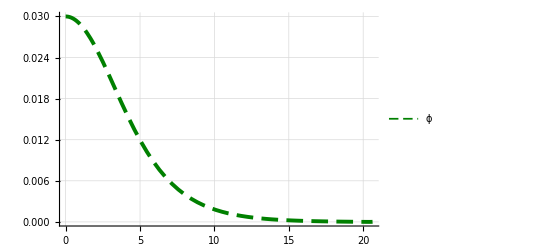

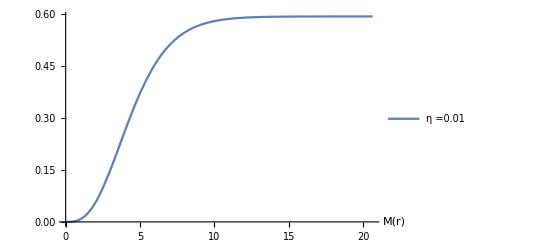

```mathematica
Plot[{Evaluate[φ[r]/.s]},{r,rMin,rTest},
Background->White,PlotLegends->{"ϕ"},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic]

Plot[{Evaluate[M[r]/.s]},
{r,rMin,rTest},Background->White,PlotLegends->Placed[{"η =0.01"},{0.85,0.6}],PlotRange->Full,
AxesLabel->{"M(r)"}]
```

### Shooting

```mathematica
Subdivide[0.0001,0.0003,5]
```

```mathematica
{0.001,1.00327795425,100,30, -0.3,10^-6},{0.005,1.01682795425,50,30, -0.3,10^-6}
```

```mathematica
{0.01,1.034127962414535,40, 30,0.2,10^-6},{0.01,1.034281562499931014,40,30,0.1,10^-6}
```

```mathematica
Amp={0.01};
prec=30; (* precisión *)
Rmax=25;
Dat={};
η=0.15;
α=1;k=1/16/ π;mS=1;
```

```mathematica
rMin=SetPrecision[10^-8,prec];
rMax=SetPrecision[Rmax,prec];
UP=1.037280866405794011070284370549833496963573835081804283917`30.
LOW=1.034127962414535(*0.9659.8*)
```

1.03728086640579401107028437055

1.03413

```mathematica
For[i=1,i<Length[Amp]+1,i++,
ϕ0=SetPrecision[Amp[[i]],prec]; 
ϕFlat=0;
rStart=rMin;(*rMin;*)
Clear[newStart];

(* start interval for search of omega, fixed by hand *)
omUP=SetPrecision[UP,prec];
omLOW=SetPrecision[LOW,prec];

While[ϕFlat==0,

If[newStart==1, 
newStart=0,
ϕFlat=1 ];

For[rTest =rStart+0.03(*rStart*), rTest <rMax+0.03,rTest+=0.1,
(*Print[rTest];*)
If[newStart==1,Break[]]; (* reiniciando rStart con el nuevo valor donde explotó *)

(*Print["rTest= ", rTest];*)
stop=0;

While[stop==0,

Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];ϕFlat=1;Break[],
SetPrecision[(omUP-omLOW)/2,prec]<10^-prec, (* Fijando la maxima precision *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];ϕFlat=1;Abort[]
           ];

w=SetPrecision[(omLOW+omUP)/2,prec];

(*Print[w];*)

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rTest+1},Method->{"EquationSimplification"->"Residual"}];

stop=1;

Do[
Which[Evaluate[φ[rp]/.s][[1]]>2ϕ0||Evaluate[φ[rp]/.s][[1]]>Evaluate[φ[rp-0.01]/.s][[1]],
stop=0;
Print["Pos"];
omLOW=SetPrecision[w,prec];
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[] (* Sale del ciclo Do *),
Evaluate[φ[rp]/.s][[1]]<-2ϕ0||Evaluate[φ[rp]/.s][[1]]<0,
stop=0;
Print["Neg"];
omUP=SetPrecision[w,prec];
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[](* Sale del ciclo Do *)
](* End Which*),{rp,rMin+0.03,rTest}
](* End Do *)
](* End While *)
 ](* End For that change the rTest value *)
];(* End While ϕFlat==0 *)
Print["Encontrado"];
Print[w];
AppendTo[Dat,{ϕ0,w,rTest,prec,η,rMin}];
](* End For that choose the ϕ0 value *);
```

```mathematica
{0.001,1.0206045617675780925548510019718051466952601913362741470337`30.,19,-0.3,10^-8}
```

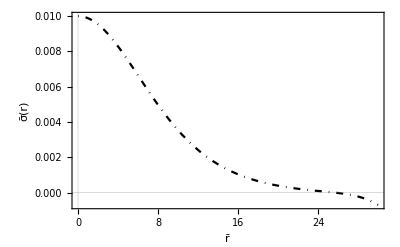

```mathematica
Plot[{Evaluate[φ[x]/.s]},{x,rMin,30},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
w
```

1.01563863730948933176722115386

```mathematica
{0.001,1.00327795425,100,30, -0.3,10^-6},{0.005,1.01682795425,50,30, -0.3,10^-6}
```

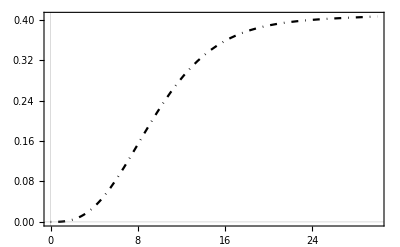

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; 

Plot[{Evaluate[M[x]/.s]},{x,rMin,rMax},
Background->White,
PlotRange->Full,BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
Evaluate[M[rMax]/.s]
```

{0.326102}

```mathematica
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]
```

0.880272

```mathematica
(*{{0.0001000000000000000047921736023859295983129413798451423645`30.,1.110352927917918848532696785014195484109222888946533203125`30.,6.7(*10.060999999999996*),30,0.3,0.001`30.},{0.000299999999999999973718939338951372519659344106912612915`30.,1.110352927917918848532696785014195484109222888946533203125`30.,7(*9*),30,0.3,0.001`30.}
,{0.0010000000000000000208166817117216851329430937767028808594`30.,1.1067734375000000948338629847000902373110875487327575683594`30.,6.060000999999995,30,0.3,10^-5},
{0.0010000000000000000208166817117216851329430937767028808594`30.,1.1074284429028717920039445862454008384645476326113566756248`30.,7.860000999999989,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0025999999999999998806510248527956719044595956802368164062`30.,1.1084926757812499508067116682497044166666455566883087158203`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-5},
{0.0027999999999999999715505349939803636516444385051727294922`30.,1.108381542968750053902368679636936121823964640498161315918`30.,6.0600009999999935,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-5},{0.0030000000000000000624500451351650553988292813301086425781`30.,1.1083736328125000547735468092724886446376331150531768798828`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-5}, {0.0032000000000000001533495552763497471460141241550445556641`30.,1.1082471289062500808056399570489247707882896065711975097656`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0035000000000000000728583859910258979653008282184600830078`30.,1.1083622563526349452473666158312046904355898865879304082682`30.,6.0600009999999935,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-5},{0.0037999999999999999923672167057020487845875322818756103516`30.,1.10836493998318918350680385162483664387989001909318176331`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},
{0.0041999999999999997404853679938696586759760975837707519531`30.,1.10811562499999995135002706092564039863646030426025390625`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0043000000000000000027755575615628913510590791702270507812`30.,1.106422187499999938709027702543608029372990131378173828125`30.,6.0600009999999935,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-5},{0.0050000000000000001040834085586084256647154688835144042969`30.,1.1061920312499999401179007207929316791705787181854248046875`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},
{0.0060000000000000001249000902703301107976585626602172851562`30.,1.105537500000000041000536299407031037844717502593994140625`30.,6.0600009999999935,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.0070000000000000001457167719820517959306016564369201660156`30.,1.1051026855468749630667830985419897160682012327015399932861`30.,6.060000999999995,30,0.3,0.0000100000000000000000000000000000000000000000000000000009`30.},{0.008500000000000000610622663543836097232997417449951171875`30.,1.1049718749999999818645068927480679121799767017364501953125`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},
{0.01,1.103209999699891,6(*7.8*),30,0.3,10^-6},{0.0114999999999999998057109706905976054258644580841064453125`30.,1.102275528862404596619484209440997801721096038818359375`30.,6.060000999999995,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},
{0.01499999999999999944488848768742172978818416595458984375`30.,1.0957342334335000710865415385342203080654144287109375`30.,5.5(*7*),30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},
{0.01650000000000000077715611723760957829654216766357421875`30.,1.11875000000000002220446049250313080847263336181640625`30.,8.9,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},
{0.01700000000000000122124532708767219446599483489990234375`30.,1.119124999999999980904163976447307504713535308837890625`30.,7.5,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.01750000000000000166533453693773481063544750213623046875`30.,1.1181499999999999772626324556767940521240234375`30.,8.3,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},

{0.018,1.119,8.5,30,0.3,10^-6},{0.02,1.1208,8.5,30,0.3,10^-6},{0.022,1.123,8.5,30,0.3,10^-6},{0.024,1.124,8.5,30,0.3,10^-6},{0.026,1.126,8.5,30,0.3,10^-6},{0.028,1.1287,8.5,30,0.3,10^-6},{0.03,1.131,8.5,30,0.3,10^-6},{0.032,1.1329,8.5,30,0.3,10^-6},{0.034,1.1356,8.5,30,0.3,10^-6},{0.036,1.139,8.5,30,0.3,10^-6},{0.038,1.142,8.5,30,0.3,10^-6},
{0.03819999999999999784616733222719631157815456390380859375`30.,1.141917218749999907156933431906509213149547576904296875`30.,8.010001000000008,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.038499999999999999500399638918679556809365749359130859375`30.,1.139519887433654450798981984249977952974907172145613287739`30.,7,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.038999999999999999944488848768742172978818416595458984375`30.,1.1382210174447043990351756760289065375684538643273960301093`30.,6.79,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},

{0.040000000000000000832667268468867405317723751068115234375`30.,1.107656206,5,30,0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.041, 1.101097,4.6(*4.65*),30,0.3,10^-6}};*)
```

```mathematica
{0.01,1.0339767,40,30,0.3,0.4*10^-5}
```

```mathematica
(*
Rama incorrecta ejemplo;
prec=30;
η=0.3; α=1;
k=1/16/ π;
mS=1;
rMin=10^-5;
ϕ0=0.01;
 w=1.11656;(*1.02*)
rMax=10;
*)
```

```mathematica
1.01682795425
```

```mathematica
{0.002,1.0065992795425,100,30,-0.3,10^-6}
```

```mathematica
{0.003,1.0099653094893317,100,30,-0.3,10^-6}
```

```mathematica
{0.004,1.013376373094893317,60,30,-0.3,10^-6}
```

```mathematica
Sol={0.035,1.129168,18,30,0.3,10^-8};
```

```mathematica
{{0.01,1.0339767,31,30.,0.3,4.000000000000001*^-6},{0.01,1.034127962414535,40, 30,0.2,10^-6},{0.01,1.0341638231014,35,30,0.18,10^-6},{0.01,1.034168231014,35,30,0.17,10^-6},{0.01,1.034178231014,35,30,0.16,10^-6},{0.01,1.0342099931014,40, 30,0.15,10^-6},{0.01,1.034281562499931014,40,30,0.1,10^-6}}
```

```mathematica
prec=30;
η=0.16; α=1;
k=1/16/ π;
mS=1;
rMin=10^-6;
ϕ0=0.01;
 w=1.034178231014;(* 1.034127962414535 *)
rMax=35;
s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
(*
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}]; w2=w*B[[1,1,1,2]]
*)
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

```mathematica
Evaluate[r^2 gg[r]^5 NN[r]^2 (1.0695246135032463 gg[r]^2 φ[r]^2-NN[r]^2 φ'[r]^2)^3/.s]/.r-> rMax
```

{3.84151×10^-21}

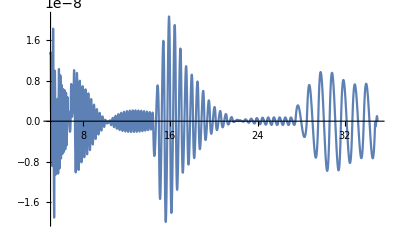

```mathematica
Plot[Evaluate[ϕ''[r]-(-w^6 gg[r]^11 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ[r]^7+9 η NN[r]^7 gg'[r] (NN[r]+2 r NN'[r]) ϕ'[r]^7+w^6 gg[r]^8 ϕ[r]^6 gg'[r] (-2 r w^2 η ϕ[r]+(r^2 α+η) NN[r]^2 ϕ'[r])+w^4 gg[r]^9 ϕ[r]^5 (w^4 η ϕ[r]^2-w^2 NN[r] ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]+3 NN[r]^2 (w^2 (r^2 α+η)-m^2 r^2 NN[r]^2) ϕ'[r]^2)+w^2 gg[r]^7 NN[r] ϕ[r]^3 ϕ'[r] (w^4 η ϕ[r]^3 NN'[r]-3 w^4 η ϕ[r]^2 (3 NN[r]+2 r NN'[r]) ϕ'[r]+w^2 NN[r] ϕ[r] (4 r w^2 η+6 r α NN[r]^2+3 (r^2 α+η) NN[r] NN'[r]) ϕ'[r]^2+3 NN[r]^3 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^3)+w^2 gg[r]^4 NN[r]^3 ϕ[r]^2 ϕ'[r]^3 (70 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (15 ϕ[r] gg'[r]-38 r gg'[r] ϕ'[r]-4 r ϕ[r] gg''[r]))-gg[r]^2 NN[r]^5 ϕ'[r]^5 (58 r w^2 η ϕ[r]^2 gg'[r] NN'[r]+(r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (23 ϕ[r] gg'[r]-16 r gg'[r] ϕ'[r]-2 r ϕ[r] gg''[r]))+w^4 gg[r]^6 NN[r] ϕ[r]^4 ϕ'[r] (2 r w^2 η ϕ[r]^2 gg'[r] NN'[r]-3 (r^2 α+η) NN[r]^3 gg'[r] ϕ'[r]^2+w^2 η NN[r] ϕ[r] (-ϕ[r] gg'[r]+24 r gg'[r] ϕ'[r]+2 r ϕ[r] gg''[r]))-η gg[r] NN[r]^6 ϕ'[r]^5 (4 r w^2 ϕ[r]^2 gg'[r]^2+3 NN[r] ϕ'[r]^2 (3 NN'[r]+2 r NN''[r]))-gg[r]^5 NN[r]^2 ϕ[r] ϕ'[r] (8 r w^6 η ϕ[r]^5 gg'[r]^2-w^4 η NN[r] ϕ[r]^2 (19 NN[r]+24 r NN'[r]) ϕ'[r]^3+3 w^2 NN[r]^3 ϕ[r] (2 r α NN[r]+(r^2 α+η) NN'[r]) ϕ'[r]^4+NN[r]^4 (-w^2 (r^2 α+η)+m^2 r^2 NN[r]^2) ϕ'[r]^5+w^4 η ϕ[r]^3 ϕ'[r]^2 (28 r NN'[r]^2+NN[r] (23 NN'[r]+14 r NN''[r])))+gg[r]^3 NN[r]^4 ϕ'[r]^3 (12 r w^4 η ϕ[r]^4 gg'[r]^2+w^2 η NN[r] ϕ[r] (-11 NN[r]+14 r NN'[r]) ϕ'[r]^3+NN[r]^2 (-4 r w^2 η+2 r α NN[r]^2+(r^2 α+η) NN[r] NN'[r]) ϕ'[r]^4+w^2 η ϕ[r]^2 ϕ'[r]^2 (-4 r NN'[r]^2+NN[r] (31 NN'[r]+20 r NN''[r]))))/(gg[r] NN[r]^2 (w^6 (r^2 α+η) gg[r]^8 ϕ[r]^6-2 r w^6 η gg[r]^5 ϕ[r]^6 gg'[r]+2 r w^2 η gg[r] NN[r]^4 ϕ[r]^2 gg'[r] ϕ'[r]^4+3 η NN[r]^5 (NN[r]+2 r NN'[r]) ϕ'[r]^6-w^4 gg[r]^6 ϕ[r]^4 (w^2 η ϕ[r]^2-12 r w^2 η ϕ[r] ϕ'[r]+3 (r^2 α+η) NN[r]^2 ϕ'[r]^2)+w^2 gg[r]^4 NN[r] ϕ[r]^2 ϕ'[r]^2 (42 r w^2 η ϕ[r]^2 NN'[r]+3 (r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (9 ϕ[r]-16 r ϕ'[r]))-gg[r]^2 NN[r]^3 ϕ'[r]^4 (16 r w^2 η ϕ[r]^2 NN'[r]+(r^2 α+η) NN[r]^3 ϕ'[r]^2+w^2 η NN[r] ϕ[r] (11 ϕ[r]-4 r ϕ'[r]))))/.s],{r,5,rMax}]
```

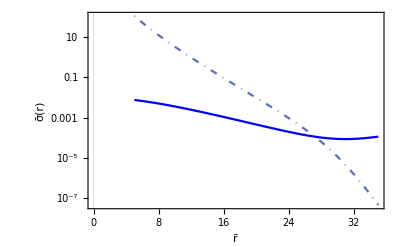

```mathematica
LogPlot[{Evaluate[φ[r]/.s], Evaluate[Exp[-r]/(1.0695246135032463 gg[r]^2 φ[r]^2-NN[r]^2 φ'[r]^2)/.s]},{r,5,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
datos={};
Do[
AppendTo[datos,{r,Last@Evaluate[φ[r]/.s1]}],{r,rMin,rMax,0.1}]
ListPlot[datos,PlotRange->All]
Export["datosX_01_Meta.dat",datos]
```

```mathematica
radio=10^Subdivide[-8,0.3010299956639812,200];
test={};
Do[AppendTo[test,{radio[[i]],(Evaluate[φ[x]/.s]/.x-> radio[[i]])[[1]]}],{i,1,Length[radio] }]
```

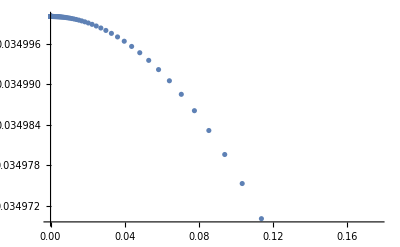

```mathematica
ListPlot[test]
```

```mathematica
Export["config.dat",test]
```

config.dat

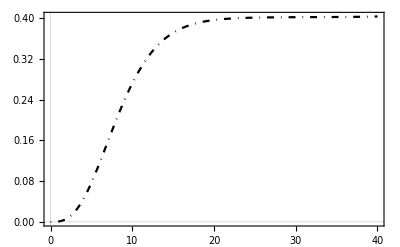

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; 

Plot[{Evaluate[M[x]/.s]},{x,rMin,rMax},
Background->White,
PlotRange->Full,BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]]
```

1.15497

```mathematica
Evaluate[0.95 M[rMax]/.s]
```

{0.38358}

```mathematica
gg^2 NN^2+120 n π (dϕ^2 NN^2-gg^2 ϕ^2 ω^2)
```

```mathematica
ω^2+120 n π (-ϕ^2 ω^2)//Simplify
```

(1-120 n π ϕ^2) ω^2

```mathematica
N@Reduce[{ω^2+120 n π (-ϕ^2 ω^2)>0//Simplify,ϕ>0, n>0},ϕ]//Simplify
```

0.<ϕ<0.0515032 √(1/n)&&ω≠0&&n>0

```mathematica
0.051503226936425284 √(1/0.3)
```

0.0940316

### Grap. data

```mathematica
Etam03={{0.001,1.00327795425,100,30, -0.3,10^-6},{0.002,1.0065992795425,100,30,-0.3,10^-6},{0.003,1.0099653094893317,100,30,-0.3,10^-6},{0.004,1.013376373094893317,60,30,-0.3,10^-6},{0.005,1.01682795425,50,30, -0.3,10^-6},{0.007,1.02389,40,30,-0.3,10^-6},{0.008,1.0274865425,40,30,-0.3,10^-6},{0.0100000000000000002081668171172168513294309377670288085938`30.,1.0348056388499999591612521498973364941775798797607421875`30.,30.06000100000016,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.012,1.04238036,30,30,-0.3,10^-8},{0.015,1.054140552042320860,28,30,-0.3,10^-8},(*{0.02,1.074760624191178130,20},*){0.02,1.074796,22,30,-0.3,10^-8},{0.025,1.09712,20,30,-0.3,10^-8},{0.028,1.11125,20,30,-0.3,10^-8},{0.03,1.121058474193216440,20,30,-0.3,10^-8},{0.04,1.174833438401539430,15,30,-0.3,10^-8},{0.042,1.186734863795236990,15,30,-0.3,10^-8},{0.044,1.198901393441151350,15,30,-0.3,10^-8},{0.046,1.211475043101943020,15,30,-0.3,10^-8},{0.048,1.224599874351943020,13,30,-0.3,10^-8},{0.05,1.237984515572627000,20,30,-0.3,10^-8},{0.052,1.251893037561304990,15,30,-0.3,10^-8},{0.054,1.266234688733179990,15,30,-0.3,10^-8},{0.056,1.281072774116740500,15,30,-0.3,10^-8},{0.058,1.29647849577556370,15,30,-0.3,10^-8},{0.06,1.312416969032435360,15,30,-0.3,10^-8},{0.07,1.400834043125450540,15,30,-0.3,10^-8},(*{0.08,1.506548501472502910,10},*){0.09,1.633103038331351740,10,30,-0.3,10^-8}};
```

```mathematica
Eta03={{0.0001,1.0003256,300,30,0.3,10^-6},{0.0003,1.00097822,300,30,0.3,10^-5},{0.0005,1.0016320024721,200,30,0.3,10^-5},{0.0007,1.0022864,200,30,0.3,10^-5},{0.0009,1.002942,134,30,0.3,10^-5},{0.001,1.0032707,150,30,0.3,10^-6},{0.0013,1.0042575,134,30,0.3,10^-5},{0.0015,1.004917,100,30,0.3,10^-5},{0.0017,1.005576,100,30,0.3,10^-5},{0.0019,1.006238,100,30,0.3,10^-5},{0.003,1.0098975,100,30,0.3,10^-5},{0.0033600000000000001393329895904571458231657743453979492188`30.,1.0111022236378974659070693978233251520989405591228594391701`30.,60.06000999999994,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.005,1.01663845,80,30,0.3,10^-5},{0.006,1.0200514,80,30,0.3,10^-5},{0.0065,1.0217684,70,30,0.3,10^-5},{0.0067,1.022456,50,30,0.3,10^-5}(*{0.00672,1.022514089,40,30,0.3,10^-5}*),{0.00673,1.02256,40,30,0.3,0.4*10^-5},{0.00675,1.02262,40,30,0.3,0.4*10^-5},
{0.00678,1.02273,40,30,0.3,0.4*10^-5},{0.0068,1.022791,40,30,0.3,0.4*10^-5},{0.0069,1.023137,40,30,0.3,0.4*10^-5},
{0.007,1.023484,40,30,0.3,0.4*10^-5},{0.0072,1.02418,40,30,0.3,0.4*10^-5},{0.0074,1.02487,40,30,0.3,0.4*10^-5},{0.0076,1.02556,40,30,0.3,0.4*10^-5}, {0.0078,1.02626,40,30,0.3,0.4*10^-5},{0.008,1.02695,40,30,0.3,0.4*10^-5},
{0.0086,1.02905,40,30,0.3,0.4*10^-5},{0.0088,1.029753,40,30,0.3,0.4*10^-5},{0.009,1.03045,40,30,0.3,0.4*10^-5},{0.0094,1.0318568,40,30,0.3,0.4*10^-5},{0.01,1.0339767,40,30,0.3,0.4*10^-5},{0.010009,1.03401,30,30,0.3,0.4*10^-5},{0.0102,1.03467,30,30,0.3,0.4*10^-5},{0.0107,1.03644,30,30,0.3,0.4*10^-5},{0.0109,1.03721,25,30,0.3,10^-8},{0.011,1.03751,30,30,0.3,10^-8},{0.0115,1.0393,30,30,0.3,10^-6},{0.012,1.04109,30,30,0.3,10^-6},{0.015,1.051985,30,30,0.3,10^-6},{0.018,1.063106,25,30,0.3,10^-6},{0.019,1.06687,25,30,0.3,10^-6},{0.02,1.070633,25,30,0.3,10^-6},{0.022,1.078203,20,30,0.3,10^-6},{0.025,1.08979,20,30,0.3,10^-8},{0.03,1.10939,20,30,0.3,10^-8},{0.031,1.1134,20,30,0.3,10^-8},{0.032,1.11734,20,30,0.3,10^-8},{0.033,1.1213,20,30,0.3,10^-8},{0.034,1.12524,20,30,0.3,10^-8},{0.035,1.129168,18,30,0.3,10^-8}};(*0.4*10^-5*)
```

```mathematica
Eta0={{{0.0070000000000000001457167719820517959306016564369201660156`30.,1.0236949076085106634778022766113281249999287654198186156132`30.,50.01000099999998,30,0,1.0000000000000000000000000000000000000000000000000001`30.*^-6},0.01,1.034412192404270000, 30},{0.015,1.053128048211801000, 30},{0.02,1.072913394785428000,30},{0.03,1.116036581602133000,30},{0.04,1.164470770285790000,30},{0.042,1.174863039742705000,30},{0.044,1.1855066510200170,30},{0.046,1.1964083784949690,30},{0.048,1.2075765100358490,30},{0.05,1.219018571342151000,30},{0.052,1.230742623941348000,30},{0.054,1.242757501645907000,30},{0.056,1.255071652560727000,30},{0.058,1.267694320796101000,30},{0.06,1.280634958841730000,30},{0.07,1.350463702269447000,30},{0.08,1.429880054976501000,23},{0.09,1.520545101912098000,25},{0.1,1.624469884859628000,29},{0.15,2.449966765699886000,22}};
```

Plot the profile of phi

```mathematica
(*rMin=SetPrecision[AA[[6]],prec];
ϕ0=SetPrecision[AA[[1]],prec];
w=SetPrecision[AA[[2]],prec];
rMax=SetPrecision[AA[[3]],prec];
*)
```

```mathematica
Dat={{0.001,1.0208604561767578092554851,18,30, -0.3,10^-8}};
```

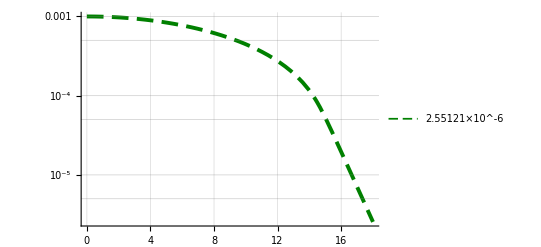

```mathematica
Table[
AA=Dat[[i]];
prec=AA[[4]];
η= AA[[5]]; 
α=1;k=1/16/ π;mS=1;
rMin=AA[[6]];
ϕ0=AA[[1]];
w=AA[[2]];
rMax=AA[[3]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

(*s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];*)

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)]; 
(*φ*)
LogPlot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s](*AA[[1]]*)},
PlotRange->All(*{Automatic,{0,0.001}}*),
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[Dat]}](*Length[Dat]*)
```

## Shooting M

```mathematica
Eta03={(*{0.0001,1.0003256,280,30.,0.3,1.*^-6},{0.0003,1.00097822,200,30.,0.3,0.00001},{0.0005,1.0016320024721,140,30.,0.3,0.00001},{0.0007,1.0022864,140,30.,0.3,0.00001},{0.0009,1.002942,100,30.,0.3,0.00001},{0.001,1.0032707,100,30.,0.3,1.*^-6},*){0.0013,1.0042575,100,30.,0.3,0.00001},{0.0015,1.004917,80,30.,0.3,0.00001},{0.0017,1.005576,80,30.,0.3,0.00001},{0.0019,1.006238,80,30.,0.3,0.00001},{0.0019200000000000000486416462663896709273103624582290649414`30.,1.0063048134765624746361778463210612244438380002975463867188`30.,75.06000999999995,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.0020960000000000002066957716095885189133696258068084716797`30.,1.0068878671875000716667836186957174504641443490982055664062`30.,75.06000999999955,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.0022720000000000001479094624556864800979383289813995361328`30.,1.0074718750000000652700116177120791011393101357334314644903`30.,75.0600099999991,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.0024480000000000000891231533017844412825070321559906005859`30.,1.0080575282258782468841106218249642788361630848067505777995`30.,75.06000999999961,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.003,1.0098975,75,30.,0.3,0.00001},{0.0033600000000000001393329895904571458231657743453979492188`30.,1.0111022236378974659070693978233251520989405591228594391701`30.,60.06000999999994,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.0044399999999999995026200849679298698902130126953125`30.,1.0147393188476561796550114852299984136152488645166158676147`30.,60.06000999999977,30,0.3,0.0000100000000000000008180305391403130954586231382563710213`30.},{0.0048,1.0159673247879243105677995312609030238373984048934469748719`30.,45,30,0.3,10^-5},{0.005,1.01663845,55,30.,0.3,0.00001},{0.006,1.0200514,60,30.,0.3,0.00001},{0.0065,1.0217684,50,30.,0.3,0.00001},{0.0067,1.022456,40,30.,0.3,0.00001},{0.00672,1.022514089,40.,30.,0.3,0.00001},{0.00673,1.02256,40.,30.,0.3,4.000000000000001*^-6},{0.00675,1.02262,40.,30.,0.3,4.000000000000001*^-6},{0.00678,1.02273,40.,30.,0.3,4.000000000000001*^-6},{0.0068,1.022791,40.,30.,0.3,4.000000000000001*^-6},{0.0069,1.023137,40.,30.,0.3,4.000000000000001*^-6},{0.007,1.023484,40.,30.,0.3,4.000000000000001*^-6},{0.0072,1.02418,40.,30.,0.3,4.000000000000001*^-6},{0.0074,1.02487,40.,30.,0.3,4.000000000000001*^-6},{0.0076,1.02556,35,30.,0.3,4.000000000000001*^-6},{0.0078,1.02626,40.,30.,0.3,4.000000000000001*^-6},{0.008,1.02695,31,30.,0.3,4.000000000000001*^-6},{0.0086,1.02905,31,30.,0.3,4.000000000000001*^-6},{0.0088,1.029753,31,30.,0.3,4.000000000000001*^-6},{0.009,1.03045,31,30.,0.3,4.000000000000001*^-6},{0.0094,1.0318568,31,30.,0.3,4.000000000000001*^-6},{0.01,1.0339767,31,30.,0.3,4.000000000000001*^-6},{0.010009,1.03401,30.,30.,0.3,4.000000000000001*^-6},{0.0102,1.03467,30.,30.,0.3,4.000000000000001*^-6},{0.0107,1.03644,30.,30.,0.3,4.000000000000001*^-6},{0.0109,1.03721,25.,30.,0.3,1.*^-8},{0.011,1.03751,30.,30.,0.3,1.*^-8},{0.0115,1.0393,30.,30.,0.3,1.*^-6},{0.012,1.04109,30.,30.,0.3,1.*^-6},{0.015,1.051985,25,30.,0.3,1.*^-6},{0.018,1.063106,20,30.,0.3,1.*^-6},{0.019,1.06687,20,30.,0.3,1.*^-6},{0.02,1.070633,20,30.,0.3,1.*^-6},{0.022,1.078203,20.,30.,0.3,1.*^-6},{0.025,1.08979,17,30.,0.3,1.*^-8},{0.03,1.10939,15,30.,0.3,1.*^-8},{0.031,1.1134,20.,30.,0.3,1.*^-8},{0.032,1.11734,16,30.,0.3,1.*^-8},{0.033,1.1213,16,30.,0.3,1.*^-8},{0.034,1.12524,16,30.,0.3,1.*^-8},{0.035,1.129168,18.,30.,0.3,1.*^-8}};
```

```mathematica
Etam03={{0.001,1.00327795425,100,30, -0.3,10^-6},{0.002,1.0065992795425,100,30,-0.3,10^-6},{0.003,1.0099653094893317,100,30,-0.3,10^-6},{0.004,1.013376373094893317,60,30,-0.3,10^-6},{0.005,1.01682795425,50,30, -0.3,10^-6},{0.007,1.02389,40,30,-0.3,10^-6},{0.008,1.0274865425,40,30,-0.3,10^-6},{0.0100000000000000002081668171172168513294309377670288085938`30.,1.0348056388499999591612521498973364941775798797607421875`30.,30.06000100000016,30,-0.3,1.0000000000000000000000000000000000000000000000000001`30.*^-6},{0.012,1.04238036,30,30,-0.3,10^-8},{0.015,1.054140552042320860,28,30,-0.3,10^-8},(*{0.02,1.074760624191178130,20},*){0.02,1.074796,22,30,-0.3,10^-8},{0.025,1.09712,20,30,-0.3,10^-8},{0.028,1.11125,20,30,-0.3,10^-8},{0.03,1.121058474193216440,20,30,-0.3,10^-8},{0.04,1.174833438401539430,15,30,-0.3,10^-8},{0.042,1.186734863795236990,15,30,-0.3,10^-8},{0.044,1.198901393441151350,15,30,-0.3,10^-8},{0.046,1.211475043101943020,15,30,-0.3,10^-8},{0.048,1.224599874351943020,13,30,-0.3,10^-8},{0.05,1.237984515572627000,20,30,-0.3,10^-8},{0.052,1.251893037561304990,15,30,-0.3,10^-8},{0.054,1.266234688733179990,15,30,-0.3,10^-8},{0.056,1.281072774116740500,15,30,-0.3,10^-8},{0.058,1.29647849577556370,15,30,-0.3,10^-8},{0.06,1.312416969032435360,15,30,-0.3,10^-8},{0.07,1.400834043125450540,15,30,-0.3,10^-8},(*{0.08,1.506548501472502910,10},*){0.09,1.633103038331351740,10,30,-0.3,10^-8}};
```

```mathematica
Bs=Etam03;
```

1

cumple con ϕ<10^-3

r→53.5231

masa95 = 0.13806

2

cumple con ϕ<10^-3

r→37.8329

masa95 = 0.194432

3

cumple con ϕ<10^-3

r→30.8509

masa95 = 0.237042

4

cumple con ϕ<10^-3

r→26.4995

masa95 = 0.271926

5

cumple con ϕ<10^-3

r→23.9573

masa95 = 0.304097

6

cumple con ϕ<10^-3

r→19.8272

masa95 = 0.354124

7

cumple con ϕ<10^-3

r→18.5872

masa95 = 0.377424

8

cumple con ϕ<10^-3

r→16.8747

masa95 = 0.421489

9

cumple con ϕ<10^-3

r→15.1005

masa95 = 0.454044

10

cumple con ϕ<10^-3

r→13.181

masa95 = 0.496469

11

cumple con ϕ<10^-3

r→11.4516

masa95 = 0.562171

12

cumple con ϕ<10^-3

r→9.87688

masa95 = 0.60594

13

cumple con ϕ<10^-3

r→9.33467

masa95 = 0.632776

14

cumple con ϕ<10^-3

r→8.9595

masa95 = 0.647296

15

cumple con ϕ<10^-3

r→7.49527

masa95 = 0.703761

16

cumple con ϕ<10^-3

r→7.19672

masa95 = 0.709479

17

cumple con ϕ<10^-3

r→7.00217

masa95 = 0.717998

18

cumple con ϕ<10^-3

r→6.81779

masa95 = 0.725622

19

cumple con ϕ<10^-3

r→6.57217

masa95 = 0.729292

20

cumple con ϕ<10^-3

r→6.41861

masa95 = 0.73612

21

cumple con ϕ<10^-3

r→6.24562

masa95 = 0.740885

22

cumple con ϕ<10^-3

r→6.09984

masa95 = 0.745904

23

cumple con ϕ<10^-3

r→5.96916

masa95 = 0.750565

24

cumple con ϕ<10^-3

r→5.79896

masa95 = 0.752791

25

cumple con ϕ<10^-3

r→5.64582

masa95 = 0.754862

26

cumple con ϕ<10^-3

r→5.02472

masa95 = 0.761086

27

cumple con ϕ<10^-3

r→4.05158

masa95 = 0.745321

{{53.5231,0.13806},{37.8329,0.194432},{30.8509,0.237042},{26.4995,0.271926},{23.9573,0.304097},{19.8272,0.354124},{18.5872,0.377424},{16.8747,0.421489},{15.1005,0.454044},{13.181,0.496469},{11.4516,0.562171},{9.87688,0.60594},{9.33467,0.632776},{8.9595,0.647296},{7.49527,0.703761},{7.19672,0.709479},{7.00217,0.717998},{6.81779,0.725622},{6.57217,0.729292},{6.41861,0.73612},{6.24562,0.740885},{6.09984,0.745904},{5.96916,0.750565},{5.79896,0.752791},{5.64582,0.754862},{5.02472,0.761086},{4.05158,0.745321}}

{{0.001,0.996529},{0.002,0.993056},{0.003,0.989586},{0.004,0.986121},{0.005,0.982588},{0.007,0.975727},{0.008,0.972221},{0.0100000000000000002081668171172,0.965016},{0.012,0.958265},{0.015,0.948119},{0.02,0.930533},{0.025,0.913921},{0.028,0.903481},{0.03,0.896736},{0.04,0.86325},{0.042,0.857066},{0.044,0.850389},{0.046,0.843776},{0.048,0.837702},{0.05,0.831037},{0.052,0.824653},{0.054,0.818179},{0.056,0.811743},{0.058,0.805566},{0.06,0.799397},{0.07,0.768771},{0.09,0.710545}}

{{0.001,0.13806},{0.002,0.194432},{0.003,0.237042},{0.004,0.271926},{0.005,0.304097},{0.007,0.354124},{0.008,0.377424},{0.0100000000000000002081668171172,0.421489},{0.012,0.454044},{0.015,0.496469},{0.02,0.562171},{0.025,0.60594},{0.028,0.632776},{0.03,0.647296},{0.04,0.703761},{0.042,0.709479},{0.044,0.717998},{0.046,0.725622},{0.048,0.729292},{0.05,0.73612},{0.052,0.740885},{0.054,0.745904},{0.056,0.750565},{0.058,0.752791},{0.06,0.754862},{0.07,0.761086},{0.09,0.745321}}

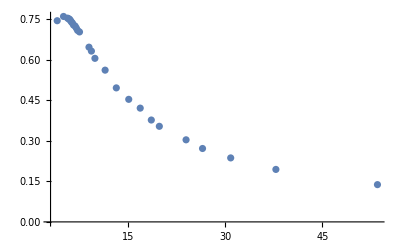

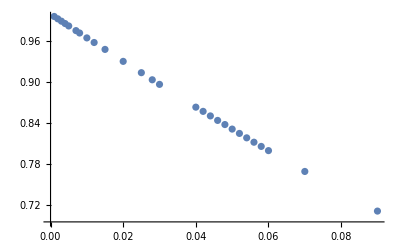

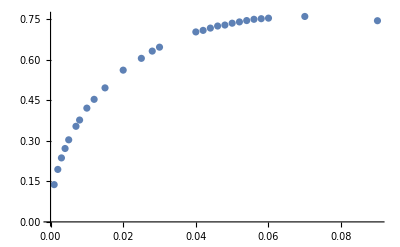

```mathematica
mvsr={};
phivswf={};
wfvsm={};
stop2=0;

For[j=1,j<Length[Bs]+1,j++,
Print[j];

AA=Bs[[j]];
prec=AA[[4]];
η= AA[[5]]; 
α=1;k=1/16/ π;mS=1;
rMin=AA[[6]];
ϕ0=AA[[1]];
w=AA[[2]];
rMax=AA[[3]];

Clear[s,M95, M];

If[stop2≠0,Break[]]; (*Para cuando una frecuencia no es suficientemente pequeña*)

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}](*MaxSteps->10^6*);

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]; 

M95=0.95M[rMax][[1]];

(* comprobando ϕ pequeño *)
If[Evaluate[φ[rMax]/.s][[1]]<4*10^-3,Print["cumple con ϕ<10^-3"],Print["No cumple con ϕ<10^-3"]; Break[]];

(* calculando radio *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];

Print[rad];
Print["masa95 = ", M95];

(* calculando frecuencia*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];

AppendTo[mvsr,{rad[[2]],M95}];
AppendTo[phivswf,{ϕ0,w2}];
AppendTo[wfvsm,{ϕ0,M95}];
](* FOR *)
(* Resultados *)
Speak["Masa encontrada"]

mvsr
phivswf
wfvsm

(* Plot*)
(*Show[{ListPlot[mvsr],Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},PlotRange->Full]}]*)
Show[{ListPlot[mvsr,PlotRange->Full]}]
Show[{ListPlot[phivswf,PlotRange->Full]}]
Show[{ListPlot[wfvsm,PlotRange->Full]}]
```

```mathematica
a=Import["BH_X_sigm_w_03.dat"];
```

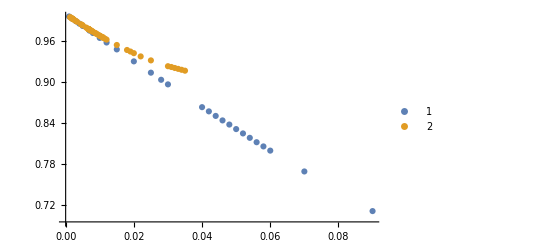

```mathematica
ListPlot[{phivswf,a},PlotLegends->Automatic]
```

```mathematica
Export["BH_X_sigm_w_m03.dat",phivswf]
```

BH_X_sigm_w_m03.dat

```mathematica
mvsr
```

{{46.7486,0.15489},{43.4021,0.165723},{41.0587,0.176483},{38.7311,0.185819},{38.3742,0.186442},{36.7332,0.194329},{35.272,0.201802},{33.8642,0.208657},{30.5531,0.22911},{28.8253,0.241112},{24.9483,0.272448},{23.6713,0.280077},{23.4331,0.286491},{21.2941,0.308908},{20.4135,0.318997},{20.1101,0.323013},{20.4238,0.325594},{20.0493,0.323485},{20.2865,0.32562},{20.034,0.324864},{20.2625,0.326893},{20.0774,0.328576},{19.869,0.330064},{19.4378,0.332776},{19.2438,0.336872},{18.9758,0.340537},{18.6796,0.34343},{18.3909,0.34682},{17.6374,0.355586},{17.3913,0.358262},{17.2473,0.361773},{16.8501,0.367383},{16.2761,0.375123},{16.2395,0.374987},{16.2918,0.379551},{15.9686,0.386491},{15.1907,0.382067},{15.7134,0.38981},{15.2886,0.394893},{14.9994,0.400739},{13.1322,0.42601},{11.7591,0.443958},{11.382,0.448428},{11.1222,0.453939},{10.7982,0.465267},{9.84319,0.469889},{8.78435,0.473038},{8.56873,0.471088},{8.39387,0.470645},{8.22779,0.469603},{8.10294,0.469108},{8.03335,0.469183}}

```mathematica
mvsrN03={{53.52310626249153,0.13806043549517838},{23.957310872923095,0.3040973312781371},{19.827203147529563,0.35412378163899094},{18.587241628770887,0.37442398691852164},{16.824727838125448,0.410886442355284},{15.100472540623612,0.4480440002811779},{13.181038383474181,0.49646868838380365},{11.451634868917818,0.5521711223786711},{9.876879427931923,0.6129397160328044},{9.334672223826924,0.6327764074306256},{8.959500210140206,0.6472955723214572},{7.495268680849711,0.703761312779916},(*{7.196720356395684,0.7094792651395385},*){7.002167050257486,0.7259984853503856}(*,{6.817785399611521,0.7256217780687244}*),(*{6.572168198532722,0.7292919344682613},*){6.418609466331204,0.7431197585757143}(*,{6.245618138435544,0.740885115953607},{6.0998436359880195,0.7459041252453499}*),{5.969163566347131,0.7545649481974795},(*{5.798955321527899,0.7527914523903423},*){5.645820459147397,0.758620375195024},{5.024718643318775,0.7610861448418385},{4.051576771870299,0.7453205997665647}};
```

```mathematica
mvsr={{53.52310626249153,0.13806043549517838},{37.832853603186585,0.19443174265294932},{30.850890622343623,0.23704183454078015},{26.499499300444185,0.2719258094107964},{23.957310872923095,0.2973312781371},{19.827203147529563,0.35412378163899094},{18.587241628770887,0.37742398691852164},{16.874727838125448,0.4134886442355284},{15.100472540623612,0.4540440002811779},{13.181038383474181,0.50046868838380365},{11.451634868917818,0.5521711223786711},{9.876879427931923,0.609397160328044},{9.334672223826924,0.6327764074306256},{8.959500210140206,0.6472955723214572},{7.495268680849711,0.703761312779916},(*{7.196720356395684,0.7094792651395385},*){7.002167050257486,0.720084853503856},(*,{6.817785399611521,0.7256217780687244}*){6.572168198532722,0.7352919344682613},(*,{6.418609466331204,0.7361197585757143},{6.245618138435544,0.740885115953607},{6.0998436359880195,0.7459041252453499}*){5.969163566347131,0.7505649481974795},(*{5.798955321527899,0.7527914523903423},*){5.645820459147397,0.7548620375195024},{5.024718643318775,0.7610861448418385},{4.051576771870299,0.7453205997665647}};
```

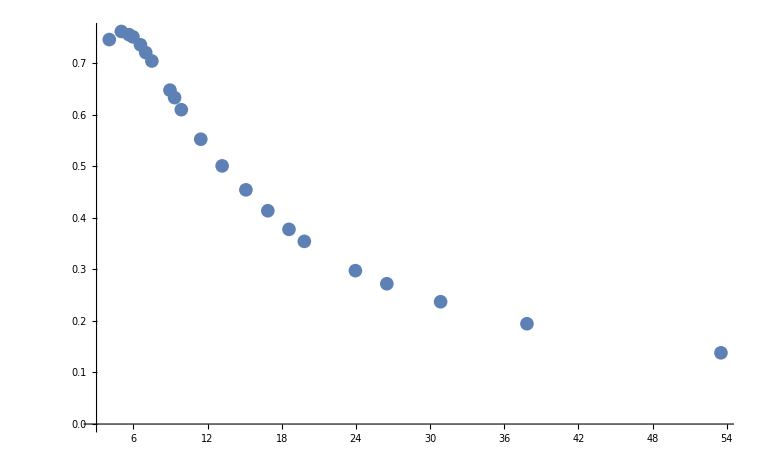

```mathematica
ListPlot[mvsr,PlotRange->All,Joined->False]
```

```mathematica
a=Interpolation[mvsrN03,InterpolationOrder->2,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
FindMaximum[a[r],{r,4.05,53}]
```

{0.761286,{r→5.14747}}

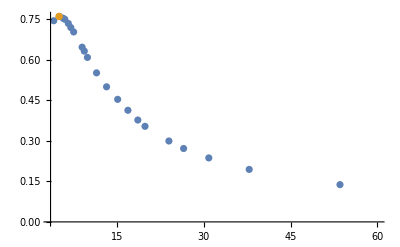

```mathematica
ListPlot[{mvsr,{{4.979709772790546,0.7611233075460803}}},PlotRange->{{3.5,60},Automatic},Joined->False]
```

```mathematica
data={};
Do[AppendTo[data,{r,a[r]}],{r,4.05,53.52,0.3}]
```

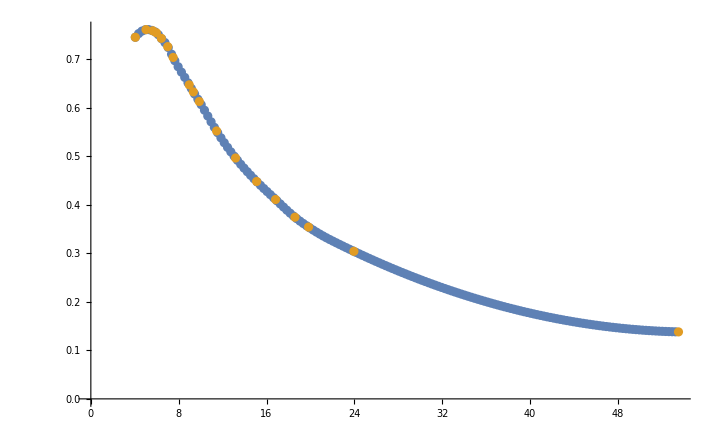

```mathematica
ListPlot[{data,mvsrN03},Joined->False]
```

```mathematica
Export["2Dat_mvsr_etaM03_X.dat",data]
```

2Dat_mvsr_etaM03_X.dat

```mathematica
wfvsm
```

```mathematica
Export["2Func_wM_M03_BH_X.dat",wfvsm]
```

2Func_wM_M03_BH_X.dat

## Test

```mathematica
Etam095={{0.015,1.056098162820875120,30},{0.02,1.078474223653850100,24},{0.03,1.130068266754204690,15},{0.04,1.192692665503986680,15},{
0.042,1.206666952106005572,15},{0.044,1.221221676632986450,15},{0.046,1.236523670039227340,15},{0.048,1.252346865209014160,15},{0.05,1.268799173897911720,15},{0.052,1.286023693423176410,15},{0.054,1.303936397892786200,15},{0.056,1.322625763266247140,15},{0.058,1.342089370200291710,14},{0.06,1.362208100892628850,12},{0.07,1.478895347246726990,15},{0.075,1.547924936440892040,10},{0.08,1.626628268877047360,11},{0.09,1.809654562236914730,6}};
```

```mathematica
{0.02,1.074760624191178130,20}
```

```mathematica
{{0.001,1.11,8.5,50,0.3,10^-3},{0.01,1.11,8,50,0.3,10^-6},{0.013,1.11,7.,50,0.3,10^-6},{0.018,1.12,8.,50,0.3,10^-6},{0.02,1.12,8.,50,0.3,10^-6}};
```

```mathematica
Etam03={{0.007,1.02389,40,30,-0.3,10^-6},{0.015,1.054140552042320860,28,10^-8},(*{0.02,1.074760624191178130,20},*){0.03,1.121058474193216440,20,10^-8},{0.04,1.174833438401539430,15,10^-8},{0.042,1.186734863795236990,15,10^-8},{0.044,1.198901393441151350,15,10^-8},{0.046,1.211475043101943020,15,10^-8},{0.048,1.224599874351943020,13,10^-8},{0.05,1.237984515572627000,20,10^-8},{0.052,1.251893037561304990,15,10^-8},{0.054,1.266234688733179990,15,10^-8},{0.056,1.281072774116740500,15,10^-8},{0.058,1.29647849577556370,15,10^-8},{0.06,1.312416969032435360,15,10^-8},{0.07,1.400834043125450540,15,10^-8},(*{0.08,1.506548501472502910,10},*){0.09,1.633103038331351740,10,10^-8}};
```

```mathematica
{0.01,1.11656,10,30,0.3,10^-5};
```

```mathematica
Bs={0.015,1.054140552042320860,28,30,-0.3,10^-6}
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=Bs[[1]];
w=Bs[[2]];
rMax=Bs[[3]];
rMin=Bs[[6]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

{0.015,1.05414055204232086,28,30,-0.3,1/1000000}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndsz: At r == 5.73906, step size is effectively zero; singularity or stiff system suspected.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {28} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.87727×10^-106

-Graphics-

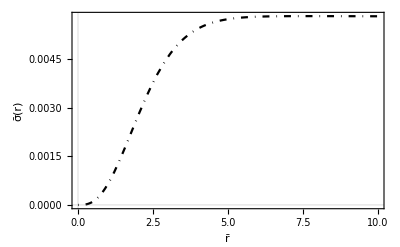

```mathematica
M[r_]:=1/2 r(1-1/gg[r]^2);

Plot[{Evaluate[M[x]/.s]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
Funcphi={};
FuncM={};
Do[AppendTo[Funcphi,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

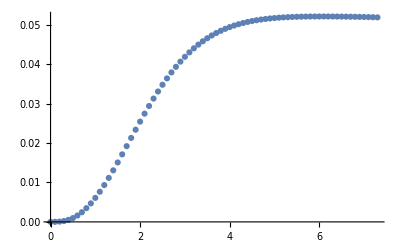

```mathematica
ListPlot[FuncM]
```

```mathematica
120 0.3 π (0.045^2)
```

0.229022

```mathematica
{0.041, 1.101097,4.65,30,0.3,}
```

```mathematica
1.1008
```

```mathematica
prec=30;
η=0.3; α=1;
k=1/16/ π;
mS=1;
rMin=10^-6;
ϕ0=0.045;
 w=1.009951747; 
rMax=4.65; 

sB=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]
```

NDSolve::nderr: Error test failure at r == 1.44337; unable to continue.

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

0.955977

```mathematica
Evaluate[φ[rMax]/.sB]
```

{0.00147447}

```mathematica
(*NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]*)
```

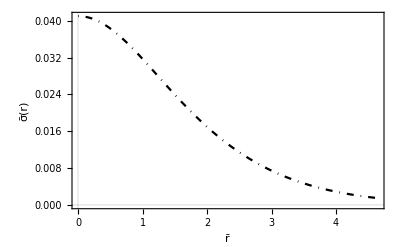

```mathematica
Plot[{Evaluate[φ[x]/.sB]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

-Graphics-

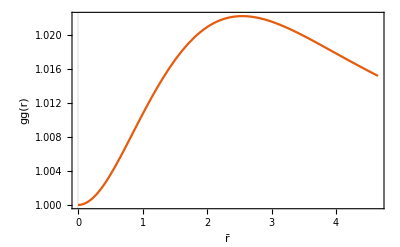

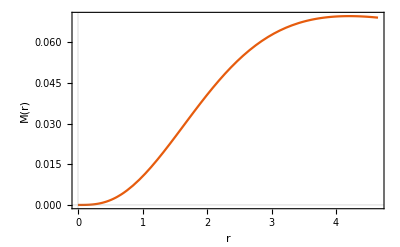

```mathematica
M[r_]:=1/2 r(1-1/gg[r]^2);

Plot[{Evaluate[φ[x]/.sB]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]

Plot[{Evaluate[gg[x]/.sB]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","gg(r)"},BaseStyle->14,PlotTheme->{"Scientific"}]

Plot[{Evaluate[M[r]/.sB]},
{r,rMin,rMax},Background->White,PlotRange->Full,
AxesLabel->{"r","M(r)"},PlotTheme->{"Scientific"}]
```

```mathematica
0.95Evaluate[M[rMax]/.sB]
```

{0.0452071}

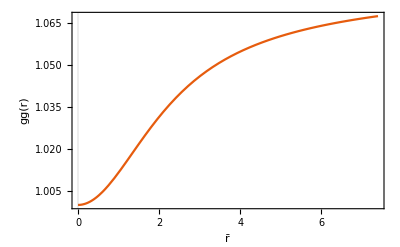

```mathematica
Plot[{Evaluate[NN[x]/.sB]*Evaluate[NN[x]/.sB]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","gg(r)"},BaseStyle->14,PlotTheme->{"Scientific"}]
```

```mathematica
Evaluate[NN[rMax]/.sB]*Evaluate[NN[rMax]/.sB]
```

{1.06735}

```mathematica
NSolve[c Evaluate[NN[rMax]/.sB]*Evaluate[NN[rMax]/.sB]==1,c]
```

{{c→0.936903}}

```mathematica
w*0.9369026668767724
```

1.05664

```mathematica
Funcsigma={};
Do[AppendTo[Funcsigma,{r,Evaluate[φ[r]/.sB][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Export["Funcsigma.dat",Funcsigma]
```

Funcsigma.dat

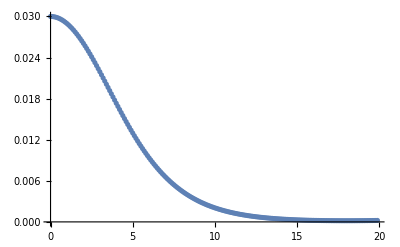

```mathematica
ListPlot[Funcsigma]
```

```mathematica
FuncM={};
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.sB][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Export["FuncM.dat",FuncM]
```

FuncM.dat

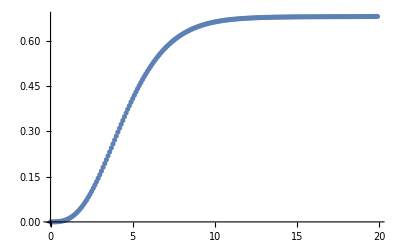

```mathematica
ListPlot[FuncM]
```

### Data

```mathematica
Eta0={{0.01,1.034412192404270000, 30},{0.015,1.053128048211801000, 30},{0.02,1.072913394785428000,30},{0.03,1.116036581602133000,30},{0.04,1.164470770285790000,30},{0.042,1.174863039742705000,30},{0.044,1.1855066510200170,30},{0.046,1.1964083784949690,30},{0.048,1.2075765100358490,30},{0.05,1.219018571342151000,30},{0.052,1.230742623941348000,30},{0.054,1.242757501645907000,30},{0.056,1.255071652560727000,30},{0.058,1.267694320796101000,30},{0.06,1.280634958841730000,30},{0.07,1.350463702269447000,30},{0.08,1.429880054976501000,23},{0.09,1.520545101912098000,25},{0.1,1.624469884859628000,29},{0.15,2.449966765699886000,22}};
```

```mathematica
Eta03={{0.0001,1.0003256,300,30,0.3,10^-6},{0.0003,1.00097834,300,30,0.3,10^-5},{0.0005,1.0016320024721,200,30,0.3,10^-5},{0.0007,1.0022864,200,30,0.3,10^-5},{0.0009,1.002942,134,30,0.3,10^-5},{0.001,1.0032707,150,30,0.3,10^-6},{0.0013,1.0042575,134,30,0.3,10^-5},{0.0015,1.004917,100,30,0.3,10^-5},{0.0017,1.005576,100,30,0.3,10^-5},{0.0019,1.006238,100,30,0.3,10^-5},{0.003,1.0098975,100,30,0.3,10^-5},{0.005,1.01663845,80,30,0.3,10^-5},{0.006,1.0200514,80,30,0.3,10^-5},{0.0065,1.0217684,70,30,0.3,10^-5},{0.0067,1.022456,50,30,0.3,10^-5}(*{0.00672,1.022514089,40,30,0.3,10^-5}*),{0.00673,1.02256,40,30,0.3,0.4*10^-5},{0.00675,1.02262,40,30,0.3,0.4*10^-5},
{0.00678,1.02273,40,30,0.3,0.4*10^-5},{0.0068,1.022791,40,30,0.3,0.4*10^-5},{0.0069,1.023137,40,30,0.3,0.4*10^-5},
{0.007,1.023484,40,30,0.3,0.4*10^-5},{0.0072,1.02418,40,30,0.3,0.4*10^-5},{0.0074,1.02487,40,30,0.3,0.4*10^-5},{0.0076,1.02556,40,30,0.3,0.4*10^-5}, {0.0078,1.02626,40,30,0.3,0.4*10^-5},{0.008,1.02695,40,30,0.3,0.4*10^-5},
{0.0086,1.02905,40,30,0.3,0.4*10^-5},{0.0088,1.029753,40,30,0.3,0.4*10^-5},{0.009,1.03045,40,30,0.3,0.4*10^-5},{0.0094,1.0318568,40,30,0.3,0.4*10^-5},{0.01,1.0339767,40,30,0.3,0.4*10^-5},{0.010009,1.03401,30,30,0.3,0.4*10^-5},{0.0102,1.03467,30,30,0.3,0.4*10^-5},{0.0107,1.03644,30,30,0.3,0.4*10^-5},{0.0109,1.03721,25,30,0.3,0.4*10^-5},{0.011,1.03751,30,30,0.3,0.4*10^-5}};
```

```mathematica
Etam03={{0.015,1.054140552042320860,28},{0.02,1.074760624191178130,20},{0.03,1.121058474193216440,20},{0.04,1.174833438401539430,15},{0.042,1.186734863795236990,15},{0.044,1.198901393441151350,15},{0.046,1.211475043101943020,15},{0.048,1.224599874351943020,13},{0.05,1.237984515572627000,20},{0.052,1.251893037561304990,15},{0.054,1.266234688733179990,15},{0.056,1.281072774116740500,15},{0.058,1.29647849577556370,15},{0.06,1.312416969032435360,15},{0.07,1.400834043125450540,15},{0.08,1.506548501472502910,10},{0.09,1.633103038331351740,10}};
```

## Compact

```mathematica
Eta03={{0.0001,1.0003256,300,30,0.3,10^-6},{0.0003,1.00097822,300,30,0.3,10^-5},{0.0005,1.0016320024721,200,30,0.3,10^-5},{0.0007,1.0022864,200,30,0.3,10^-5},{0.0009,1.002942,134,30,0.3,10^-5},{0.001,1.0032707,150,30,0.3,10^-6},{0.0013,1.0042575,134,30,0.3,10^-5},{0.0015,1.004917,100,30,0.3,10^-5},{0.0017,1.005576,100,30,0.3,10^-5},{0.0019,1.006238,100,30,0.3,10^-5},{0.003,1.0098975,100,30,0.3,10^-5},{0.005,1.01663845,80,30,0.3,10^-5},{0.006,1.0200514,80,30,0.3,10^-5},{0.0065,1.0217684,70,30,0.3,10^-5},{0.0067,1.022456,50,30,0.3,10^-5}(*{0.00672,1.022514089,40,30,0.3,10^-5}*),{0.00673,1.02256,40,30,0.3,0.4*10^-5},{0.00675,1.02262,40,30,0.3,0.4*10^-5},
{0.00678,1.02273,40,30,0.3,0.4*10^-5},{0.0068,1.022791,40,30,0.3,0.4*10^-5},{0.0069,1.023137,40,30,0.3,0.4*10^-5},
{0.007,1.023484,40,30,0.3,0.4*10^-5},{0.0072,1.02418,40,30,0.3,0.4*10^-5},{0.0074,1.02487,40,30,0.3,0.4*10^-5},{0.0076,1.02556,40,30,0.3,0.4*10^-5}, {0.0078,1.02626,40,30,0.3,0.4*10^-5},{0.008,1.02695,40,30,0.3,0.4*10^-5},
{0.0086,1.02905,40,30,0.3,0.4*10^-5},{0.0088,1.029753,40,30,0.3,0.4*10^-5},{0.009,1.03045,40,30,0.3,0.4*10^-5},{0.0094,1.0318568,40,30,0.3,0.4*10^-5},{0.01,1.0339767,40,30,0.3,0.4*10^-5},{0.010009,1.03401,30,30,0.3,0.4*10^-5},{0.0102,1.03467,30,30,0.3,0.4*10^-5},{0.0107,1.03644,30,30,0.3,0.4*10^-5},{0.0109,1.03721,25,30,0.3,10^-8},{0.011,1.03751,30,30,0.3,10^-8},{0.0115,1.0393,30,30,0.3,10^-6},{0.012,1.04109,30,30,0.3,10^-6},{0.015,1.051985,30,30,0.3,10^-6},{0.018,1.063106,25,30,0.3,10^-6},{0.019,1.06687,25,30,0.3,10^-6},{0.02,1.070633,25,30,0.3,10^-6},{0.022,1.078203,20,30,0.3,10^-6},{0.025,1.08979,20,30,0.3,10^-8},{0.03,1.10939,20,30,0.3,10^-8},{0.031,1.1134,20,30,0.3,10^-8},{0.032,1.11734,20,30,0.3,10^-8},{0.033,1.1213,20,30,0.3,10^-8},{0.034,1.12524,20,30,0.3,10^-8},{0.035,1.129168,18,30,0.3,10^-8}};(*0.4*10^-5*)
```

```mathematica
Bs={0.03,1.121058474193216440,20,30,-0.3,10^-8};
```

```mathematica
Bs={0.03,1.10939,20,30,0.3,10^-8};
```

```mathematica
Bs={0.03,1.116036581602133000,30,30,0,10^-8};
```

```mathematica
{{0.03,1.116036581602133000,30,30,0,10^-8},{0.03,1.10939,20,30,0.3,10^-8},{0.03,1.121058474193216440,20,30,-0.3,10^-8}};
```

```mathematica
Dat=%;
```

```mathematica
Bs=Dat;
```

1

0.562329

cumple con ϕ<10^-3

Checking, masa con radio encontrado 8.74764 masa 95, 0.562329 comprobando, True

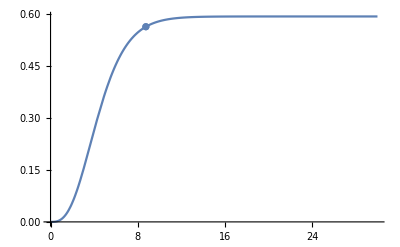

2

0.477482

cumple con ϕ<10^-3

Checking, masa con radio encontrado 9.13209 masa 95, 0.477482 comprobando, True

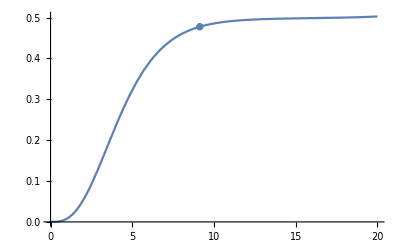

3

0.647296

cumple con ϕ<10^-3

Checking, masa con radio encontrado 8.9595 masa 95, 0.647296 comprobando, True

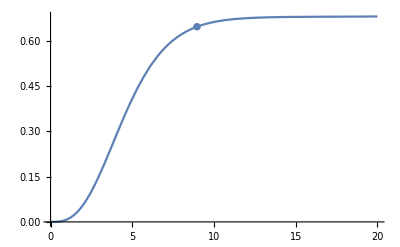

{{8.74764,0.562329},{9.13209,0.477482},{8.9595,0.647296}}

{{0.908925,0.562329},{0.923188,0.477482},{0.896736,0.647296}}

{{0,0.0642835},{0.3,0.0522862},{-0.3,0.0722468}}

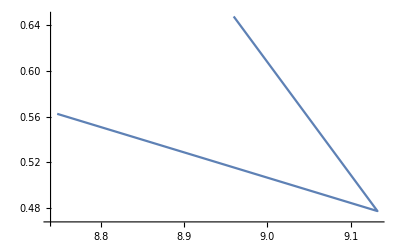

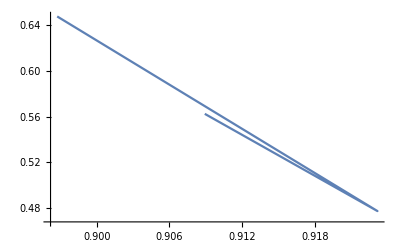

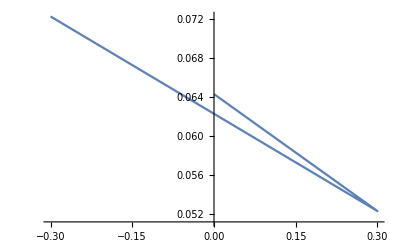

```mathematica
mvsr={};
sphivsswf={};
wfvsm={};
σvsm={};
stop2=0;
α=1;k=1/16/ π;mS=1;L1=1;

For[j=1,j<Length[Bs]+1,j++,
Print[j];
Clear[s,M95, M,rMax,w,η,r0,prec];
r0=1.;
η=prec=Bs[[j,5]];
prec=Bs[[j,4]];
ϕ0=Bs[[j,1]];
w=Bs[[j,2]];
rMax=Bs[[j,3]];
rMin=Bs[[j,6]];

If[stop2≠0,Break[]]; (*Para cuando una frecuencia no es suficientemente pequeña*)

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]; 

M95=0.95M[rMax][[1]]; (* masa física *)
Print[M95];

(* testeando que el valor de phi en el radio encontrado para la masa 95 sea pequeño *)
If[Evaluate[φ[rMax]/.s][[1]]<5*10^-3,Print["cumple con ϕ<10^-3"],Print["No cumple con ϕ<10^-3"]; Print[ϕ0];Break[]];

rad=Last[FindRoot[M[r]==M95,{r,r0,rMax}]];

Print["Checking, masa con radio encontrado ",  rad[[2]],  " masa 95, ", M95, " comprobando, ",  M[rad[[2]]][[1]]- M95<10^-4];

(* Frecuencia física, en este caso es raiz, pq uso N, g *)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];

Print[Show[{Plot[M[r],{r,rMin,rMax},AxesOrigin->{0,0}],ListPlot[{{rad[[2]],M95}}]}]];
(* Guardando datos *)
AppendTo[mvsr,{rad[[2]],M95}];
AppendTo[sphivsswf,{w2, M95}];
AppendTo[wfvsm,{η,M95/rad[[2]]}];
](* FOR *)
(* Resultados *)
mvsr
sphivsswf
wfvsm

(* Plot*)
(*Show[{ListPlot[mvsr],Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},PlotRange->Full]}]*)
Show[{ListPlot[mvsr,PlotRange->Full,Joined->True]}]
Show[{ListPlot[sphivsswf,PlotRange->Full,Joined->True]}]
Show[{ListPlot[wfvsm,PlotRange->Full,Joined->True]}]
```

```mathematica
mvsr={{172.97540831279383,0.04418352091343031},{98.5868990363145,0.07576525972601278},{76.56720554917577,0.09758645020677525},{64.18183400242087,0.11490701650110402},{56.80836603380852,0.13012043009156607},{53.7942492399667,0.13682640605056973},{46.83218916419668,0.1549714748025611},{43.42166700830061,0.16574498784511532}(*,{41.755443310946895,0.17731257107544696}*),{39.320769470728955,0.18661067738127202},{30.91397460060242,0.22988082508630603},{23.52443225239504,0.28681416615919186},{21.31605284471974,0.30900100000710995},{20.474438369055203,0.3192721030978268},{20.14888959035159,0.3231925959035248},(*{20.049257323337866,0.32348451061274763},{20.286497128493274,0.3256203790241492},*){20.03396523211226,0.32486447662035345},(*{20.26247639649418,0.32689348491941794},{20.07738939383414,0.3285760373858866},*)(*{19.869019969144915,0.3300641622830107},{19.43784979245931,0.3327756134203649},{19.243789248054927,0.33687150341062644},*){19.128036011685733,0.3401588817037144},(*{18.679560670625342,0.3434300772608768},*){18.689593772504185,0.3453620777886667},(*{17.78538015406738,0.35642276082886193},{17.47824766805619,0.3587706536386134},{17.488575923933904,0.36316137124976},{17.115388065840964,0.3689584871010285},{16.50160219658021,0.3765463980607622},{16.239521515413056,0.37498694346792616},*){16.29175470266022,0.37955123356006276},(*{15.968575936387632,0.38649113588002504},{15.190696422382194,0.38206664055311496},*){15.713441942197504,0.3898101285538505},{15.288629701789036,0.3948934613273462},{14.999387784561105,0.4007393631383159},{13.466654400496711,0.4247649536441515},{11.918580977049093,0.445563631078994}(*,{11.495689159302637,0.44963344908690345}*),{11.381117800953918,0.45662467418336167},{10.798182734625254,0.46526656703641883},{10.047696596703648,0.4722979556423774},{9.132086151249542,0.4774818642136371},(*{8.568734668289355,0.4710876046489737},*){8.57816228750959,0.475973901983545},{8.265694271856942,0.4716624531318973},{8.161952096675707,0.46998246752499495},{7.933349998726466,0.461918310048060197}};
```

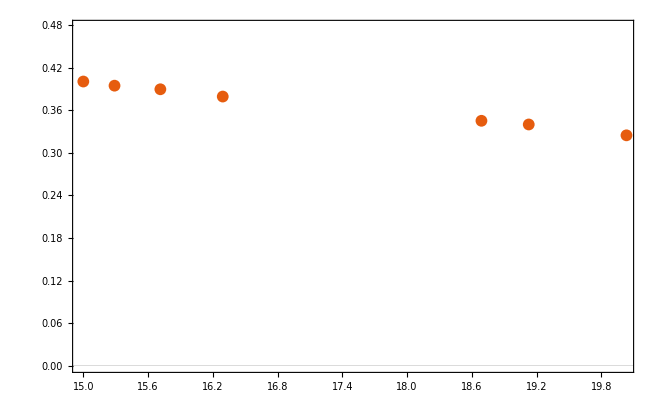

```mathematica
ListPlot[mvsr,PlotTheme->"Scientific",PlotRange->{{15,20},Automatic},Joined->False]
```

```mathematica
A=Interpolation[mvsr,InterpolationOrder->1,Method->"Spline"]
```

InterpolatingFunction[…]

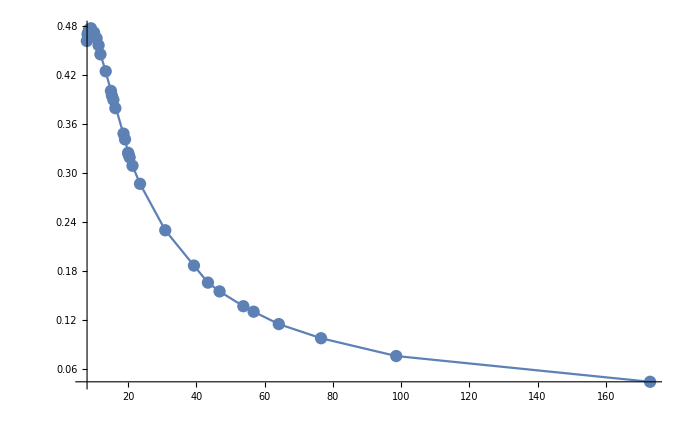

```mathematica
Show[Plot[A[r],{r,8,173}],ListPlot[mvsr]]
```

```mathematica
rvsM95={};
Do[AppendTo[rvsM95,{r,A[r]}],{r,8,173,0.05}]
```

```mathematica
FindMaximum[A[r],{r,8}]
```

{0.477482,{r→9.13209}}

```mathematica
Export["Dat_mvsr_eta03_X.dat",mvsr]
```

Dat_mvsr_eta03_X.dat

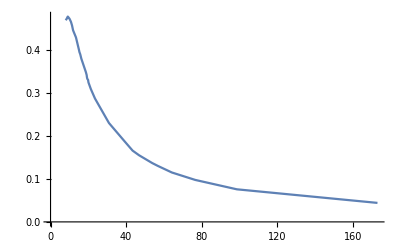

```mathematica
ListPlot[{rvsM95,{{9.132086120780125,0.4776592682348262}}},Joined->True]
```

```mathematica
sphivsswf={{0.999650597878953,0.04418352091343031},{0.9989611610987739,0.07576525972601278},{0.9982720228050431,0.09758645020677525},{0.9975851521551926,0.11490701650110402},{0.9968959559394694,0.13012043009156607},{0.996557549127776,0.13682640605056973},{0.9955405870288865,0.1549714748025611},{0.9948673135463915,0.16574498784511532},{0.9941680319745967,0.17731257107544696},{0.9935004003446191,0.18661067738127202},{0.9898562483530126,0.22988082508630603},{0.9834117328993295,0.28681416615919186},{0.9802814429363752,0.30900100000710995},{0.9787340039200498,0.3192721030978268},{0.9781106532198722,0.3231925959035248},{0.9780283438882791,0.32348451061274763},{0.9778753810641065,0.3256203790241492},{0.9778517623983375,0.32486447662035345},{0.9777062726067904,0.32689348491941794},{0.9774101543989593,0.3285760373858866},{0.9771232199101108,0.3300641622830107},{0.976561754637798,0.3327756134203649},{0.9759276285727589,0.33687150341062644},{0.9752781693147416,0.3412888817037144},{0.9747369096076974,0.3434300772608768},{0.9740621274877799,0.3483620777886667},{0.972345324947336,0.35642276082886193},{0.9717874351363176,0.3587706536386134},{0.9711366553056723,0.36316137124976},{0.9699688403280565,0.3689584871010285},{0.9682614483960723,0.3765463980607622},{0.9682903234306762,0.37498694346792616},{0.9675963524458785,0.37955123356006276},{0.966124327696694,0.38649113588002504},{0.9660634477426367,0.38206664055311496},{0.9652942917515553,0.3898101285538505},{0.9639366298659492,0.3948934613273462},{0.9625252832682885,0.4007393631383159},{0.9545180438944669,0.4287649536441515},{0.9471962050370388,0.445563631078994},{0.9449369557642832,0.44963344908690345},{0.9424849441639812,0.45662467418336167},{0.9378328875509738,0.46526656703641883},{0.9318514911805578,0.4722979556423774},{0.923187893570742,0.4774818642136371},(*{0.9222795035315907,0.4710876046489737},*){0.9207592525443229,0.475973901983545},{0.9194833803161468,0.4716624531318973},{0.9181345535633455,0.46998246752499495},{0.9168582713380685,0.461918310048060197}};
```

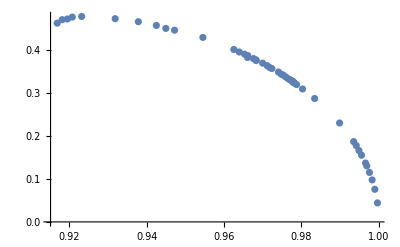

```mathematica
ListPlot[sphivsswf]
```

```mathematica
Xeta03wvsM=Interpolation[sphivsswf,InterpolationOrder->1,Method->"Spline"];
```

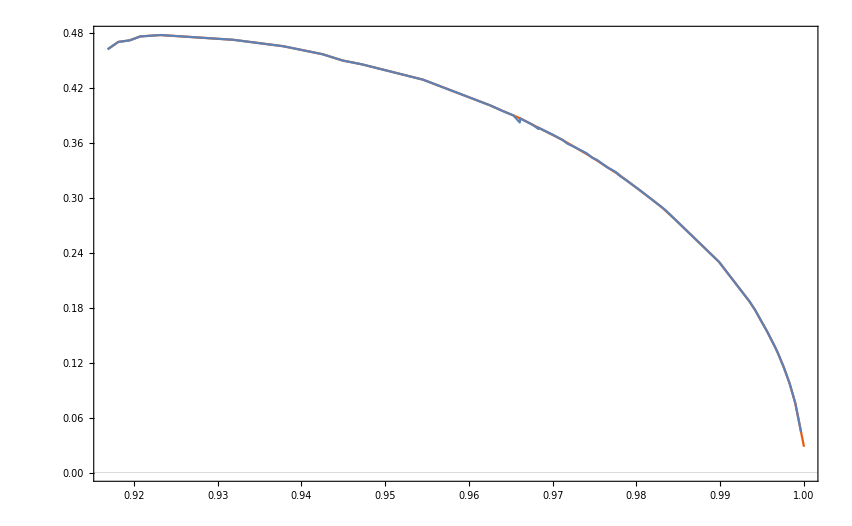

```mathematica
Show[Plot[Xeta03wvsM[w],{w,0.9168582713380685,1},PlotTheme->"Scientific"],ListPlot[sphivsswf,Joined->True]]
```

```mathematica
wvsM95={};
Do[AppendTo[wvsM95,{w,Xeta03wvsM[w]}],{w,0.9168582713380685,1,0.0005}]
```

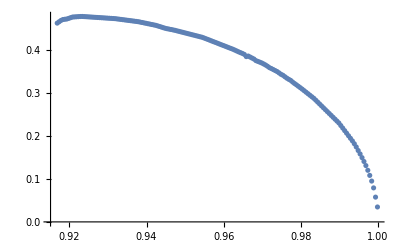

```mathematica
ListPlot[wvsM95,PlotRange->All]
```

```mathematica
Export["Dat_wvsM95_eta03_X.dat",wvsM95]
```

Dat_wvsM95_eta03_X.dat

```mathematica
mvsr={};
Do[AppendTo[mvsr,{R,XXeta03mvsr[R]}],{R,4.8,55,0.1}]
```

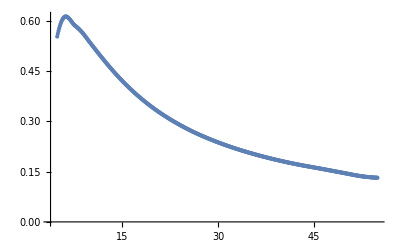

```mathematica
ListPlot[mvsr,PlotRange->All]
```

```mathematica
Export["Dat_mvsr_etam03.dat",mvsr]
```

Dat_mvsr_etam03.dat

```mathematica
wvsM95=Import["Dat_wvsM95_etam03.dat"]
```

{{0.835,0.697643},{0.837,0.652791},{0.839,0.617002},{0.841,0.590276},{0.843,0.572613},{0.845,0.563568},{0.847,0.55864},{0.849,0.55666},{0.851,0.557629},{0.853,0.561546},{0.855,0.568411},{0.857,0.576169},{0.859,0.582877},{0.861,0.588536},{0.863,0.593146},{0.865,0.596706},{0.867,0.599217},{0.869,0.600753},{0.871,0.60145},{0.873,0.60131},{0.875,0.600333},{0.877,0.598519},{0.879,0.596072},{0.881,0.593715},{0.883,0.591514},{0.885,0.589469},{0.887,0.587579},{0.889,0.585845},{0.891,0.584221},{0.893,0.582476},{0.895,0.58058},{0.897,0.578533},{0.899,0.576335},{0.901,0.573985},{0.903,0.571483},{0.905,0.568831},{0.907,0.566027},{0.909,0.563071},{0.911,0.559965},{0.913,0.556707},{0.915,0.553295},{0.917,0.549724},{0.919,0.545993},{0.921,0.542103},{0.923,0.538054},{0.925,0.533846},{0.927,0.529478},{0.929,0.524951},{0.931,0.520265},{0.933,0.515416},{0.935,0.510371},{0.937,0.505142},{0.939,0.499683},{0.941,0.493962},{0.943,0.488135},{0.945,0.481968},{0.947,0.475544},{0.949,0.468919},{0.951,0.462014},{0.953,0.454815},{0.955,0.447306},{0.957,0.439483},{0.959,0.431332},{0.961,0.422803},{0.963,0.413892},{0.965,0.404597},{0.967,0.394841},{0.969,0.384576},{0.971,0.373818},{0.973,0.362495},{0.975,0.350554},{0.977,0.337865},{0.979,0.324424},{0.981,0.310173},{0.983,0.294775},{0.985,0.278176},{0.987,0.260361},{0.989,0.24064},{0.991,0.218638},{0.993,0.193744},{0.995,0.165662},{0.997,0.132652},{0.999,0.0951655}}

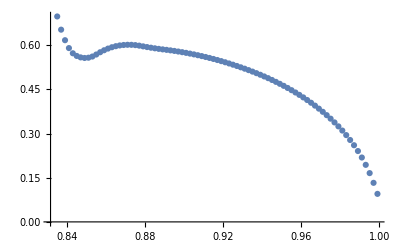

```mathematica
ListPlot[wvsM95]
```

## Test

```mathematica
A[r_,η_,w_]=1/(1+120π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2)/(gg[r]^2 NN[r]^2));
```

```mathematica
Clear[η,w]
```

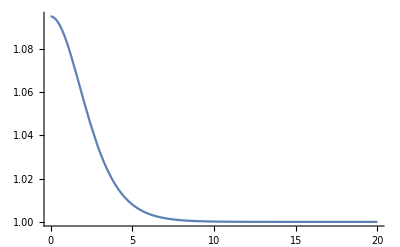

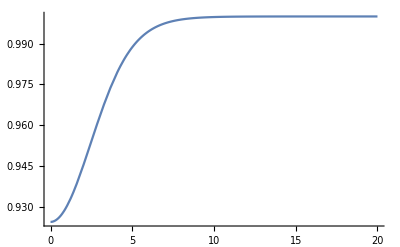

```mathematica
a=Plot[Evaluate[A[r,0.3,0.923187893570742]/.sP],{r,rMin,20},PlotRange->All]
b=Plot[Evaluate[A[r,-0.3,0.8967355292683497]/.sN],{r,rMin,rMax},PlotRange->All]
```

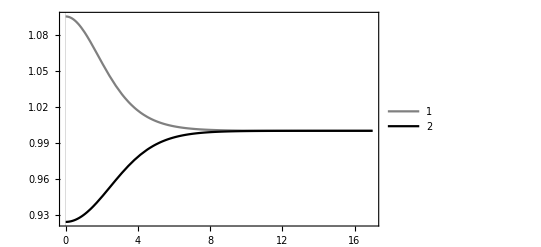

```mathematica
Plot[{Evaluate[A[r,0.3,0.923187893570742]/.sP],Evaluate[A[r,-0.3,0.8967355292683497]/.sN]},{r,rMin,17},PlotRange->All,PlotStyle->{Gray,Black},PlotTheme->"Scientific",PlotLegends->Automatic]
```

```mathematica
Bs={0.03,1.121058474193216440,20,30,-0.3,10^-8};
```

```mathematica
Bs={0.03,1.10939,20,30,0.3,10^-8};
```

```mathematica
Bs={0.03,1.116036581602133000,30,30,0,10^-8};
```

```mathematica
Bs={0.015,1.054140552042320860,28,30,-0.3,10^-8};
```

0.948119

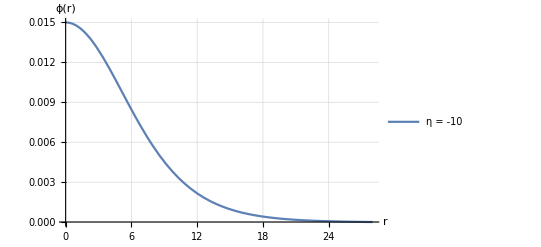

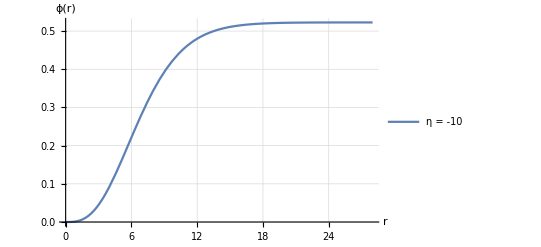

```mathematica
(*α=1;k=1/16/ π;mS=1;L1=1;
η=0.3;
prec=30;
ϕ0=0.03;
w=1.127645644578;
rMax=7.4;
rMin=10^-6;*)

α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=Bs[[1]];
w=Bs[[2]];
rMax=Bs[[3]];
rMin=Bs[[6]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}, MaxSteps->10^6];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];

Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)/.s]; 

M95=0.95M[rMax][[1]]; (* masa física *)
rad=Last[FindRoot[M[r]==M95,{r,rMin+0.5,rMax}]];
Print[rad, M95];
```

r→13.1810.496469

```mathematica
(* sin la corrección *)
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

```mathematica
Masa=Evaluate[M[rMax]/.s][[1]]
```

0.591925

```mathematica
0.95*%
```

0.562329

```mathematica
w2
```

0.923188

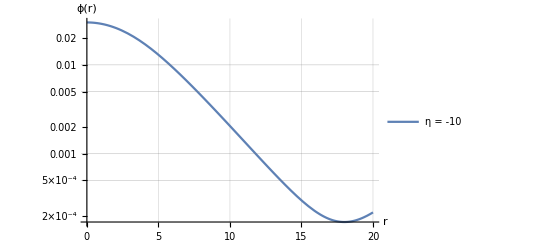

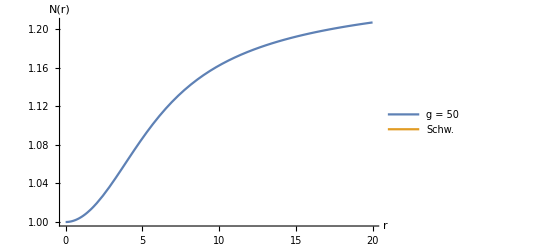

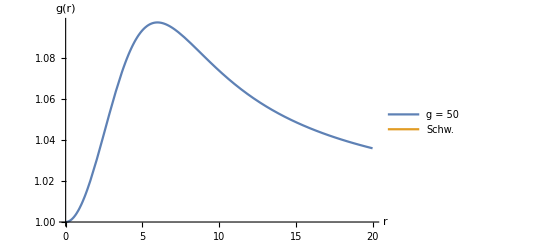

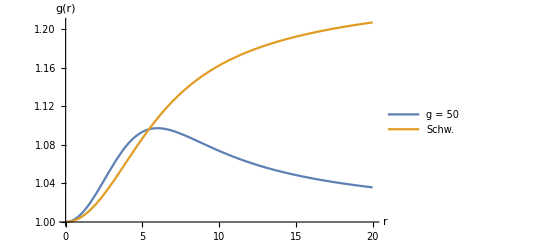

```mathematica
LogPlot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->All,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]

Plot[{Evaluate[gg[r]/.s],Evaluate[NN[r]/.s]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,Evaluate[gg[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncN={};
Do[AppendTo[FuncN,{r,Evaluate[NN[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Funcsigma={};
Do[AppendTo[Funcsigma,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncM={};
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

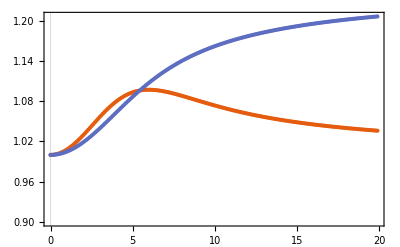

```mathematica
ListPlot[{Funcg,FuncN},PlotTheme->"Scientific",AxesOrigin->{0,0.9}, PlotRange->Automatic]
```

```mathematica
Export["Funcg.dat",Funcg]
Export["FuncN.dat",FuncN]
Export["FuncM.dat",FuncM]
Export["FuncsigmaM.dat",Funcsigma]
```

Funcg.dat

FuncN.dat

FuncM.dat

FuncsigmaM.dat

```mathematica
w2
```

0.896736

```mathematica
Clear[rMin,rTest,α,w,ϕ0,mS,k,η]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==1*B[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];

(*AppendTo[SeidelBCList,{NN[rMin]==(1+(rMin^2 (-2 k (mS^2-2 w^2 α+6 w^4 η) ϕ0^2+w^2 η (2 mS^2-w^2 α+6 w^4 η) ϕ0^4))/(6 (-2 k+w^2 η ϕ0^2)^2))*B[[1,1,1,2]],gg[rMin]==1+(rMin^2 (mS^2+w^2 α) ϕ0^2)/(2 (6 k-3 w^2 η ϕ0^2)),φ[rMin]==ϕ0-1/2 rMin^2 w^2 ϕ0,NN'[rMin]==((rMin (-2 k (mS^2-2 w^2 α+6 w^4 η) ϕ0^2+w^2 η (2 mS^2-w^2 α+6 w^4 η) ϕ0^4))/(3 (-2 k+w^2 η ϕ0^2)^2))*B[[1,1,1,2]],gg'[rMin]==(rMin (mS^2+w^2 α) ϕ0^2)/(6 k-3 w^2 η ϕ0^2),φ'[rMin]==-rMin w^2 ϕ0}];*)
```

```mathematica
(*
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=0.89676(*w2*);
rMax=SetPrecision[Bs[[3]],prec];
rMin=10^(-6)(*SetPrecision[Bs[[6]],prec]*);
*)
```

```mathematica
w2
```

0.948119

```mathematica
8.9595
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

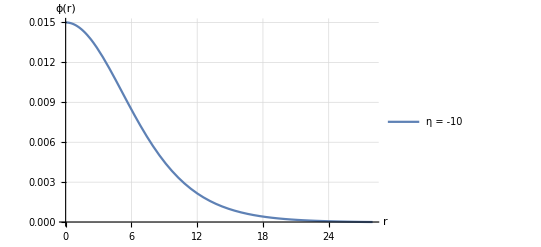

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w= w2(*w2*);(*0.8967355292683497*)
rMax=28(*SetPrecision[Bs[[3]],prec]*)(*28*);
rMin=10^-6(*SetPrecision[Bs[[6]],prec]*);

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
{Evaluate[gg[rMin]/.s],Evaluate[NN[rMin]/.s]}
{Evaluate[gg[rMax]/.s],Evaluate[NN[rMax]/.s]}
```

{{1.},{0.899424}}

{{1.0192},{0.981158}}

```mathematica
Masa=Evaluate[M[rMax]/.s][[1]]
```

0.522596

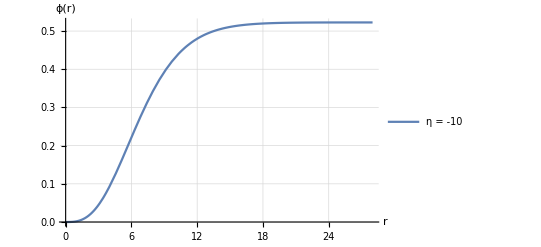

```mathematica
Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

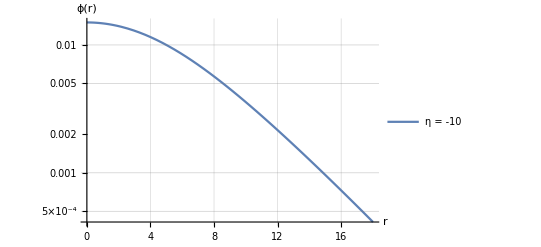

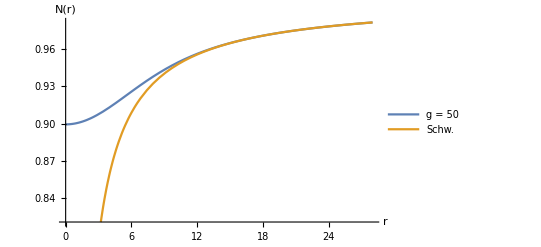

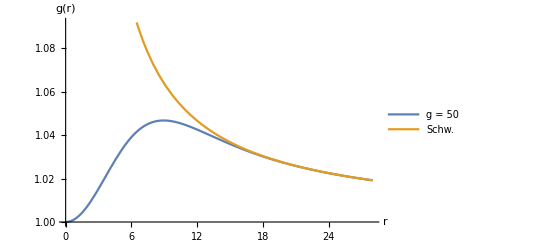

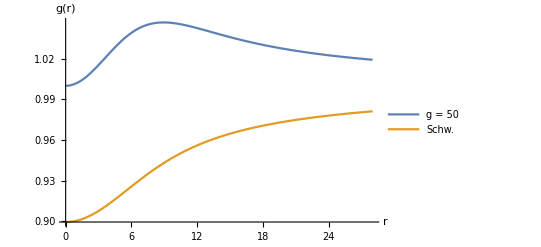

```mathematica
LogPlot[{Evaluate[φ[r]/.s]},{r,rMin,18},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

(* Ploteando la función lapso *)
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->Automatic,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]

Plot[{Evaluate[gg[r]/.s],Evaluate[NN[r]/.s]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

Saved data

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,Evaluate[gg[r]/.s][[1]]}],{r,rMin,rMax,0.1}]

FuncN={};
Do[AppendTo[FuncN,{r,Evaluate[NN[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
FuncM={};
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

```mathematica
Export["FuncgM.dat",Funcg]
Export["FuncNM.dat",FuncN]
```

FuncgM.dat

FuncNM.dat

```mathematica
Export["FuncM.dat",FuncM]
```

FuncM.dat

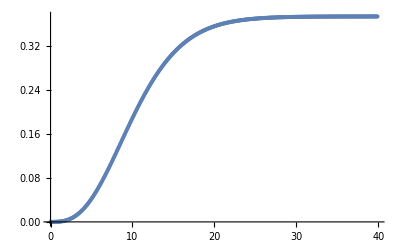

```mathematica
ListPlot[FuncM]
```

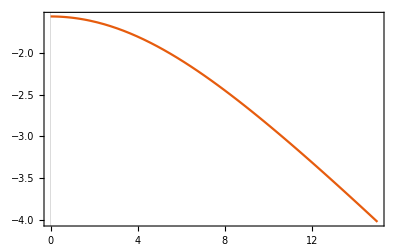

```mathematica
Van[r_]:=Abs[(gg[r]^2 NN[r]^2)/(gg[r]^2 NN[r]^2+120π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2))-1];(*Subscript[G, N]/G*)

Plot[Evaluate[Log10@Van[r]/.s],{r,rMin,15}, PlotRange->All,AxesOrigin->{0,0},PlotTheme->"Scientific"]
```

```mathematica
Evaluate[Van[r]/.s]/.r->13.181038383474181
```

{0.000256172}

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,(Evaluate[Van[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,15,0.1}]
```

```mathematica
Export["VanisX_1.dat",Funcg]
```

VanisX_1.dat

```mathematica
a=Interpolation[Funcg]
```

InterpolatingFunction[…]

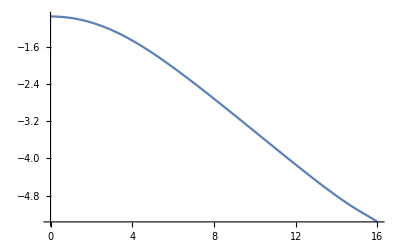

```mathematica
Plot[Log10[a[r]],{r,rMin,16}]
```

```mathematica
Funcg={};
Do[AppendTo[Funcg,{r,a[r]}],{r,rMin,16,0.1}]
```

InterpolatingFunction::dmval: Input value {15.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["VanisX_1.dat",Funcg]
```

VanisX_1.dat

```mathematica
Van2[r_]:=(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2);
```

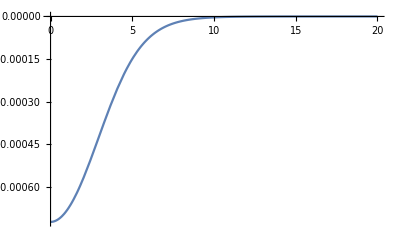

```mathematica
Plot[Evaluate[Van2[r]/.s],{r,rMin,rMax}, PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
FindRoot[Evaluate[Log10@Van[r]/.s][[1]]==-4.327902142064283,{r,10}]
```

{r→16.2188}

```mathematica
Log10[4.7*10^-5]
```

-4.3279

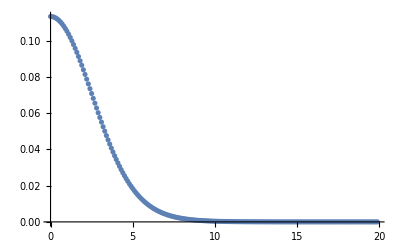

```mathematica
ListPlot[Funcg]
```

## Generando datos

```mathematica
{0.03,1.116036581602133000,30,50,0,10^-3}
{0.03,1.121058474193216440,20,30,-0.3,10^-6}
{0.03,1.1277988,7.4,30,0.3,10^-6}
```

```mathematica
Bs={0.03,1.1277988,7.4,20,0.3,10^-5};(*{0.0154000000000000022287727219350017549004405736923217773438`30.,1.0546788959098194764548370427290855606400515072482073491988`30.,60.061,30,-0.3,10^-3}*)(*Datm03[[-10]]*);
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

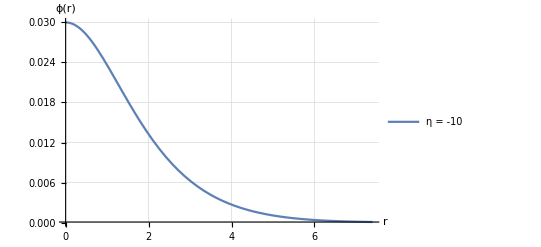

```mathematica
(*α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w=SetPrecision[Bs[[2]],prec];
rMax=SetPrecision[Bs[[3]],prec];
rMin=SetPrecision[Bs[[6]],prec];
*)
 α=1;k=1/16/ π;mS=1;L1=1;
prec=30;
η=0.3;
rMin=10^-6;
ϕ0=0.03;
 w=1.1277988; 
rMax=7.4; 

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];
```

```mathematica
Funcphi={};
FuncM={};
Do[AppendTo[Funcphi,{r,Evaluate[φ[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
Do[AppendTo[FuncM,{r,Evaluate[M[r]/.s][[1]]}],{r,rMin,rMax,0.1}]
```

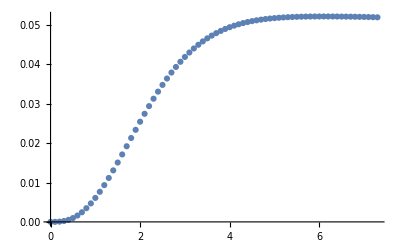

```mathematica
ListPlot[FuncM]
```

```mathematica
Export["FuncsigmaBHX_P.dat",Funcphi]
Export["M_BHX_P.dat",FuncM]
```

FuncsigmaBHX_P.dat

M_BHX_P.dat

```mathematica
w2
```

1.08395

```mathematica
Evaluate[M[rMax]/.s][[1]]
```

0.0519358

```mathematica
0.95*%
```

0.049339

```mathematica
{0.9089245208822979,0.562397120568672},{0.8967355379880991,0.6472954746573958}
```

0.579585

0.562397

```mathematica
Export["FuncsigmaKG.dat",Funcphi]
Export["M_KG.dat",FuncM]
```

XX_2_sigma_Profile_Pos.dat

XX_2_masa_Profile_Pos.dat

## Analysis

{{φ'[0]→0},{φ'[0]→0},{φ'[0]→-(w φ[0])/NN[0]},{φ'[0]→(w φ[0])/NN[0]},{φ'[0]→-(√3 √(w^4 φ[0]^3+w^2 NN[0]^2 φ[0]^2 φ''[0]))/(√(5 w^2 NN[0]^2 φ[0]+NN[0]^4 φ''[0]))},{φ'[0]→(√3 √(w^4 φ[0]^3+w^2 NN[0]^2 φ[0]^2 φ''[0]))/(√(5 w^2 NN[0]^2 φ[0]+NN[0]^4 φ''[0]))}}

```mathematica
Evaluate[φ'[rMin]/.s][[1]]
```

-8.54876×10^-8

```mathematica
φ'[0]->-(w ϕ0)/1
```

φ'[0]→-0.0077357187988281249024994777364

```mathematica
-8.548763619220407*^-8-(-0.0077357187988281249024994777363809938003528029289281311808`29.69897000433602)
```

0.00773563

```mathematica
φ'[0]->-(√3 √(w^4 ϕ0^3))/(√(5 w^2 ϕ0))
```

φ'[0]→-0.0059920620157609941523327938175

```mathematica
a={};
Do[AppendTo[a,{r,Abs@Evaluate[φ'[r]/.s][[1]]}],{r,rMin,6,0.001}]

b={};
Do[AppendTo[b,{r,Abs@Evaluate[φ'[r]/.s1][[1]]}],{r,rMin,6,0.001}]
```

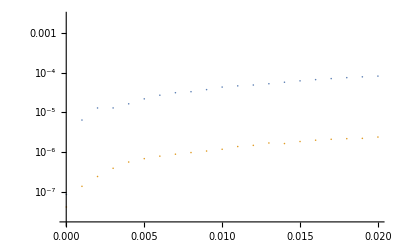

```mathematica
ListLogPlot[{a,b},PlotRange->{{0,0.02},Automatic}]
```

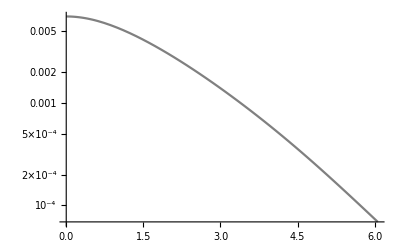

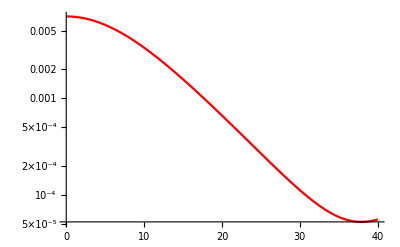

```mathematica
A=LogPlot[{Abs@Evaluate[φ[r]/.s]},{r,rMin,rMax},PlotStyle->Gray]
B=LogPlot[{Abs@Evaluate[φ[r]/.s1]},{r,rMin,40},PlotStyle->Red]
```

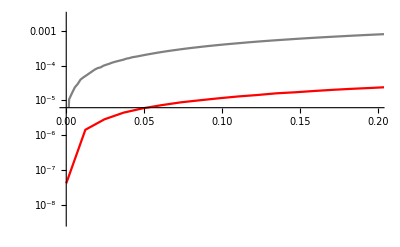

```mathematica
Show[{A,B},PlotRange->{{0,0.2},Automatic}]
```

## Test

```mathematica
Bs={0.03,1.121058474193216440,20,30,-0.3,10^-8};
```

```mathematica
Bs={0.03,1.10939,20,30,0.3,10^-8};
```

0.896736

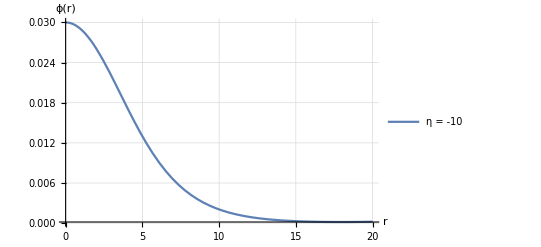

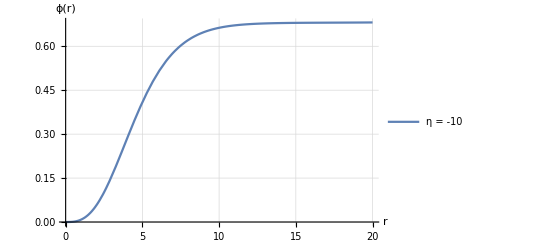

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=Bs[[1]];
w=Bs[[2]];
rMax=Bs[[3]];
rMin=Bs[[6]];

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}, MaxSteps->10^6];

B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
w2=w*B[[1,1,1,2]]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]

M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];

Plot[{Evaluate[M[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
Clear[rMin,rTest,α,w,ϕ0,mS,k,η]
```

```mathematica
SeidelEqsList={};
SeidelBCList={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{DDPhi,DNN,Dgg}];
AppendTo[SeidelCoefFunctionsList,{NN,gg,φ}];

AppendTo[SeidelBCList,{NN[rMin]==1*B[[1,1,1,2]],gg[rMin]==1.,φ[rMin]==ϕ0, φ'[rMin] == 0 ,NN'[rMin] == 0}];
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

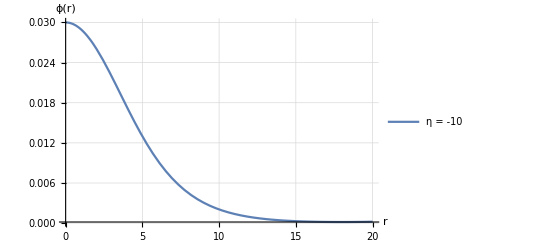

```mathematica
α=1;k=1/16/ π;mS=1;L1=1;
η=Bs[[5]];
prec=Bs[[4]];
ϕ0=SetPrecision[Bs[[1]],prec];
w= 0.8967355292683497(*w2*);(*0.8967355292683497*)
rMax=SetPrecision[Bs[[3]],prec](*28*);
rMin=10^-6(*SetPrecision[Bs[[6]],prec]*);

s=NDSolve[{SetPrecision[SeidelEqsList[[1]],prec],SetPrecision[SeidelBCList[[1]],prec]},SetPrecision[SeidelCoefFunctionsList[[1]],prec],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -10" (*, "η = 0.01","η = 0.1"*), "η = 0.5","η = 0.95"(*, "η = -0.01","η = -0.1"*), "η = -0.5","η = -0.95"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

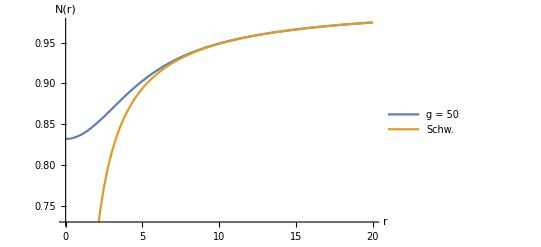

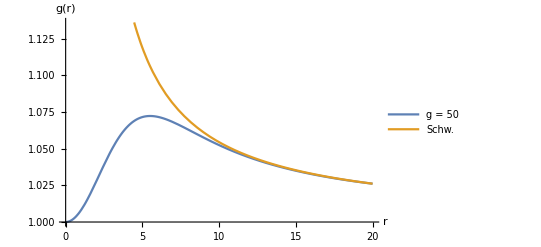

```mathematica
(* Ploteando la función lapso *)
Masa=Evaluate[M[rMax]/.s];
Plot[{Evaluate[NN[r]/.s],Sqrt[(1-(2Masa)/r)]},
{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.56}],
PlotRange->Automatic,AxesLabel->{"r","N(r)"}]

(* Ploteando la función g *)
Plot[{Evaluate[gg[r]/.s],Sqrt[(1-(2Masa)/r)^-1]},
{r,rMin,rMax},Background->White,PlotLegends->Placed[{"g = 50","Schw."},{0.85,0.7}],PlotRange->Automatic,
AxesLabel->{"r","g(r)"}]
```

```mathematica
den[r_]:=gg[r]^2 NN[r]^2+120π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2);
```

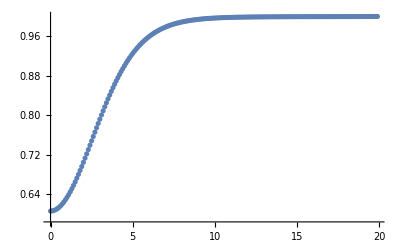

```mathematica
FuncD={};
Do[AppendTo[FuncD,{r, (Evaluate[den[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,rMax,0.1}]
ListPlot[FuncD]
```

```mathematica
η
```

0.3

```mathematica
Export["EtaP.dat",FuncD]
```

EtaP.dat

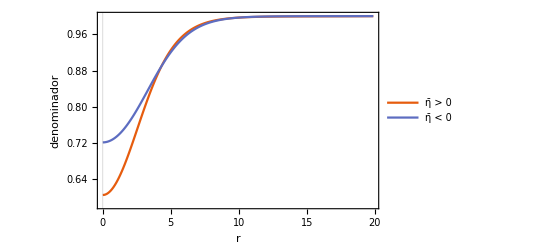

```mathematica
Pos=Import["EtaP.dat"];
Neg=Import["EtaN.dat"];

ListPlot[{Pos,Neg},PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameLabel->{"r"," denominador"},PlotLegends->Placed[{"η̄ > 0", "η̄ < 0"},{0.75,0.45}]]
```

```mathematica
Van[r_]:=(gg[r]^2 NN[r]^2)/(gg[r]^2 NN[r]^2+120π η(D[φ[r],r]^2 NN[r]^2-gg[r]^2 φ[r]^2 w^2))
```

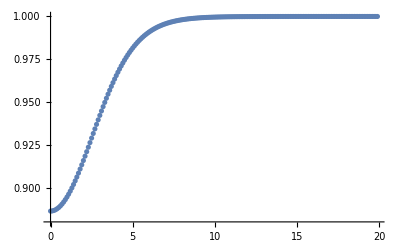

```mathematica
FuncD2={};
Do[AppendTo[FuncD2,{r, (Evaluate[Van[rB]/.s]/.rB-> r)[[1]]}],{r,rMin,rMax,0.1}]
ListPlot[FuncD2]
```

```mathematica
Export["TestEtaN.dat",FuncD2]
```

TestEtaN.dat

```mathematica
(*estan al reves *)
TPos=Import["TestEtaP.dat"];
TNeg=Import["TestEtaN.dat"];
```

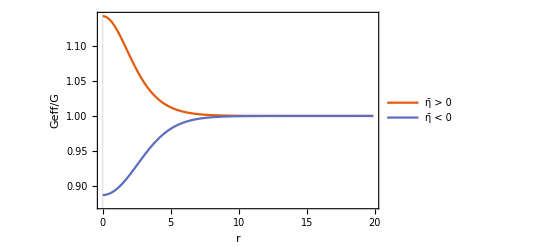

```mathematica
ListPlot[{TPos,TNeg},PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameLabel->{"r"," Geff/G"},PlotLegends->Placed[{"η̄ > 0", "η̄ < 0"},{0.75,0.75}]]
```